```mathematica
(* notebook to solve for tidal deformability of NS with axions *)
```

```mathematica
Quit[]
```

## Dependencies and Globals

```mathematica
(* LOAD PACKAGES *)
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,xcolor}"}];

$PrePrint=TraditionalForm;

(* PRECISION AND ACCURACY *)
NPRECISON = 11;

(* GLOBALS *)
Msun=1.989*10^30;(* kg *)
GN = 6.67*10^-11; (* SI *)
G=(*6.70883*10^(-57)*)1; (* eV^-2 *)
clight = 2.99792458*10^8; (* m/s *)
eV2joules=1.60218*10^(-19);
GeV2joules=1.60218*10^(-10);
mN = 0.939563; (* GeV *)
hbarGeV=6.582119569*10^(-25); (* GeV S *)
hbarJ = 1.05457*10^(-34); (* J s *)
hbarGeo = hbarJ * (GN / clight^4) * clight; (* m^2 *)
(*GNeV = 6.70883*10^(-39);*)
σN = 0.059;(* GeV *)(* eV*s *)
rkm=10^3 / (hbarGeV*clight);
rm=1/(hbarGeV*clight);
mpi = 0.134977;
fpi = 0.130;
mu = 0.0017;
md = 0.0041;
me = 0.000511;
RSTART=10^-8;
RHOFRAC=10^-10;
m2Msun = (clight^2 / GN) / Msun;

MeVperfm3 2 Jperm3=(10^-3*GeV2joules) * (10^(-15))^(-3);
Jperm3 2 m2 = GN / clight^4;
GeV2m = GeV2joules*GN/clight^4;

RescaleMRPair km Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]]/10^3, ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRPair km Msun from file[MRPair_]:={(MRPair[[1]]), ((MRPair[[2]])*clight^2/GN)/Msun}
RescaleMRΛTriplet km Msun dim0[MRΛTriplet_,scales_]:={(MRΛTriplet[[1]])*scales[[1]]/10^3, ((MRΛTriplet[[2]])*scales[[3]]*clight^2/GN)/Msun,MRΛTriplet[[3]]}
RescaleMRPair m Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRPair m kg[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]]*clight^2/GN)*scales[[1]]^3 * scales[[2]])}
RescaleM kg[mass_,scales_]:=((mass*clight^2/GN)*scales[[1]]^3 * scales[[2]])
RescaleR m[radius_,scales_]:=(radius)*scales[[1]]

TOV replacements={λ'[r]->D[Log[1/(1 - 2*M[r]/r)],r],λ''[r]->D[-Exp[λ[r]]*(2*M[r]/r^2 - 8*Pi*r*ρ[r]),r],
Exp[λ[r]]->1/(1 - 2*M[r]/r),
Exp[-λ[r]]->(1 - 2*M[r]/r),
λ[r]->Log[1/(1 - 2*M[r]/r)],Derivative[1][p][r]->-(((M[r]+4*Pi*r^3*p[r])*(p[r]+ρ[r]))/(r*(r-2*M[r]))),
Derivative[2][p][r]->Simplify[D[-(((M[r]+4*Pi*r^3*p[r])*(p[r]+ρ[r]))/(r*(r-2*M[r]))),r]],
Derivative[1][ν][r]->-2*(Derivative[1][p][r])/(p[r]+ρ[r]),
M'[r]->4*Pi*r^2*ρ[r]};

c1=RGBColor[101/255,144/255,255/255];
c2=RGBColor[121/255,94/255,240/255];
c3=RGBColor[221/255,38/255,129/255];
c4=RGBColor[255/255,97/255,2/255];
c5=RGBColor[254/255,176/255,1/255];
c6=RGBColor[200/255,200/255,200/255];
c7=RGBColor[13/255,35/255,65/255];
c8=RGBColor[0/255,130/255,61/255];
```

```mathematica
c6
```

RGBColor[Rational[40, 51], Rational[40, 51], Rational[40, 51]]

```mathematica
(* color map *)
p1 = {101/255,144/255,255/255};
p2={121/255,94/255,240/255};
p3 = {221/255,38/255,129/255};
p4={255/255,97/255,2/255};
p5 = {254/255,176/255,1/255};
line12[t_]:= {p1[[1]] + t*(p2[[1]] - p1[[1]]),p1[[2]] + t*(p2[[2]] - p1[[2]]),p1[[3]] + t*(p2[[3]] - p1[[3]])};
line23[t_]:= {p2[[1]] + t*(p3[[1]] - p2[[1]]),p2[[2]] + t*(p3[[2]] - p2[[2]]),p2[[3]] + t*(p3[[3]] - p2[[3]])};
line34[t_]:= {p3[[1]] + t*(p4[[1]] - p3[[1]]),p3[[2]] + t*(p4[[2]] - p3[[2]]),p3[[3]] + t*(p4[[3]] - p3[[3]])};
line45[t_]:= {p4[[1]] + t*(p5[[1]] - p4[[1]]),p4[[2]] + t*(p5[[2]] - p4[[2]]),p4[[3]] + t*(p5[[3]] - p4[[3]])};

line12[t_]:= {p1[[1]] + t*(p2[[1]] - p1[[1]]),p1[[2]] + t*(p2[[2]] - p1[[2]]),p1[[3]] + t*(p2[[3]] - p1[[3]])};
line23[t_]:= {p2[[1]] + (t-1)*(p3[[1]] - p2[[1]]),p2[[2]] + (t-1)*(p3[[2]] - p2[[2]]),p2[[3]] + (t-1)*(p3[[3]] - p2[[3]])};
line34[t_]:= {p3[[1]] + (t-2)*(p4[[1]] - p3[[1]]),p3[[2]] + (t-2)*(p4[[2]] - p3[[2]]),p3[[3]] + (t-2)*(p4[[3]] - p3[[3]])};
line45[t_]:= {p4[[1]] + (t-3)*(p5[[1]] - p4[[1]]),p4[[2]] + (t-3)*(p5[[2]] - p4[[2]]),p4[[3]] + (t-3)*(p5[[3]] - p4[[3]])};

linetocolortotal[t_]:=If[4*t<=1,line12[4*t],If[4*t<=2,line23[4*t],If[4*t<=3,line34[4*t],line45[4*t]]]]
```

```mathematica
(* make color map *)
IBMcolors[Npoints_]:= Join[Table[RGBColor[line12[t][[1]],line12[t][[2]],line12[t][[3]]],{t,0,1,4/(Npoints-1)}],Table[RGBColor[line23[t][[1]],line23[t][[2]],line23[t][[3]]],{t,0,1,4/(Npoints-1)}],Table[RGBColor[line34[t][[1]],line34[t][[2]],line34[t][[3]]],{t,0,1,4/(Npoints-1)}],Table[RGBColor[line45[t][[1]],line45[t][[2]],line45[t][[3]]],{t,0,1,4/(Npoints-1)}]]

IBMcolorsNew[Npoints_]:= Table[RGBColor[linetocolortotal[t][[1]],linetocolortotal[t][[2]],linetocolortotal[t][[3]]],{t,0,1-1/(Npoints),1/(Npoints)}]
```

```mathematica
IBMcolorsNew[100]
```

{RGBColor[Rational[101, 255], Rational[48, 85], 1],RGBColor[Rational[509, 1275], Rational[142, 255], Rational[424, 425]],RGBColor[Rational[171, 425], Rational[28, 51], Rational[423, 425]],RGBColor[Rational[517, 1275], Rational[46, 85], Rational[422, 425]],RGBColor[Rational[521, 1275], Rational[8, 15], Rational[421, 425]],RGBColor[Rational[7, 17], Rational[134, 255], Rational[84, 85]],RGBColor[Rational[529, 1275], Rational[44, 85], Rational[419, 425]],RGBColor[Rational[533, 1275], Rational[26, 51], Rational[418, 425]],RGBColor[Rational[179, 425], Rational[128, 255], Rational[417, 425]],RGBColor[Rational[541, 1275], Rational[42, 85], Rational[416, 425]],RGBColor[Rational[109, 255], Rational[124, 255], Rational[83, 85]],RGBColor[Rational[183, 425], Rational[122, 255], Rational[414, 425]],RGBColor[Rational[553, 1275], Rational[8, 17], Rational[413, 425]],RGBColor[Rational[557, 1275], Rational[118, 255], Rational[412, 425]],RGBColor[Rational[11, 25], Rational[116, 255], Rational[411, 425]],RGBColor[Rational[113, 255], Rational[38, 85], Rational[82, 85]],RGBColor[Rational[569, 1275], Rational[112, 255], Rational[409, 425]],RGBColor[Rational[191, 425], Rational[22, 51], Rational[24, 25]],RGBColor[Rational[577, 1275], Rational[36, 85], Rational[407, 425]],RGBColor[Rational[581, 1275], Rational[106, 255], Rational[406, 425]],RGBColor[Rational[39, 85], Rational[104, 255], Rational[81, 85]],RGBColor[Rational[589, 1275], Rational[2, 5], Rational[404, 425]],RGBColor[Rational[593, 1275], Rational[20, 51], Rational[403, 425]],RGBColor[Rational[199, 425], Rational[98, 255], Rational[402, 425]],RGBColor[Rational[601, 1275], Rational[32, 85], Rational[401, 425]],RGBColor[Rational[121, 255], Rational[94, 255], Rational[16, 17]],RGBColor[Rational[25, 51], Rational[2294, 6375], Rational[1963, 2125]],RGBColor[Rational[43, 85], Rational[746, 2125], Rational[1926, 2125]],RGBColor[Rational[133, 255], Rational[2182, 6375], Rational[1889, 2125]],RGBColor[Rational[137, 255], Rational[2126, 6375], Rational[1852, 2125]],RGBColor[Rational[47, 85], Rational[138, 425], Rational[363, 425]],RGBColor[Rational[29, 51], Rational[2014, 6375], Rational[1778, 2125]],RGBColor[Rational[149, 255], Rational[1958, 6375], Rational[1741, 2125]],RGBColor[Rational[3, 5], Rational[634, 2125], Rational[1704, 2125]],RGBColor[Rational[157, 255], Rational[1846, 6375], Rational[1667, 2125]],RGBColor[Rational[161, 255], Rational[358, 1275], Rational[326, 425]],RGBColor[Rational[11, 17], Rational[34, 125], Rational[1593, 2125]],RGBColor[Rational[169, 255], Rational[1678, 6375], Rational[1556, 2125]],RGBColor[Rational[173, 255], Rational[1622, 6375], Rational[1519, 2125]],RGBColor[Rational[59, 85], Rational[522, 2125], Rational[1482, 2125]],RGBColor[Rational[181, 255], Rational[302, 1275], Rational[17, 25]],RGBColor[Rational[37, 51], Rational[1454, 6375], Rational[1408, 2125]],RGBColor[Rational[63, 85], Rational[466, 2125], Rational[1371, 2125]],RGBColor[Rational[193, 255], Rational[1342, 6375], Rational[1334, 2125]],RGBColor[Rational[197, 255], Rational[1286, 6375], Rational[1297, 2125]],RGBColor[Rational[67, 85], Rational[82, 425], Rational[252, 425]],RGBColor[Rational[41, 51], Rational[1174, 6375], Rational[1223, 2125]],RGBColor[Rational[209, 255], Rational[1118, 6375], Rational[1186, 2125]],RGBColor[Rational[71, 85], Rational[354, 2125], Rational[1149, 2125]],RGBColor[Rational[217, 255], Rational[1006, 6375], Rational[1112, 2125]],RGBColor[Rational[13, 15], Rational[38, 255], Rational[43, 85]],RGBColor[Rational[109, 125], Rational[1009, 6375], Rational[3098, 6375]],RGBColor[Rational[329, 375], Rational[356, 2125], Rational[2971, 6375]],RGBColor[Rational[331, 375], Rational[1127, 6375], Rational[948, 2125]],RGBColor[Rational[111, 125], Rational[1186, 6375], Rational[2717, 6375]],RGBColor[Rational[67, 75], Rational[83, 425], Rational[518, 1275]],RGBColor[Rational[337, 375], Rational[1304, 6375], Rational[821, 2125]],RGBColor[Rational[113, 125], Rational[1363, 6375], Rational[2336, 6375]],RGBColor[Rational[341, 375], Rational[474, 2125], Rational[2209, 6375]],RGBColor[Rational[343, 375], Rational[1481, 6375], Rational[694, 2125]],RGBColor[Rational[23, 25], Rational[308, 1275], Rational[23, 75]],RGBColor[Rational[347, 375], Rational[533, 2125], Rational[1828, 6375]],RGBColor[Rational[349, 375], Rational[1658, 6375], Rational[567, 2125]],RGBColor[Rational[117, 125], Rational[101, 375], Rational[1574, 6375]],RGBColor[Rational[353, 375], Rational[592, 2125], Rational[1447, 6375]],RGBColor[Rational[71, 75], Rational[367, 1275], Rational[88, 425]],RGBColor[Rational[119, 125], Rational[1894, 6375], Rational[1193, 6375]],RGBColor[Rational[359, 375], Rational[651, 2125], Rational[1066, 6375]],RGBColor[Rational[361, 375], Rational[2012, 6375], Rational[313, 2125]],RGBColor[Rational[121, 125], Rational[2071, 6375], Rational[812, 6375]],RGBColor[Rational[73, 75], Rational[142, 425], Rational[137, 1275]],RGBColor[Rational[367, 375], Rational[2189, 6375], Rational[186, 2125]],RGBColor[Rational[123, 125], Rational[2248, 6375], Rational[431, 6375]],RGBColor[Rational[371, 375], Rational[769, 2125], Rational[304, 6375]],RGBColor[Rational[373, 375], Rational[2366, 6375], Rational[59, 2125]],RGBColor[1, Rational[97, 255], Rational[2, 255]],RGBColor[Rational[6374, 6375], Rational[2504, 6375], Rational[49, 6375]],RGBColor[Rational[6373, 6375], Rational[861, 2125], Rational[16, 2125]],RGBColor[Rational[2124, 2125], Rational[2662, 6375], Rational[47, 6375]],RGBColor[Rational[6371, 6375], Rational[2741, 6375], Rational[46, 6375]],RGBColor[Rational[1274, 1275], Rational[188, 425], Rational[3, 425]],RGBColor[Rational[2123, 2125], Rational[2899, 6375], Rational[44, 6375]],RGBColor[Rational[6368, 6375], Rational[2978, 6375], Rational[43, 6375]],RGBColor[Rational[6367, 6375], Rational[1019, 2125], Rational[14, 2125]],RGBColor[Rational[2122, 2125], Rational[3136, 6375], Rational[41, 6375]],RGBColor[Rational[1273, 1275], Rational[643, 1275], Rational[8, 1275]],RGBColor[Rational[6364, 6375], Rational[1098, 2125], Rational[13, 2125]],RGBColor[Rational[2121, 2125], Rational[3373, 6375], Rational[38, 6375]],RGBColor[Rational[6362, 6375], Rational[3452, 6375], Rational[37, 6375]],RGBColor[Rational[6361, 6375], Rational[1177, 2125], Rational[12, 2125]],RGBColor[Rational[424, 425], Rational[722, 1275], Rational[7, 1275]],RGBColor[Rational[6359, 6375], Rational[217, 375], Rational[2, 375]],RGBColor[Rational[374, 375], Rational[1256, 2125], Rational[11, 2125]],RGBColor[Rational[2119, 2125], Rational[3847, 6375], Rational[32, 6375]],RGBColor[Rational[6356, 6375], Rational[3926, 6375], Rational[31, 6375]],RGBColor[Rational[1271, 1275], Rational[267, 425], Rational[2, 425]],RGBColor[Rational[2118, 2125], Rational[4084, 6375], Rational[29, 6375]],RGBColor[Rational[6353, 6375], Rational[4163, 6375], Rational[28, 6375]],RGBColor[Rational[6352, 6375], Rational[1414, 2125], Rational[9, 2125]],RGBColor[Rational[2117, 2125], Rational[4321, 6375], Rational[26, 6375]]}

```mathematica
7.0*10^-8 * MeVperfm3 2 Jperm3
```

1.12153×10^25

```mathematica
% / clight^2
```

1.24787×10^8

## Functions

```mathematica
(* SOLVE FOR MASS FUNCTION, DENSITY FUNCTION, MASS, AND RADIUS GIVEN EQUATION OF STATE AND CENTRAL DENSITY *)
GetGenericMassRadius[ρcentral_,EOS_,dEOSdrhoofr_,ρLS_,scales_]:=Module[{dMdr,dPdr,ρc=ρcentral,sols,Rstar,Mstar,mass,density,rstart=RSTART,rend=50.0,alpha,Acoef,density out,density total,ddensitydr,mass out,mass total,EOSscaled,dEOSscaleddrhoofr,M,ρ,rt,ν,ν total,ν out,νsols,r},
(*EOSscaled[ρ_]:=EOS[ρ*scales[[2]]]/scales[[4]];*)
(*dEOSdrhoofr[ρ_]:= D[EOS[ρ],ρ];*)
dMdr=D[M[rt],rt]==4*Pi*rt^2*ρ[rt]*(scales[[1]]^3* scales[[2]]/scales[[3]]);
dPdr=D[ρ[rt],rt]==-((dEOSdrhoofr[scales[[2]]*ρ[rt]])^(-1))*(M[rt]+4*Pi*rt^3*EOS[ρ[rt]*scales[[2]]]*scales[[1]]^3/scales[[3]])*(EOS[ρ[rt]*scales[[2]]]/scales[[2]]+ρ[rt])/(rt*(rt*scales[[1]]/scales[[3]]-2*M[rt]));
sols=NDSolve[{{dMdr,dPdr},{M[rstart]==(4/3)*Pi*ρc*rstart^3*scales[[2]]*scales[[1]]^3/scales[[3]],ρ[rstart]==ρc(*-(2*Pi/3)*(ρc+EOS[ρc*scales[[2]]]/scales[[2]])*(ρc*scales[[2]]+3*EOS[ρc*scales[[2]]])*rstart^2*scales[[1]]^2*),WhenEvent[ρ[rt]==ρLS,{Rstar=rt,Mstar=M[rt]};"StopIntegration"]}},{M,ρ},{rt,rstart,rend},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
mass[rt_]:=Evaluate[M[rt]/.sols];
density[rt_]:=Evaluate[ρ[rt]/.sols];
ddensitydr[rt_]:=Evaluate[D[density[rt],rt]];
νsols = NDSolve[{D[ν[rt],rt]/scales[[1]]==2*(mass[rt]*scales[[3]]+4*Pi*rt^3*scales[[1]]^3*EOS[density[rt]*scales[[2]]])/(rt*scales[[1]]*(rt*scales[[1]]-2*mass[rt]*scales[[3]])),ν[Rstar]==Log[1 - 2*Mstar*scales[[3]]/(Rstar*scales[[1]])]},{ν},{rt,rstart,rend},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
ν[r_]:=Evaluate[ν[r]/.νsols];
alpha=-(ddensitydr[Rstar]/density[Rstar]);
Acoef=density[Rstar];
density out[rt_]:=Acoef*Exp[-alpha*(rt - Rstar)];
density total[rt_]:=If[rt<=Rstar,density[rt],density out[rt]];
mass out[rt_]:=Mstar -((Acoef*(-1+Exp[alpha*(-rt+Rstar)]))/alpha);
mass total[rt_]:=If[rt<=Rstar,mass[rt],mass out[rt]];
ν out[rt_]:=Log[1 - 2*Mstar*scales[[3]]/(rt * scales[[1]])];
ν total[rt_]:=If[rt<=Rstar,ν[rt],ν out[rt]];
{{Rstar,Mstar},{mass total,density total,ν total,density}}]

(* SOLVE FOR MASS FUNCTION, DENSITY FUNCTION, MASS, RADIUS, AND TIDAL DEFORMABILITY GIVEN EQUATION OF STATE AND CENTRAL DENSITY *)
GetMRandΛNoAxions[ρcentral_,EOS_,ρfrac_,scales_]:=Module[{dMdr,dPdr,ρc=ρcentral,sols,Rstar,Mstar,mass,density,rstart=RSTART,rend=50.0,alpha,Acoef,density out,density total,ddensitydr,mass out,mass total,dEOSdrhoofr,EOSscaled,dEOSscaleddrhoofr,yequation,yinit,ysol,pressure,yR,Co,tidal deformability},
(*EOSscaled[ρ_]:=EOS[ρ*scales[[2]]]/scales[[4]];*)
dEOSdrhoofr[ρ_]:= Evaluate[D[EOS[ρ],ρ]];
dMdr=D[M[r],r]==4*Pi*r^2*ρ[r]*(scales[[1]]^3* scales[[2]]/scales[[3]]);
dPdr=D[ρ[r],r]==-((dEOSdrhoofr[scales[[2]]*ρ[r]])^(-1))*(M[r]+4*Pi*r^3*EOS[ρ[r]*scales[[2]]]*scales[[1]]^3/scales[[3]])*(EOS[ρ[r]*scales[[2]]]/scales[[2]]+ρ[r])/(r*(r*scales[[1]]/scales[[3]]-2*M[r]));
sols=NDSolve[{dMdr,dPdr,M[rstart]==(4/3)*Pi*ρc*rstart^3*scales[[2]]*scales[[1]]^3/scales[[3]],ρ[rstart]==ρc,WhenEvent[ρ[r]==ρc*ρfrac,"StopIntegration"]},{M,ρ},{r,rstart,rend},(*Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->5,PrecisionGoal->4*)PrecisionGoal->2][[1]];
mass[r_]:=Evaluate[M[r]/.sols];
density[r_]:=Evaluate[ρ[r]/.sols];
ddensitydr[r_]:=Evaluate[D[density[r],r]];
pressure[r_]:=Evaluate[EOS[density[r]*scales[[2]]]];
Rstar=Re[density["Domain"][[1]][[2]]];
Mstar=Re[mass[Rstar]];

yequation = (2*(3*r^2*scales[[1]]^2 + 2*(mass[r]^2*scales[[3]]^2 + Pi*r^4*scales[[1]]^4*(pressure[r]*(-9 + 16*Pi*r^2*scales[[1]]^2*pressure[r]) - 5*density[r]*scales[[2]]) + r*scales[[1]]*mass[r]*scales[[3]]*(-3 + 2*Pi*r^2*scales[[1]]^2*(13*pressure[r] + 5*density[r]*scales[[2]])) + (Pi*r^4*scales[[1]]^4*(r*scales[[1]] - 2*mass[r]*scales[[3]])^2*ddensitydr[r]*scales[[2]]/scales[[1]])/(mass[r]*scales[[3]] + 4*Pi*r^3*scales[[1]]^3*pressure[r]))))/(r*scales[[1]]*(r*scales[[1]] - 2*mass[r]*scales[[3]])) == ((2*y[r]*(r*scales[[1]] - mass[r]*scales[[3]] + 2*Pi*r^3*scales[[1]]^3*(pressure[r] - density[r]*scales[[2]])) + r*scales[[1]]*(r*scales[[1]] - 2*mass[r]*scales[[3]])*(y[r]^2/(Rstar*scales[[1]]) + Derivative[1][y][r]/scales[[1]])))/(Rstar*scales[[1]]);
yinit=y[rstart]==Rstar/rstart;
sols=NDSolve[{yequation,yinit},{y},{r,rstart,Rstar},PrecisionGoal->6][[1]];
ysol[r_]:=Evaluate[y[r]/.sols];

yR = ysol[Rstar];
(*Print[yR];*)
Co=Mstar*scales[[3]]/(Rstar*scales[[1]]);
tidal deformability=(16*(1 - 2*Co)^2*(2 + 2*Co*(-1 + yR) - yR))/(30*Co*(6 - 3*yR + Co*(3*(-8 + 5*yR) + 2*Co*(13 - 11*yR + Co*(-2 + 3*yR + 2*Co*(1 + yR))))) + 45*(1 - 2*Co)^2*(2 + 2*Co*(-1 + yR) - yR)*Log[1 - 2*Co]);

alpha=-(ddensitydr[Rstar]/density[Rstar]);
Acoef=density[Rstar];
density out[r_]:=Acoef*Exp[-alpha*(r - Rstar)];
density total[r_]:=If[r<=Rstar,density[r],density out[r]];
mass out[r_]:=Mstar -((Acoef*(-1+Exp[alpha*(-r+Rstar)]))/alpha);
mass total[r_]:=If[r<=Rstar,mass[r],mass out[r]];
{{Rstar,Mstar,tidal deformability},{mass total,density total}}]

(* SOLVE FOR AXION AND AXION DERIVATIVE FIELDS *)
GetAxionField[massradiussol_,mass_,density_,pressure_,ma_,fa_,scales_]:=Module[{density coefficient sub,dθpdr rscaled,dθdr rscaled,mythetaTfncsols,NSradiusscaled,r,rt,θsol,θprimesol,rstart=RSTART,NSradius=massradiussol[[1]],θsolin,θsolout,θprimesolin,θprimesolout,rend,rendaxion,extfactor=1.0,A,B,endradius sol,θ000},
(*θ000=ArcTan[32*fa^2*mN*GeV2m*Pi*(pressure[rstart]-density[rstart]*scales[[2]]), -Sqrt[hbarGeo*(4*fa^2*mN^2*GeV2m^2*(9*ma^4-256*Pi^2*hbarGeo^4*(pressure[rstart]-density[rstart]*scales[[2]])^2)*hbarGeo^-2 - 36*fa^2*ma^2*mN*GeV2m^2*density[rstart]*scales[[2]]*σN+9*density[rstart]^2*scales[[2]]^2*σN^2*GeV2m^2*hbarGeo^2)]];
Print["θ_0 = ",θ000];*)
rendaxion = rt/.FindRoot[density[rt]*scales[[2]]==2*fa^2*ma^2*mN/(σN*hbarGeo^3),{rt,rstart,NSradius}][[1]];
Print[rendaxion/NSradius];
rend=(*If[rendaxion<NSradius,rendaxion,NSradius]*)10*NSradius;
Print[rend/NSradius];
dθpdr rscaled =-(1-(2*mass[rt]*scales[[3]])/(rt*scales[[1]]))*Derivative[1][θTp][rt] + (2*(mass[rt]*scales[[3]]+2*Pi*rt^3*scales[[1]]^3*(density[rt]*scales[[2]]-pressure[rt])-rt*scales[[1]])/(rt^2*scales[[1]]))*θTp[rt]==(ma^2*scales[[1]]^2/hbarGeo^2)* ((1/2)- density[rt]*scales[[2]]*hbarGeo^3*σN/(4*fa^2*ma^2*mN))*Sin[θT[rt]]*(Cos[θT[rt]]/Abs[Cos[θT[rt]]]);
dθdr rscaled = D[θT[rt],rt]==θTp[rt];
mythetaTfncsols=NDSolve[{dθpdr rscaled,dθdr rscaled,θT[rstart]==0.9*Pi/2,θTp[rstart]==0},{θT, θTp},{rt,rstart,rend},PrecisionGoal->4,AccuracyGoal->4][[1]];
(*Print[mythetaTfncsols];*)
θsolin[rt_]:=Evaluate[θT[rt]/.mythetaTfncsols];
θprimesolin[rt_]:=Evaluate[θTp[rt]/.mythetaTfncsols];
B=-θprimesolin[rend]/θsolin[rend];
A=Exp[B*rend]*θsolin[rend];
θsolout[rt_]:=A*Exp[-B*rt];
θprimesolout[rt_]:=Evaluate[D[θsolout[rt],rt]];
θsol[rt_]:=If[rt<rend,θsolin[rt],θsolout[rt]];
θprimesol[rt_]:=If[rt<rend,θprimesolin[rt],θprimesolout[rt]];
{{θsol,θprimesol}}]

(* GET AXION FIELD FROM PYTHON *)
GetAxionFieldFromPython[file_,smoothing_]:=
Module[{filename=file, axiondata, axionfielddata, axionderivdata,axionfunction,axionf,daxiondtfnc,daxiondrfnc,var,daxiondtfunction}, 
axiondata = Import[file,"CSV"];
(*Print["imported file"];*)
axionfielddata = {};
axionderivdata = {};
axionfielddata = axiondata[[1;;-1,{2,3}]];
axionderivdata = axiondata[[1;;-1,{2,4}]];
axionfielddata[[1;;-1,2]] = GaussianFilter[axionfielddata[[1;;-1,2]],smoothing];
axionderivdata[[1;;-1,2]] = GaussianFilter[axionderivdata[[1;;-1,2]],smoothing];
(*Print["parsed file"];*)
axionfunction=Interpolation[axionfielddata, Method->"Spline"];
daxiondtfunction = Interpolation[axionderivdata,Method->"Spline"];
axionf[var_]:=Evaluate[axionfunction[var]];
daxiondtfnc[var_]:=Evaluate[daxiondtfunction[var]];
daxiondrfnc[var_]:=Evaluate[D[axionfunction[var],var]];
{axionfunction, daxiondtfnc, daxiondrfnc}]

(* SOLVE FOR AXION DENSITY AND PRESSURE *)
Clear[GetAxionEnergyPressureAndMass]
GetAxionEnergyPressureAndMass[θsol_,θprimesol_,massradiussol_,mass_,density_,ν_,ma_,fa_,scales_]:=Module[{vascaled,ρasol,pasol,rstart=RSTART,Masol,NSradius=massradiussol[[1]],matotal,madiffeq,mainside,masols,rt,mainsol,ρakinetic,ρapotential,epsilon=(2*fa^2*ma^2)/(fpi^2*mpi^2*GeV2m^4),rend=10*massradiussol[[1]],ρfrac=RHOFRAC,axionradius,NSradiuswithaxions},
vascaled[r_]:= Evaluate[-(2*fa^2*ma^2/hbarGeo^3 - σN*density[r]*scales[[2]]/mN)*RealAbs[Cos[θsol[r]]] + epsilon*mpi^2*fpi^2*GeV2m^4/hbarGeo^3 ];
ρasol[r_]:=Evaluate[(1/2)*(1 - 2*scales[[3]]*mass[r]/(scales[[1]]*r))*(2*fa/scales[[1]])^2*(1/hbarGeo)*θprimesol[r]^2 + vascaled[r]];
pasol[r_]:=Evaluate[-(1/2)*(1 - 2*scales[[3]]*mass[r]/(scales[[1]]*r))*(2*fa/scales[[1]])^2*(1/hbarGeo)*θprimesol[r]^2 + vascaled[r]];
ρakinetic[r_]:=Evaluate[(1/2)*(1 - 2*scales[[3]]*mass[r]/(scales[[1]]*r))*(2*fa/scales[[1]])^2*(1/hbarGeo)*θprimesol[r]^2];
ρapotential[r_]:=Evaluate[vascaled[r]];
matotal=NIntegrate[ρasol[rt]*4*Pi*scales[[1]]^3*rt^2/scales[[3]],{rt,rstart,NSradius}];
madiffeq = D[mainside[rt],rt]*scales[[3]]/scales[[1]]==4*Pi*rt^2*scales[[1]]^2*ρasol[rt];
masols = NDSolve[{madiffeq,mainside[NSradius]==matotal},{mainside},{rt,rstart,NSradius},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
mainsol[rt_]:=Evaluate[mainside[rt]/.masols];
Masol[r_]:=If[r<NSradius,mainsol[r],matotal];
axionradius=rt/.FindRoot[ρasol[rt]==ρasol[rstart]*ρfrac,{rt,rstart,NSradius}][[1]];
NSradiuswithaxions=rt/.FindRoot[(ρasol[rt]+density[rt]*scales[[2]])==(ρasol[rstart]+density[rstart]*scales[[2]])*ρfrac,{rt,rstart,NSradius}][[1]];
{{ρasol,pasol,Masol,ρakinetic,ρapotential},{axionradius,NSradiuswithaxions}}]
(* I should define a differential equation for the Ma(r) function so that it gets an interpolating function. Quicker evaluation. *)

Clear[GetAxionEnergyPressureAndMassFromPython]
GetAxionEnergyPressureAndMassFromPython[θsol_,θtimederivsol_,θprimesol_,massradiussol_,mass_,density_,ν_,ma_,fa_,scales_,tbar_]:=Module[{vascaled,ρasol,pasol,rstart=RSTART,Masol,NSradius=massradiussol[[1]],matotal,madiffeq,mainside,masols,rt,mainsol,ρakinetic,ρapotential,paangularsol,epsilon=(2*fa^2*ma^2)/(fpi^2*mpi^2*GeV2m^4),rend=10*massradiussol[[1]],ρfrac=RHOFRAC,axionradius,NSradiuswithaxions},
vascaled[r_]:= Evaluate[-(2*fa^2*ma^2/hbarGeo^3 - σN*density[r]*scales[[2]]/mN)*RealAbs[Cos[θsol[r]]] + epsilon*mpi^2*fpi^2*GeV2m^4/hbarGeo^3 ];
ρasol[r_]:=Evaluate[(1/2)*(1 - 2*scales[[3]]*mass[r]/(scales[[1]]*r))*(2*fa/scales[[1]])^2*(1/hbarGeo)*θprimesol[r]^2 +(1/2)*Exp[-ν[r]]*(2*fa/scales[[4]])^2*(1/hbarGeo)*θtimederivsol[r]^2 + vascaled[r]];
pasol[r_]:=Evaluate[-(1/2)*(1 - 2*scales[[3]]*mass[r]/(scales[[1]]*r))*(2*fa/scales[[1]])^2*(1/hbarGeo)*θprimesol[r]^2 -(1/2)*Exp[-ν[r]]*(2*fa/scales[[4]])^2*(1/hbarGeo)*θtimederivsol[r]^2 + vascaled[r]];
paangularsol[r_]:=Evaluate[-(1/2)*(1 - 2*scales[[3]]*mass[r]/(scales[[1]]*r))*(2*fa/scales[[1]])^2*(1/hbarGeo)*θprimesol[r]^2 +(1/2)*Exp[-ν[r]]*(2*fa/scales[[4]])^2*(1/hbarGeo)*θtimederivsol[r]^2 + vascaled[r]];
ρakinetic[r_]:=Evaluate[(1/2)*Exp[-ν[r]]*(2*fa/scales[[4]])^2*(1/hbarGeo)*θtimederivsol[r]^2];
ρapotential[r_]:=Evaluate[(1/2)*(1 - 2*scales[[3]]*mass[r]/(scales[[1]]*r))*(2*fa/scales[[1]])^2*(1/hbarGeo)*θprimesol[r]^2 ];
matotal=NIntegrate[ρasol[rt]*4*Pi*scales[[1]]^3*rt^2/scales[[3]],{rt,rstart,NSradius}];
madiffeq = D[mainside[rt],rt]*scales[[3]]/scales[[1]]==4*Pi*rt^2*scales[[1]]^2*ρasol[rt];
masols = NDSolve[{madiffeq,mainside[NSradius]==matotal},{mainside},{rt,rstart,NSradius},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
mainsol[rt_]:=Evaluate[mainside[rt]/.masols];
Masol[r_]:=If[r<NSradius,mainsol[r],matotal];
axionradius=rt/.FindRoot[ρasol[rt]==ρasol[rstart]*ρfrac,{rt,rstart,NSradius}][[1]];
NSradiuswithaxions=rt/.FindRoot[(ρasol[rt]+density[rt]*scales[[2]])==(ρasol[rstart]+density[rstart]*scales[[2]])*ρfrac,{rt,rstart,NSradius}][[1]];
{{ρasol,pasol,paangularsol,Masol,ρakinetic,ρapotential, vascaled},{axionradius,NSradiuswithaxions}}]

(* SOLVE FOR AXION METRIC PERTURBATIONS *)
GetDeltaAndZetaMetricPerturbations[massradiussol_,mass_,density_,pressure_,axion density_,axion pressure_,Matotal_,scales_]:=Module[{dΔdr,dζdr,Δinitial,ζinitial,NSradius=massradiussol[[1]],NSmass=massradiussol[[2]],rstart=RSTART,Δandζfncsols,Δsolin,ζsolin,Δsolout,ζsolout,Δsol,ζsol,rt,rtt},
dΔdr = D[Δ[rtt],rtt] == (8*Pi*rtt^2*axion density[rtt] + (-1 + 8*Pi*rtt^2*density[rtt])*Δ[rtt])/(rtt - 2*mass[rtt]);
dζdr = D[ζ[rtt],rtt] == (Δ[rtt] + 8*Pi*rtt^2*(axion pressure[rtt] + pressure[rtt]*Δ[rtt]))/(rtt - 2*mass[rtt]);
Δinitial = Δ[NSradius]==-2*Matotal*scales[[3]]/(2*NSmass*scales[[3]] - NSradius*scales[[1]]);
ζinitial = ζ[NSradius]==2*Matotal*scales[[3]]/(2*NSmass*scales[[3]] - NSradius*scales[[1]]);
Δandζfncsols=NDSolve[{dΔdr,dζdr,Δinitial,ζinitial},{Δ, ζ},{rtt,rstart,NSradius},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
Δsolin[rt_]:=Evaluate[Δ[rt]/.Δandζfncsols];
ζsolin[rt_]:=Evaluate[ζ[rt]/.Δandζfncsols];
Δsolout[rt_]:=Evaluate[-2*Matotal*scales[[3]]/(2*NSmass*scales[[3]] - rt*scales[[1]])];
ζsolout[rt_]:=Evaluate[2*Matotal*scales[[3]]/(2*NSmass*scales[[3]] - rt*scales[[1]])];
Δsol[rt_]:=Evaluate[If[rt<NSradius,Δsolin[rt],Evaluate[Δsolout[rt]]]];
ζsol[rt_]:=Evaluate[If[rt<NSradius,ζsolin[rt],Evaluate[ζsolout[rt]]]];
{{ζsol,Δsol}}]

(* SOLVE FOR AXION METRIC PERTURBATIONS *)
Clear[GetTidalDeformabilityWithAxions]
GetTidalDeformabilityWithAxions[massradiussol_,M_,p_,ρ_,axionmassfnc_,pa_,ρa_,Δ_,ζ_,scales_]:=Module[{yequqation,yinitial,yfncsols,yfncsol,Rs=massradiussol[[1]],rstart=10,tidal deformability,yatsfc,Co,sourceterm,yeq2,Ma=axionmassfnc[massradiussol[[1]]],Mns=massradiussol[[2]],tidal deformability noaxions,mscale=scales[[3]],rscale=scales[[1]],ρscale=scales[[2]],tidal deformability axions,y0atsfc,y1atsfc,y0,y1,y0eq,y1eq,sourceterm0,sourceterm1,y0initial,y0fncsols,y0fncsol,y1initial,y1fncsols,y1fncsol},
y0eq=y0'[r]/rscale==(-4*mscale^3*M[r]^3*(-1 + y0[r]^2) + 4*Pi*r^5*rscale^5*(p[r]*(6 + 64*Pi^2*r^4*rscale^4*p[r]^2 - y0[r] - y0[r]^2 - 4*Pi*r^2*rscale^2*p[r]*(9 + y0[r]) + 4*Pi*r^2*rscale^2*ρscale*(-5 + y0[r])*ρ[r]) + r*ρscale*Derivative[1][ρ][r]) + mscale*r^2*rscale^2*M[r]*(6 + 32*Pi^2*r^4*rscale^4*p[r]^2*(15 + y0[r]) - 20*Pi*r^2*rscale^2*ρscale*ρ[r] - y0[r]*(1 + y0[r] - 4*Pi*r^2*rscale^2*ρscale*ρ[r]) + 4*Pi*r^2*rscale^2*p[r]*(-21 + y0[r] + 4*y0[r]^2 - 8*Pi*r^2*rscale^2*ρscale*(-5 + y0[r])*ρ[r]) - 16*Pi*r^3*rscale^2*ρscale*Derivative[1][ρ][r]) + 2*mscale^2*r*rscale*M[r]^2*(-6 + 4*Pi*r^2*rscale^2*p[r]*(15 + y0[r] - 2*y0[r]^2) + 20*Pi*r^2*rscale^2*ρscale*ρ[r] + y0[r]*(1 + 2*y0[r] - 4*Pi*r^2*rscale^2*ρscale*ρ[r]) + 8*Pi*r^3*rscale^2*ρscale*Derivative[1][ρ][r]))/(r*rscale*(r*rscale - 2*mscale*M[r])^2*(mscale*M[r] + 4*Pi*r^3*rscale^3*p[r]));
sourceterm0[rt_]:=Evaluate[y0eq/.{r->rt}];
y0initial = y0[rstart]==2;
y0fncsols=NDSolve[{sourceterm0[rt],y0initial},{y0},{rt,rstart,Rs},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
y0fncsol[rt_]:=Evaluate[y0[rt]/.y0fncsols];
y0atsfc = y0fncsol[Rs];
(*Print["calculated y0 fine"];*)
(*Print[y0atsfc];*)
y1eq=y1'[r]/rscale==(4*Pi*r^3*rscale^3*pa[r]*(mscale*r*rscale*M[r]*(9 - 24*Pi*r^2*rscale^2*p[r]*(-1 + y0fncsol[r]) - 5*y0fncsol[r]) + 2*mscale^2*M[r]^2*(-3 + y0fncsol[r]) + 2*r^2*rscale^2*(-1 + 32*Pi^2*r^4*rscale^4*p[r]^2 + y0fncsol[r] + 2*Pi*r^2*rscale^2*p[r]*(1 + 3*y0fncsol[r]))) - 2*mscale^3*M[r]^3*(-Δ[r] + y0fncsol[r]*(4*y1[r] + Δ[r] - ζ[r]) + ζ[r]) + 4*Pi*r^5*rscale^5*(32*Pi^2*r^4*rscale^4*p[r]^3*(Δ[r] + ζ[r]) - 2*ρa[r] + 2*y0fncsol[r]*ρa[r] + 4*Pi*r^2*rscale^2*p[r]^2*(-y1[r] - 5*ζ[r] - y0fncsol[r]*ζ[r] + Δ[r]*(1 + 4*y0fncsol[r] + 16*Pi*r^2*rscale^2*ρscale*ρ[r]) + 16*Pi*r^2*rscale^2*ρa[r]) + p[r]*(ζ[r]*(2 - 12*Pi*r^2*rscale^2*ρscale*ρ[r]) + y1[r]*(-1 - 2*y0fncsol[r] + 4*Pi*r^2*rscale^2*ρscale*ρ[r]) + Δ[r]*(4 + y0fncsol[r] - 4*Pi*r^2*rscale^2*ρscale*ρ[r] + 4*Pi*r^2*rscale^2*ρscale*y0fncsol[r]*ρ[r]) + 4*Pi*r^2*rscale^2*(1 + y0fncsol[r])*ρa[r]) + r*ρscale*Δ[r]*Derivative[1][ρ][r] + r*ρscale*ζ[r]*Derivative[1][ρ][r] + r*Derivative[1][ρa][r]) + mscale^2*r*rscale*M[r]^2*(-2*ζ[r] + 48*Pi*r^2*rscale^2*p[r]*ζ[r] - y0fncsol[r]*ζ[r] + 16*Pi*r^2*rscale^2*p[r]*y0fncsol[r]*ζ[r] + 24*Pi*r^2*rscale^2*ρscale*ζ[r]*ρ[r] + y1[r]*(2 + 8*Pi*r^2*rscale^2*p[r]*(1 - 4*y0fncsol[r]) + 8*y0fncsol[r] - 8*Pi*r^2*rscale^2*ρscale*ρ[r]) - 24*Pi*r^2*rscale^2*ρa[r] + 24*Pi*r^2*rscale^2*y0fncsol[r]*ρa[r] + 16*Pi*r^3*rscale^2*ρscale*ζ[r]*Derivative[1][ρ][r] - Δ[r]*(10 + y0fncsol[r] + 40*Pi*r^2*rscale^2*p[r]*y0fncsol[r] - 24*Pi*r^2*rscale^2*ρscale*ρ[r] + 8*Pi*r^2*rscale^2*ρscale*y0fncsol[r]*ρ[r] - 16*Pi*r^3*rscale^2*ρscale*Derivative[1][ρ][r]) + 16*Pi*r^3*rscale^2*Derivative[1][ρa][r]) + mscale*r^2*rscale^2*M[r]*(y1[r]*(-1 + 32*Pi^2*r^4*rscale^4*p[r]^2 - 2*y0fncsol[r] + 4*Pi*r^2*rscale^2*ρscale*ρ[r] + 4*Pi*r^2*rscale^2*p[r]*(1 + 8*y0fncsol[r] - 8*Pi*r^2*rscale^2*ρscale*ρ[r])) + Δ[r]*(4 + y0fncsol[r] - 128*Pi^2*r^4*rscale^4*p[r]^2*y0fncsol[r] - 4*Pi*r^2*rscale^2*ρscale*ρ[r] + 4*Pi*r^2*rscale^2*ρscale*y0fncsol[r]*ρ[r] - 4*Pi*r^2*rscale^2*p[r]*(9 - 40*Pi*r^2*rscale^2*ρscale*ρ[r] + y0fncsol[r]*(-3 + 8*Pi*r^2*rscale^2*ρscale*ρ[r])) - 16*Pi*r^3*rscale^2*ρscale*Derivative[1][ρ][r]) + 2*ζ[r]*(1 + 16*Pi^2*r^4*rscale^4*p[r]^2*(8 + y0fncsol[r]) - 6*Pi*r^2*rscale^2*ρscale*ρ[r] + 2*Pi*r^2*rscale^2*p[r]*(-7 - 2*y0fncsol[r] + 24*Pi*r^2*rscale^2*ρscale*ρ[r]) - 8*Pi*r^3*rscale^2*ρscale*Derivative[1][ρ][r]) - 4*Pi*r^2*rscale^2*((-9 + 8*Pi*r^2*rscale^2*p[r]*(-3 + y0fncsol[r]) + 7*y0fncsol[r])*ρa[r] + 4*r*Derivative[1][ρa][r])))/(r*rscale*(r*rscale - 2*mscale*M[r])^2*(mscale*M[r] + 4*Pi*r^3*rscale^3*p[r]));
sourceterm1[rt_]:=Evaluate[y1eq/.{r->rt}];
y1initial = y1[rstart]==(2*(3*Δ[rstart]+ζ[rstart])*(3*p[rstart]+ρ[rstart]*scales[[2]])+6*pa[rstart]+6*ρa[rstart])/(5*(3*p[rstart]+ρ[rstart]*scales[[2]]));
(*Print[y1initial];*)
y1fncsols=NDSolve[{sourceterm1[rt],y1initial},{y1},{rt,rstart,Rs},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
y1fncsol[rt_]:=Evaluate[y1[rt]/.y1fncsols];
(*Print["now we've tried to calculate y1"];*)
y1atsfc = y1fncsol[Rs];
(*Print[y0atsfc];*)
tidal deformability noaxions =(8*Rs^2*rscale^2*(2*Mns*mscale - Rs*rscale)*(4*Mns*mscale*(-3*Mns*mscale*Rs^6*rscale^6*(-2 + y0atsfc)^2 + 16*Mns^7*mscale^7*(-1 + y0atsfc^2) + 8*Mns^6*mscale^6*Rs*rscale*(5 - 4*y0atsfc + y0atsfc^2) + 3*Mns^2*mscale^2*Rs^5*rscale^5*(28 - 32*y0atsfc + 9*y0atsfc^2) - 4*Mns^5*mscale^5*Rs^2*rscale^2*(34 - 60*y0atsfc + 27*y0atsfc^2) + 2*Mns^4*mscale^4*Rs^3*rscale^3*(130 - 204*y0atsfc + 77*y0atsfc^2) - Mns^3*mscale^3*Rs^4*rscale^4*(220 - 292*y0atsfc + 94*y0atsfc^2)) + 6*Mns*mscale*Rs^2*rscale^2*(2*Mns*mscale - Rs*rscale)^3*(Rs*rscale*(-2 + y0atsfc) - 2*Mns*mscale*(-1 + y0atsfc))^2*Log[1 - (2*Mns*mscale)/(Rs*rscale)]))/(15*Mns*mscale*(2*Mns*mscale*(2*Mns^2*mscale^2*Rs^2*rscale^2*(13 - 11*y0atsfc) - 3*Rs^4*rscale^4*(-2 + y0atsfc) + 4*Mns^4*mscale^4*(1 + y0atsfc) + 2*Mns^3*mscale^3*Rs*rscale*(-2 + 3*y0atsfc) + 3*Mns*mscale*Rs^3*rscale^3*(-8 + 5*y0atsfc)) + 3*Rs^2*rscale^2*(-2*Mns*mscale + Rs*rscale)^2*(-(Rs*rscale*(-2 + y0atsfc)) + 2*Mns*mscale*(-1 + y0atsfc))*Log[1 - (2*Mns*mscale)/(Rs*rscale)])^2);
tidal deformability axions=(8*Rs^2*rscale^2*(2*Mns*mscale - Rs*rscale)*(4*Mns*mscale*(15*Ma*mscale*Rs^6*rscale^6*(-2 + y0atsfc)^2 - 3*Mns*mscale*Rs^5*rscale^5*(-2 + y0atsfc)*(Rs*rscale*(-2 + y0atsfc) + 2*Ma*mscale*(-36 + 23*y0atsfc)) + Mns^2*mscale^2*Rs^4*rscale^4*(3*Rs*rscale*(28 - 32*y0atsfc + 9*y0atsfc^2) + 2*Ma*mscale*(586 - 772*y0atsfc + 247*y0atsfc^2)) + 2*Mns^4*mscale^4*Rs^2*rscale^2*(Rs*rscale*(130 - 204*y0atsfc + 77*y0atsfc^2) + Ma*mscale*(404 - 710*y0atsfc + 315*y0atsfc^2)) - Mns^3*mscale^3*Rs^3*rscale^3*(Rs*rscale*(220 - 292*y0atsfc + 94*y0atsfc^2) + Ma*mscale*(1452 - 2252*y0atsfc + 841*y0atsfc^2)) + 8*Mns^6*mscale^6*(Ma*mscale*(9 + 2*y0atsfc - 11*y0atsfc^2) + Rs*rscale*(5 - 4*y0atsfc + y0atsfc^2 - 4*y1atsfc)) - 4*Mns^5*mscale^5*Rs*rscale*(Ma*mscale*(61 - 56*y0atsfc + 19*y0atsfc^2) + Rs*rscale*(34 - 60*y0atsfc + 27*y0atsfc^2 - 2*y1atsfc)) + 16*Mns^7*mscale^7*(-1 + y0atsfc^2 + 2*y1atsfc)) - 3*Ma*mscale*Rs^2*rscale^2*(2*Mns*mscale - Rs*rscale)^3*(Rs*rscale*(-2 + y0atsfc) - 2*Mns*mscale*(-1 + y0atsfc))^2*Log[1 - (2*Mns*mscale)/(Rs*rscale)]^2 - 2*Ma*mscale*(2*Mns*mscale - Rs*rscale)*(-3*Rs^6*rscale^6*(-2 + y0atsfc)^2 + 16*Mns^6*mscale^6*(-1 + y0atsfc^2) + 16*Mns^5*mscale^5*Rs*rscale*(2 - 2*y0atsfc + y0atsfc^2) + 6*Mns*mscale*Rs^5*rscale^5*(16 - 18*y0atsfc + 5*y0atsfc^2) - 6*Mns^2*mscale^2*Rs^4*rscale^4*(46 - 60*y0atsfc + 19*y0atsfc^2) + 8*Mns^3*mscale^3*Rs^3*rscale^3*(43 - 67*y0atsfc + 25*y0atsfc^2) - 4*Mns^4*mscale^4*Rs^2*rscale^2*(42 - 80*y0atsfc + 37*y0atsfc^2))*Log[Rs*rscale] + 2*Ma*mscale*(2*Mns*mscale - Rs*rscale)*(-3*Rs^6*rscale^6*(-2 + y0atsfc)^2 + 16*Mns^6*mscale^6*(-1 + y0atsfc^2) + 16*Mns^5*mscale^5*Rs*rscale*(2 - 2*y0atsfc + y0atsfc^2) + 6*Mns*mscale*Rs^5*rscale^5*(16 - 18*y0atsfc + 5*y0atsfc^2) - 6*Mns^2*mscale^2*Rs^4*rscale^4*(46 - 60*y0atsfc + 19*y0atsfc^2) + 8*Mns^3*mscale^3*Rs^3*rscale^3*(43 - 67*y0atsfc + 25*y0atsfc^2) - 4*Mns^4*mscale^4*Rs^2*rscale^2*(42 - 80*y0atsfc + 37*y0atsfc^2))*Log[-2*Mns*mscale + Rs*rscale] + 6*Rs^2*rscale^2*(2*Mns*mscale - Rs*rscale)^3*(Rs*rscale*(-2 + y0atsfc) - 2*Mns*mscale*(-1 + y0atsfc))^2*Log[1 - (2*Mns*mscale)/(Rs*rscale)]*(-4*Ma*mscale + Mns*mscale - Ma*mscale*Log[Rs*rscale] + Ma*mscale*Log[-2*Mns*mscale + Rs*rscale])))/(15*Mns*mscale*(2*Mns*mscale*(2*Mns^2*mscale^2*Rs^2*rscale^2*(13 - 11*y0atsfc) - 3*Rs^4*rscale^4*(-2 + y0atsfc) + 4*Mns^4*mscale^4*(1 + y0atsfc) + 2*Mns^3*mscale^3*Rs*rscale*(-2 + 3*y0atsfc) + 3*Mns*mscale*Rs^3*rscale^3*(-8 + 5*y0atsfc)) + 3*Rs^2*rscale^2*(-2*Mns*mscale + Rs*rscale)^2*(-(Rs*rscale*(-2 + y0atsfc)) + 2*Mns*mscale*(-1 + y0atsfc))*Log[1 - (2*Mns*mscale)/(Rs*rscale)])^2);
{{tidal deformability axions,tidal deformability noaxions},{y0fncsol,y1fncsol}}]


GetFrictionProfile[r_, nufnc_,density_,pressure_, scales_, epsilon_,rc_]:=If[r<rc,-Exp[-nufnc[r]]*(mpi^2*fpi^2*GeV2m^4/(hbarGeo^3))*(-σN*density[r]*scales[[2]]*hbarGeo^3/(mN*mpi^2*fpi^2*GeV2m^4)+epsilon)*10^(0)/(density[r]*scales[[2]]+pressure[r]),0.0]
```

```mathematica
RSTART//N
```

1.×10^-8

## TEST FUNCTIONS

### Find reasonable EOS

```mathematica
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
files=FileNames["*.dat",MRPATH];
fileswithlargeM = {};
fileswithoutlargeM = {};
maxmasses={};
```

```mathematica
For[j=1,j<=Dimensions[files][[1]],j++,
MRData=Import[files[[j]]];
maxmass=MRData[[-1,3]];
AppendTo[maxmasses,maxmass];
If[maxmass>=1.91,AppendTo[fileswithlargeM,files[[j]]],AppendTo[fileswithoutlargeM,files[[j]]]];
If[Mod[j,500]==0,Print[Dimensions[fileswithlargeM]],x=1]
]
```

{36}

{68}

{104}

{139}

{174}

{204}

```mathematica
fileswithoutlargeM[[200]]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/eos_nb0.05_G0.02_nb_0.27_G_0.06_observables.dat

### GetGenericMassRadius

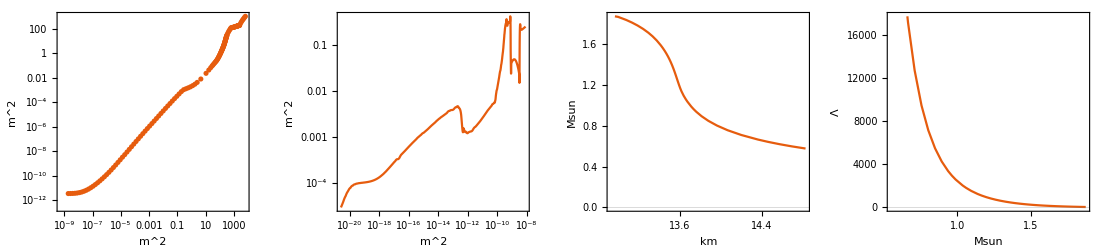

```mathematica
(* start by importing the EOS data *)
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;-1;;4,8;;9]];
centraldensities = EOSData[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicSplineInterpolation"][MRDataLimited];
ρmin=domainscaled[[1]];

EOSplot1 = ListLogLogPlot[EOSDataLimited,PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSplot = LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSderivativePlot = LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"];
MRplot = ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}];
MΛplot = ListPlot[MΛDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"Msun","Λ"}];
GraphicsRow[{EOSplot1,EOSderivativePlot,MRplot,MΛplot},ImageSize->{1100,250}]
```

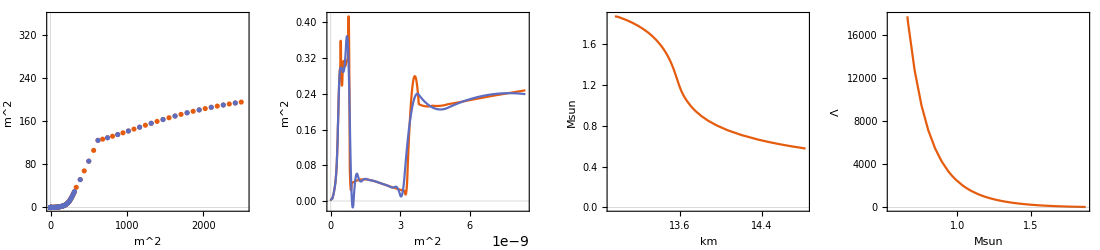

```mathematica
(* start by importing the EOS data *)
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSDatadown=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRDatadown=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimiteddown=EOSDatadown[[1;;-1;;8,8;;9]];
centraldensitiesdown = EOSDatadown[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimiteddown=MRDatadown[[1;;Dimensions[MRDatadown][[1]],{2,3}]];
MΛDataLimiteddown=MRDatadown[[1;;Dimensions[MRDatadown][[1]],{3,5}]];
pressureEOSdown=ResourceFunction["CubicSplineInterpolation"][EOSDataLimiteddown]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOSdown[ρ_]:=Evaluate[D[pressureEOSdown[ρ],ρ]];
maxdensity=Max[EOSDataLimiteddown[[1;;-1,1]]];
mindensity=Min[EOSDataLimiteddown[[1;;-1,1]]];
pressureEOS m2down[rhobar_]:=pressureEOSdown[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2down[ρ_]:=Evaluate[D[pressureEOS m2down[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfncdown=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimiteddown];
ρmin2=domainscaled[[1]];

EOSplot1 = ListPlot[{EOSDataLimited,EOSDataLimiteddown},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSplot = Plot[{pressureEOS m2[ρ],pressureEOS m2down[ρ]},{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSderivativePlot = Plot[{dpressureEOS m2[ρ],dpressureEOS m2down[ρ]},{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"];
MRplot = ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}];
MΛplot = ListPlot[MΛDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"Msun","Λ"}];
GraphicsRow[{EOSplot1,EOSderivativePlot,MRplot,MΛplot},ImageSize->{1100,250}]
```

```mathematica
ρmin
ρmin2
```

2.47866×10^-21

2.47866×10^-21

```mathematica
base = 2;
shift = 3.1;
myscales={10^5,10^-10,1};
AbsoluteTiming[MR vals = Table[RescaleMRPair km Msun[Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,(ρmin/myscales[[2]])  / (base^ρc+shift),myscales][[1]]],myscales],{ρc,Log[base,3.3-shift],Log[base,10-shift],(Log[base,10-shift]-Log[base,3.3-shift])/100}]];

myscales={10^5,10^-10,1};
AbsoluteTiming[MR valsdown = Table[RescaleMRPair km Msun[Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2down,dpressureEOS m2down,(ρmin/myscales[[2]])  / (base^ρc+shift),myscales][[1]]],myscales],{ρc,Log[base,3.3-shift],Log[base,10-shift],(Log[base,10-shift]-Log[base,3.3-shift])/100}]];
```

$Aborted

```mathematica
(Log[base,10-shift]-Log[base,3.3-shift])/100
```

0.0510852

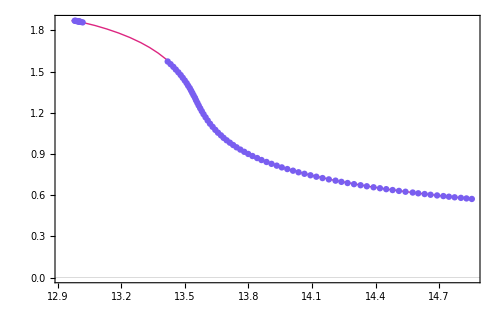

```mathematica
MRplot = ListPlot[{MRDataLimited,Re[MR vals[[All,1;;2]]](*,Re[MR valsdown[[All,1;;2]]]*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick,Dashed},{c5,Thick,Dashed},{c2,Dashed,Thick}},Joined->{True,False,False},ImageSize->{500,400},PlotRange->(*{{12.0,17.0},{0.0,2.0}}*)All,PlotLegends->Placed[{MaTeX["\\color{darkgray}\\text{Full EOS}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Downsample Factor 4}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Downsample Factor 8}",Magnification->1.0]},{Right,Top}]];
GraphicsRow[{MRplot},ImageSize->{500,400}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/MR.eos_nb0.05_G0.02_nb_0.27_G_0.06.pdf",MRplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/MR.eos_nb0.05_G0.02_nb_0.27_G_0.06.pdf

```mathematica
(mafasubs[[1]]^2/hbarGeo^2)
```

1.97686×10^-7

### Test Debora EOS

```mathematica
(* start by importing the EOS data *)
FILEBASE="debora-EOS-1";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".dat"]];
EOSDataLimited=EOSData[[1;;-1;;1,{3,2}]];
EOSDataLimited = Delete[EOSDataLimited,50];
EOSDataLimited=EOSDataLimited[[1;;-1;;1]];
pressureEOS=ResourceFunction["CubicSplineInterpolation"][EOSDataLimited];
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
ρmin=(*domainscaled[[1]]*)7.421375873877634*10^(-19);

EOSplot1 = ListLogLogPlot[EOSDataLimited(*,PlotTheme->"Scientific"*)(*,FrameLabel->{"m^2","m^2"}*)];
EOSplot = LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]}(*,PlotTheme->"Scientific"*)(*,FrameLabel->{"m^2","m^2"}*)];
EOSderivativePlot = LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},(*PlotTheme->"Scientific",*)(*FrameLabel->{"m^2","a.u."},*)PerformanceGoal->"Quality"];
GraphicsRow[{EOSplot,EOSderivativePlot},ImageSize->{600,250}]
```

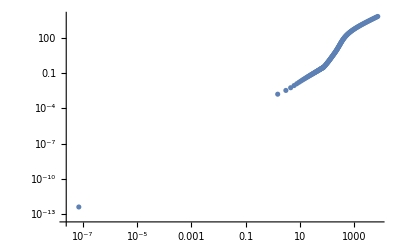

```mathematica
EOSplot1
```

```mathematica
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".dat"]];
EOSData= Delete[EOSData[[1;;-1,{3,2}]],50];
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/debora-EOS-1.csv",EOSData,"CSV"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/debora-EOS-1.csv

```mathematica
domainscaled
```

{9.33281×10^-20,9.83644×10^-9}

```mathematica
7.054364*10^-8 * MeVperfm3 2 Jperm3 * Jperm3 2 m2
```

9.33281×10^-20

```mathematica
pressureEOS m2[7.054364*10^-8 * MeVperfm3 2 Jperm3 * Jperm3 2 m2] / (MeVperfm3 2 Jperm3 * Jperm3 2 m2)
```

4.182×10^-13

```mathematica
10^4*(ρmin/myscales[[2]]) / (base^Log[base,3.3-shift]+shift)
```

Part::partd: Part specification myscales⟦2⟧ is longer than depth of object.

(2.82812×10^-16)/myscales⟦2⟧

```mathematica
pressureEOS m2[(ρmin*10^6)]/ Jperm3 2 m2 / MeVperfm3 2 Jperm3
pressureEOS m2[(ρmin*10^5)]/ Jperm3 2 m2 / MeVperfm3 2 Jperm3
pressureEOS m2[(ρmin*10^4)]/ Jperm3 2 m2 / MeVperfm3 2 Jperm3
pressureEOS m2[(ρmin*10^3)]/ Jperm3 2 m2 / MeVperfm3 2 Jperm3
```

0.000593469

0.0000609124

6.11022×10^-6

6.11147×10^-7

```mathematica
base = 2;
shift = 3.1;
myscales={10^5,10^-10,1};
AbsoluteTiming[MR vals minus0 = Table[RescaleMRPair km Msun[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,(ρmin/myscales[[2]]),myscales][[1]],myscales],{ρc,Log[base,3.3-shift],Log[base,11-shift],(Log[base,11-shift]-Log[base,3.3-shift])/100}]];
Print["done with one"];
```

done with one

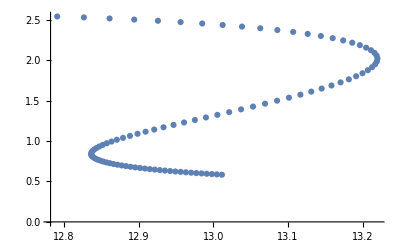

```mathematica
ListPlot[MR vals minus0]
```

```mathematica
MR vals minus1 = Table[RescaleMRPair km Msun[Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,(ρmin/myscales[[2]])*10^-1,myscales][[1]]],myscales],{ρc,Log[base,3.3-shift],Log[base,11-shift],(Log[base,11-shift]-Log[base,3.3-shift])/100}];
Print["done with two"];
```

done with two

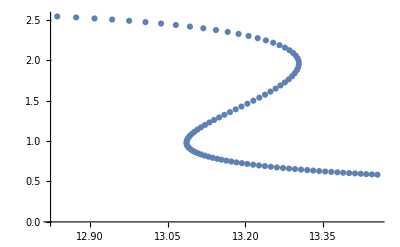

```mathematica
ListPlot[MR vals minus1]
```

```mathematica
MR vals minus2 = Table[RescaleMRPair km Msun[Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,10^-2*(ρmin/myscales[[2]]),myscales][[1]]],myscales],{ρc,Log[base,3.3-shift],Log[base,11-shift],(Log[base,11-shift]-Log[base,3.3-shift])/100}];
Print["done with two"];
```

done with two

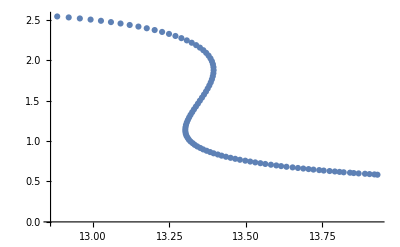

```mathematica
ListPlot[MR vals minus2]
```

```mathematica
MR vals minus3 = Table[RescaleMRPair km Msun[Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,10^-3*(ρmin/myscales[[2]]),myscales][[1]]],myscales],{ρc,Log[base,3.3-shift],Log[base,11-shift],(Log[base,11-shift]-Log[base,3.3-shift])/100}];
Print["done with two"];
```

done with two

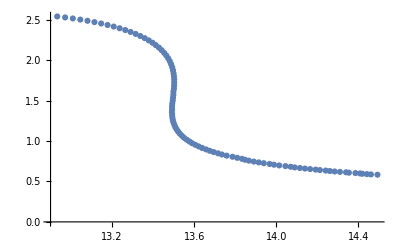

```mathematica
ListPlot[MR vals minus3]
```

```mathematica
MR vals minus14 = Table[RescaleMRPair km Msun[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,10^-4*(ρmin/myscales[[2]])  / (base^ρc+shift),myscales][[1]],myscales],{ρc,Log[base,3.3-shift],Log[base,11-shift],(Log[base,11-shift]-Log[base,3.3-shift])/100}];
Print["done with two"];
```

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at rt$128568 == 1.×10^-8.

NDSolve::ndsv: Cannot find starting value for the variable ν$128568.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at rt$128927 == 1.×10^-8.

NDSolve::ndsv: Cannot find starting value for the variable ν$128927.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at rt$129228 == 1.×10^-8.

General::stop: Further output of NDSolve::ndtol will be suppressed during this calculation.

NDSolve::ndsv: Cannot find starting value for the variable ν$129228.

General::stop: Further output of NDSolve::ndsv will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

done with two

```mathematica
ListPlot[MR vals minus14]
```

-Graphics-

```mathematica
MR vals minus12 = Table[RescaleMRPair km Msun[Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,(ρmin/myscales[[2]])  / (base^ρc+shift),myscales][[1]]],myscales],{ρc,Log[base,3.3-shift],Log[base,11-shift],(Log[base,11-shift]-Log[base,3.3-shift])/100}];
Print["done with three"];
```

done with three

```mathematica
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/MR-curve-rhof-minus10.csv"],MR vals minus10,"CSV"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/MR-curve-rhof-minus10.csv

```mathematica
Mag=1.5
```

1.5

```mathematica
xticks=Table[{j,If[Mod[j,0.2]>0.15,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{3,1}]]],Magnification->Mag],If[Mod[j,0.2]==0.0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{3,1}]]],Magnification->Mag],None]],If[Mod[j,0.2]>0.15,0.013,0.005]},{j,12.0,14.8,0.1}];
xticksNV=Table[{j,None,If[Mod[j,0.2]>0.15,0.013,0.005]},{j,12.0,14.8,0.1}];
yticks=Table[{i,If[Mod[i,0.5]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->Mag],None],If[Mod[i,0.5]==0,0.013,0.005]},{i,0.0,2.7,0.1}];
yticksNV=Table[{i,None,If[Mod[i,0.5]==0,0.013,0.005]},{i,0.0,2.7,0.1}];
```

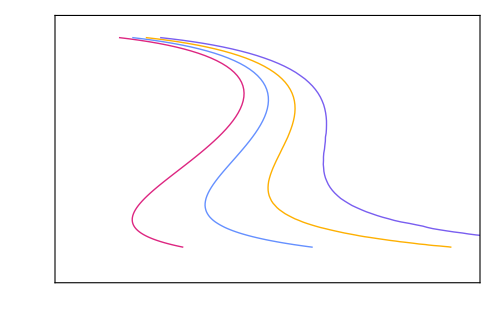

```mathematica
MRplot = ListPlot[{Re[MR vals minus0(*[[1;;94,1;;2]]*)],Re[MR vals minus1(*[[1;;94,1;;2]]*)],Re[MR vals minus2(*[[30;;94,1;;2]]*)], Re[MR vals minus3(*[[30;;94,1;;2]]*)]},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Thick}},Joined->{True},ImageSize->{500,400},PlotRange->{{12.6,14.0},{0.3,2.7}},PlotLegends->Placed[{MaTeX["\\color{darkgray}\\rho_{\\text{out}} = 10^6 \\  \\text{g} / \\text{cm}^3 \quad p_{\\text{out}} = 4.9\\times 10^{-4} \\ \\text{MeV} / \\text{fm}^3",Magnification->1.4],MaTeX["\\color{darkgray}\\rho_{\\text{out}} = 10^5 \\  \\text{g} / \\text{cm}^3 \quad p_{\\text{out}} = 6.1\\times 10^{-5} \\ \\text{MeV} / \\text{fm}^3",Magnification->1.4],MaTeX["\\color{darkgray}\\rho_{\\text{out}} = 10^4 \\ \\text{g} / \\text{cm}^3 \quad p_{\\text{out}} = 6.1\\times 10^{-6} \\ \\text{MeV} / \\text{fm}^3",Magnification->1.4],
MaTeX["\\color{darkgray}\\rho_{\\text{out}} = 10^3 \\ \\text{g} / \\text{cm}^3 \quad p_{\\text{out}} = 6.1\\times 10^{-7} \\ \\text{MeV} / \\text{fm}^3",Magnification->1.4]},{Right,Top}](*,PlotLabel->MaTeX["\\color{darkgray}\\rho_{\\text{frac}} = 10^{-12}",Magnification->2.3]*),FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}}];
GraphicsRow[{MRplot},ImageSize->{900,700}]
```

```mathematica
10^6 * (10^-3)
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/MR-varied-outer-density.pdf",MRplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/MR-varied-outer-density.pdf

```mathematica
EOSDataLimited
```

(7.05436×10^-8 | 4.182×10^-13
1.51905 | 0.00157268
3.04031 | 0.00328624
4.56257 | 0.00554396
6.0857 | 0.00848458
7.60963 | 0.0119715
9.13431 | 0.0158278
10.6597 | 0.0199585
12.1856 | 0.0243164
13.7121 | 0.0288732
15.2392 | 0.033607
16.7667 | 0.038508
18.2946 | 0.0435567
19.823 | 0.0487468
21.3518 | 0.0540713
22.881 | 0.0595162
24.4106 | 0.0650788
25.9405 | 0.0707576
27.4707 | 0.0765449
29.0013 | 0.082435
30.5321 | 0.0884297
32.0633 | 0.09453
33.5948 | 0.100733
35.1265 | 0.107037
36.6586 | 0.113441
38.1909 | 0.119948
39.7234 | 0.126561
41.2563 | 0.133282
42.7893 | 0.140118
44.3227 | 0.14707
45.8562 | 0.154144
47.39 | 0.161351
48.924 | 0.168706
50.4583 | 0.176204
51.9928 | 0.183826
53.5275 | 0.191549
55.0624 | 0.199348
56.5976 | 0.207213
58.133 | 0.215154
59.6686 | 0.22316
61.2044 | 0.231223
62.7404 | 0.239354
64.2766 | 0.247581
65.8131 | 0.255945
67.3497 | 0.26449
68.8866 | 0.273261
70.4236 | 0.282293
71.9608 | 0.291603
73.4983 | 0.301192
75.0359 | 0.311072
75.3025 | 0.312812
78.4989 | 0.345715
81.7043 | 0.382078
84.8847 | 0.422266
88.1668 | 0.466682
91.3609 | 0.515769
94.7525 | 0.570019
98.191 | 0.629976
101.702 | 0.696239
105.163 | 0.769471
108.921 | 0.850407
112.617 | 0.939856
116.4 | 1.03871
120.33 | 1.14797
124.44 | 1.26872
128.472 | 1.40216
132.722 | 1.54965
137.068 | 1.71264
141.466 | 1.89279
146.069 | 2.09188
150.772 | 2.31191
155.582 | 2.55508
160.642 | 2.82383
165.862 | 3.12085
171.326 | 3.44911
176.689 | 3.8119
182.334 | 4.21285
187.908 | 4.65598
193.772 | 5.14571
199.658 | 5.68695
205.673 | 6.28512
211.654 | 6.94621
217.87 | 7.67684
224.153 | 8.48431
230.45 | 9.37672
236.869 | 10.363
243.208 | 11.453
249.649 | 12.6577
256.126 | 13.9891
262.803 | 15.4605
269.509 | 17.0867
276.464 | 18.8839
283.514 | 20.8702
290.795 | 23.0654
298.129 | 25.4914
305.719 | 28.1727
313.336 | 31.136
321.433 | 34.411
329.683 | 38.0305
338.502 | 42.0307
347.668 | 46.4516
357.318 | 51.3375
367.317 | 56.7374
378.106 | 62.7052
389.554 | 69.3008
401.819 | 76.59
414.987 | 84.646
428.929 | 93.5494
444.038 | 103.389
460.289 | 114.264
477.955 | 126.283
497.236 | 139.566
518.008 | 154.246
540.568 | 170.47
565.126 | 188.4
591.93 | 208.217
621.411 | 230.118
653.588 | 254.322
688.815 | 281.073
727.219 | 310.637
769.552 | 343.311
815.766 | 379.421
866.656 | 419.33
922.325 | 463.437
983.629 | 512.183
1051.14 | 566.056
1125.54 | 625.595
1207.31 | 691.398
1296.28 | 764.121
1394.89 | 844.494
1502.7 | 933.321
1620.84 | 1031.49
1751.74 | 1139.99
1895.15 | 1259.89
2053.03 | 1392.41
2225.68 | 1538.87
2415.65 | 1700.74
2624.39 | 1879.63
2853.13 | 2077.33
3104.64 | 2295.83
3379.53 | 2537.31
3681.77 | 2804.2
4012.93 | 3099.15
4375.39 | 3425.13
4774.78 | 3785.4
5212.38 | 4183.56
5693.01 | 4623.6
6219.58 | 5109.93
6800.03 | 5647.41
7435.05 | 6241.42)

```mathematica
domainscaled[[2]]
```

9.83644×10^-9

```mathematica
domainscaled[[1]]
```

9.33281×10^-20

```mathematica
eosvals = Table[{ρ,pressureEOS m2[ρ]},{ρ,domainscaled[[1]],domainscaled[[2]],10^-11}];
```

```mathematica
eosvals[[1]][[2]]
eosvals[[950]][[2]]
```

5.53272×10^-25

7.93157×10^-9

```mathematica
xticks=Table[{10^i,If[Mod[i,2]==0,MaTeX[Superscript[10,i],Magnification->Mag],None],If[Mod[i,2]==0,0.013,0.005]},{i,-20,-8}];
xticksNV=Table[{10^i,If[Mod[i,2]==0,None,None],If[Mod[i,2]==0,0.013,0.005]},{i,-20,-8}];
yticks=Table[{10^i,If[Mod[i,4]==0,MaTeX[Superscript[10,i],Magnification->Mag],None],If[Mod[i,4]==0,0.013,0.005]},{i,-25,-8}];
yticksNV=Table[{10^i,If[Mod[i,4]==0,None,None],If[Mod[i,4]==0,0.013,0.005]},{i,-25,-8}];
```

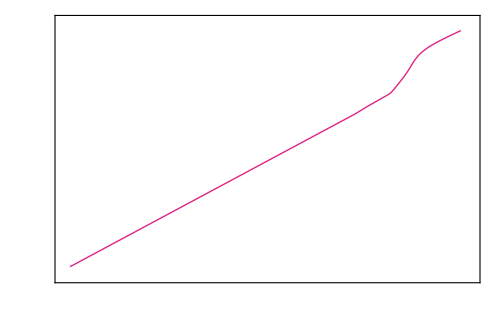

```mathematica
EOSplot = ListLogLogPlot[{eosvals},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}\\rho \\ \\left[\\text{m}^{-2} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}p \\ \\left[\\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{True},ImageSize->{500,400},PlotRange->{{0.6*10^-19,2*10^-8},{10^-25,4*10^-8}}(*,PlotLegends->Placed[{MaTeX["\\color{darkgray}\\rho_{\\text{frac}} = 10^{-8}",Magnification->1.4],MaTeX["\\color{darkgray}\\rho_{\\text{frac}} = 10^{-10}",Magnification->1.4],MaTeX["\\color{darkgray}\\rho_{\\text{frac}} = 10^{-12}",Magnification->1.4]},{Right,Top}]*)(*,PlotLabel->MaTeX["\\color{darkgray}\\rho_{\\text{frac}} = 10^{-12}",Magnification->2.3]*),FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}}];
GraphicsRow[{EOSplot},ImageSize->{500,380}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/paper-EOS.pdf",EOSplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/paper-EOS.pdf

### GetMRandΛNoAxions

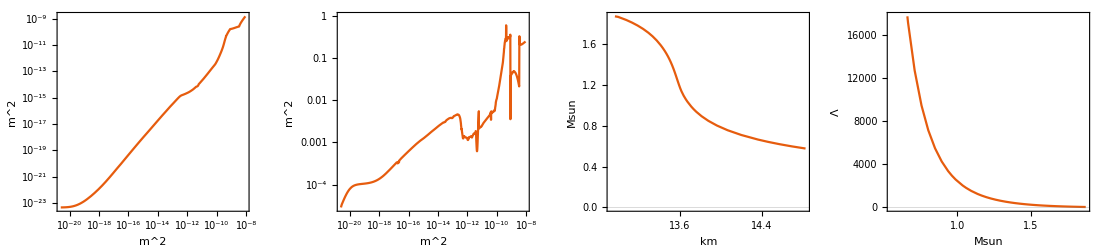

```mathematica
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;-1;;4,8;;9]];
centraldensities = EOSData[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited]
```

```mathematica
myscales={10^5,10^-10,10^1};
MRΛ vals2 = Table[RescaleMRΛTriplet km Msun dim0[Quiet[GetMRandΛNoAxions[ρc,pressureEOS m2,10^-10,myscales][[1]]],myscales],{ρc,3.0,8.5,0.1}];
```

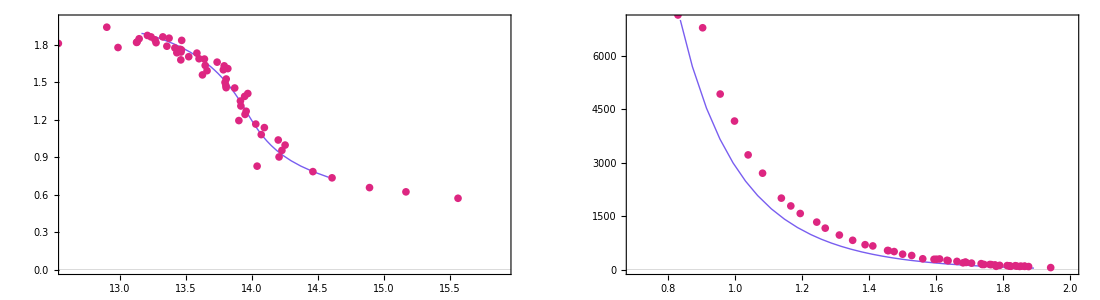

```mathematica
MRplot = ListPlot[{Re[MRΛ vals2[[All,1;;2]]],MRDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{12.6,15.9},{0.0,2.0}}(*All*)];
MΛplot = ListPlot[{Re[MRΛ vals2[[All,2;;3]]],MΛDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Lambda",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{0.7,2.0},{0.0,7000.0}}(*All*)];
GraphicsRow[{MRplot,MΛplot},ImageSize->{1100,300}]
```

### Export all mass radius functions for

```mathematica
FILEBASE="debora-EOS-1";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".dat"]];
EOSDataLimited=EOSData[[1;;-1;;4,{3,2}]];
EOSDataLimited = Delete[EOSDataLimited,13];
EOSDataLimited=EOSDataLimited[[1;;-1;;1]];
(*EOSDataLimitedyvals = MovingMedian[EOSDataLimited[[All, 2]],2];
PrependTo[EOSDataLimitedyvals,EOSDataLimited[[1,2]]];
EOSDataLimited[[1;;-1,2]] = EOSDataLimitedyvals;*)
(*EOSDataLimited[[1;;-1,2]] = GaussianFilter[EOSDataLimited[[1;;-1,2]], 2];*)
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
(*slope = (EOSDataLimited[[2]][[2]] - EOSDataLimited[[1]][[2]])/(EOSDataLimited[[2]][[1]] - EOSDataLimited[[1]][[1]]);
minimumforlineextension =den/.NSolve[EOSDataLimited[[1]][[2]] + slope*(den - mindensity)==0.0, den][[1]];
maximumforlineextension =den/.NSolve[EOSDataLimited[[1]][[2]] + slope*(den - mindensity)==EOSDataLimited[[2]][[2]], den][[1]];
Print[slope];
Print[minimumforlineextension];
newvals = Table[{den, EOSDataLimited[[1]][[2]] + slope*(den - mindensity)}, {den, minimumforlineextension,maximumforlineextension, (maximumforlineextension-minimumforlineextension)/100}];
Delete[EOSDataLimited,1];
PrependTo[EOSDataLimited, newvals];*)
pressureEOS=Interpolation[EOSDataLimited, Method->"Spline",InterpolationOrder->2];
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
ρmin=domainscaled[[1]];
(*MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited];*)
```

```mathematica
50/3//N
```

16.6667

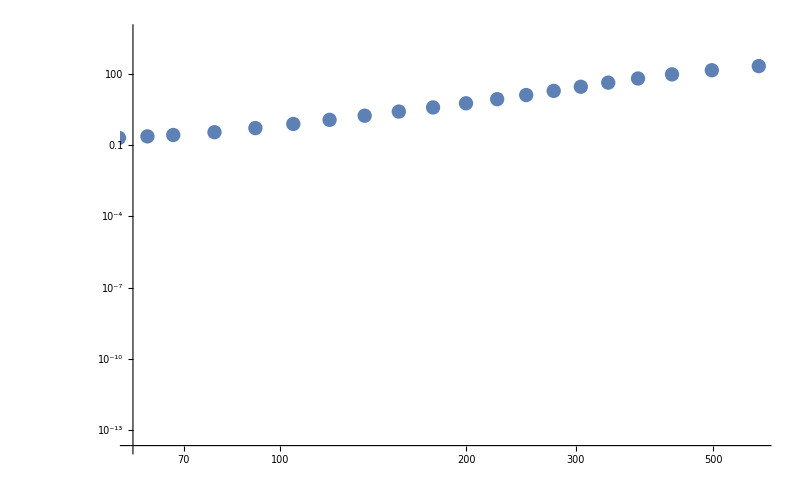

```mathematica
ListLogLogPlot[EOSDataLimited,PlotRange->{{58, 591},All}, Ticks->Automatic]
```

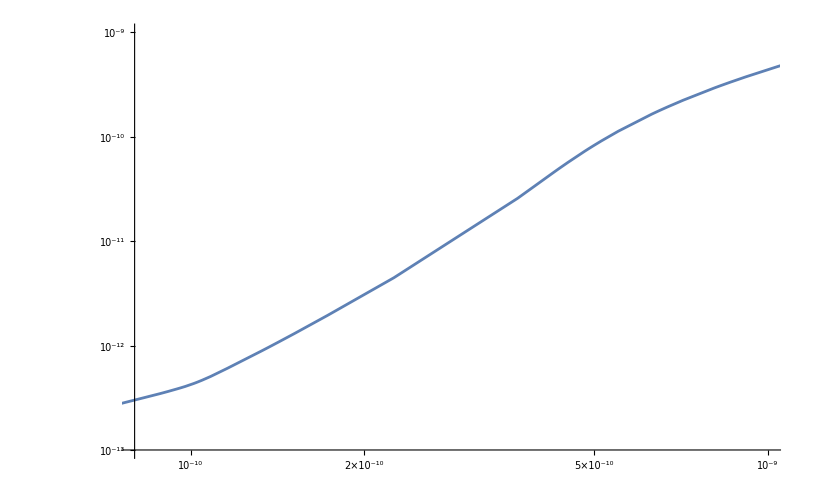

```mathematica
LogLogPlot[pressureEOS m2[rho], {rho, domainscaled[[1]], domainscaled[[2]]},PlotRange->{{8*10^-11, 10^-9},{10^-13,10^-9}}]
```

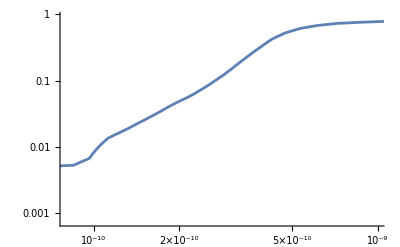

```mathematica
LogLogPlot[dpressureEOS m2[rho], {rho, domainscaled[[1]], domainscaled[[2]]},PlotRange->{{8*10^-11, 10^-9},All}]
```

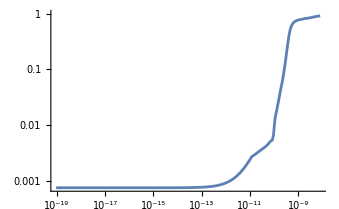

```mathematica
LogLogPlot[dpressureEOS m2[rho], {rho, domainscaled[[1]], domainscaled[[2]]}]
```

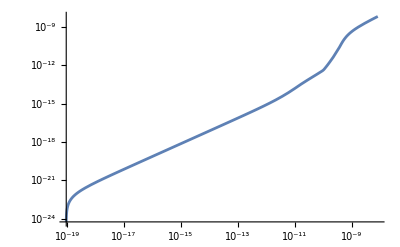

```mathematica
LogLogPlot[pressureEOS m2[rho], {rho, domainscaled[[1]], domainscaled[[2]]}]
```

```mathematica
pressureEOS
```

InterpolatingFunction[…]

```mathematica
(* I need to extend the EOS to both lower and higher density values
Zero density should be zero pressure for starters. *)
```

```mathematica
(* so the spitting out of negative pressure values is happening because the EOS has a limited domain. *)
```

```mathematica
EOSmetersvals = Table[{domainscaled[[1]]+(domainscaled[[2]] - domainscaled[[1]])*q/200000, pressureEOS m2[domainscaled[[1]]+(domainscaled[[2]] - domainscaled[[1]])*q/200000]},{q, 0, 200000}];
dEOSmetersvals = Table[{domainscaled[[1]]+(domainscaled[[2]] - domainscaled[[1]])*q/200000, dpressureEOS m2[domainscaled[[1]]+(domainscaled[[2]] - domainscaled[[1]])*q/200000]},{q, 0, 200000}];
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/EOS-1-m2.csv",EOSmetersvals,"CSV"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/dEOSdrho-1-m2.csv",dEOSmetersvals,"CSV"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/dEOSdrho-1-m2.csv

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/EOS-1-m2-no-interpolation.csv",EOSDataLimited *(MeVperfm3 2 Jperm3*Jperm3 2 m2),"CSV"];
```

```mathematica
pressureEOS[maxdensity]
```

6241.42

```mathematica
base = 2;
shift = 3.1;
myscales={10^5,10^-10,1};
Npoints=100;
```

```mathematica
massradiusvals = {};
centraldensitybases = {};
```

```mathematica
Module[{mrmρ vals,ρc,i,massfnc,densityfnc,nufnc,densityin,pressurefnc,densityvals,pressurevals,massvals,nuvals},
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
mrmρ vals = Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,(*10*(ρmin/myscales[[2]])  / (base^ρc+shift)*)10^-12,myscales]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
nufnc[r_]:=Evaluate[mrmρ vals[[2]][[3]][r]];
densityin[r_]:=Evaluate[mrmρ vals[[2]][[4]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
densityvals = Quiet[Table[{r*myscales[[1]], densityfnc[r]*myscales[[2]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
(*Print[densityvals[[-1]]];*)
pressurevals = Quiet[Table[{r*myscales[[1]], pressurefnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
(*Print[pressurevals[[-1]]];*)
massvals = Quiet[Table[{r*myscales[[1]], massfnc[r]*myscales[[3]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
nuvals = Quiet[Table[{r*myscales[[1]], nufnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/density-vals-rhoc-",ToString[i],".csv"],densityvals,"CSV"];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/pressure-vals-rhoc-",ToString[i],".csv"],pressurevals,"CSV"];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/mass-vals-rhoc-",ToString[i],".csv"],massvals,"CSV"];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/nu-vals-rhoc-",ToString[i],".csv"],nuvals,"CSV"];
AppendTo[massradiusvals,{mrmρ vals[[1]][[1]]*myscales[[1]], mrmρ vals[[1]][[2]]*myscales[[3]]}];
AppendTo[centraldensitybases,(base^ρc + shift)*myscales[[2]]]]]
```

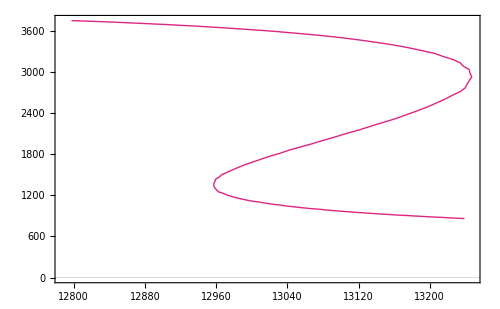

```mathematica
MRplot = ListPlot[massradiusvals,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick,Dashed},{c5,Thick,Dashed},{c2,Dashed,Thick}},Joined->{True},ImageSize->{500,400},PlotRange->(*{{12.0,17.0},{0.0,2.0}}*)All,(*PlotLegends->Placed[{MaTeX["\\color{darkgray}\\text{Full EOS}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Downsample Factor 4}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Downsample Factor 8}",Magnification->1.0]},{Right,Top}],*)PlotLabel->MaTeX["\\color{darkgray}\\rho_{\\text{frac}} = \\rho_{\\text{min}} / \\rho_c",Magnification->2.3]];
GraphicsRow[{MRplot},ImageSize->{500,400}]
```

```mathematica
4000 * 2.5 / clight
```

0.0000333564

```mathematica
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/MR-vals.csv"],massradiusvals,"CSV"];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/central-density-vals.csv"],centraldensitybases,"CSV"];
```

```mathematica
NSolve[(-σN*ρmin*hbarGeo^3/(mN*mpi^2*fpi^2*GeV2m^4)+epsilon)==0, epsilon]
```

{{epsilon→1.10543×10^-10}}

```mathematica
maxr = massradiusvals[[1]][[1]];
minr = massradiusvals[[95]][[1]];
```

```mathematica
maxr
minr
```

13.4091

12.8321

```mathematica
myticks =Table[{i, MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->1.5]},{i,12.8,13.6,0.1}];
```

```mathematica
mybarlegend = BarLegend[{Blend[{{minr,c1},{minr + (maxr-minr)/4,c2},{minr+ (maxr-minr)*2/4,c3},{minr+ (maxr-minr)*3/4,c4},{maxr,c5}},#]&,{minr,maxr}},Ticks->myticks,LegendMarkerSize->700]
```

```mathematica
massfunctionsets = {};
```

```mathematica
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
AppendTo[massfunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/mass-vals-rhoc-",ToString[ρc],".csv"],"CSV"]]
]
```

```mathematica
For[i=1,i<=95,i++,For[j=1,j<=10000,j++,massfunctionsets[[i]][[j]] = RescaleMRPair km Msun from file[massfunctionsets[[i]][[j]]]]]
```

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[3]]],{i, 1, Npoints}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.004]},{i,1,Npoints}];
```

Part::partd: Part specification massradiusvals⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Mag=1.4;
```

```mathematica
Clear[j]
```

```mathematica
xticks=Table[{j,If[Mod[j,2]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{3,1}]]],Magnification->Mag],None],If[Mod[j,2]==0,0.013,0.005]},{j,0.0,maxr,0.5}];
xticksNV=Table[{j,None,If[Mod[j,2]==0,0.013,0.005]},{j,0.0,maxr,0.5}];
yticks=Table[{i,If[Mod[i,0.5]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->Mag],None],If[Mod[i,0.5]==0,0.013,0.005]},{i,0.0,2.6,0.1}];
yticksNV=Table[{i,None,If[Mod[i,0.5]==0,0.013,0.005]},{i,0.0,2.6,0.1}];
```

$Aborted

$Aborted

```mathematica
allmassfunctionsimg = ListPlot[massfunctionsets[[1;;95]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} M(r) \\left[ M_{\\odot} \\right]",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,13.3},All}]
```

```mathematica
densityfunctionsets = {};
```

```mathematica
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
AppendTo[densityfunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/density-vals-rhoc-",ToString[ρc],".csv"],"CSV"]]
]
```

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]] - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]] - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]] - minr) / (maxr-minr)][[3]]],{i, 1, Npoints}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,Npoints}];
```

```mathematica
yticks=Table[{j*10^-10,If[Mod[j,2]==0,If[j==0,MaTeX[StringJoin["\\color{darkgray} 0.0"],Magnification->Mag],MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{1,1}]](*, "\\color{darkgray} \\times 10^{-10}"*)],Magnification->Mag]],None],If[Mod[j,1]==0,0.013,0.005]},{j,0,9,0.5}];
yticksNV=Table[{j*10^-10,None,If[Mod[j,1]==0,0.013,0.005]},{j,0,9,0.5}];
```

```mathematica
alldensityfncsimg = ListPlot[densityfunctionsets[[1;;95]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\rho(r) \\left[ 10^{-10} \\ \\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,13.3},All}]
```

$Aborted

```mathematica
ListPlot[densityfunctionsets[[1]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\rho(r) \\left[ 10^{-10} \\ \\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,13.3},All}]
```

$Aborted

```mathematica
pressurefunctionsets = {};
```

```mathematica
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
AppendTo[pressurefunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/pressure-vals-rhoc-",ToString[ρc],".csv"],"CSV"]]
]
```

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[3]]],{i, 1, Npoints}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,Npoints}];
```

```mathematica
yticks=Table[{j*10^-10,If[Mod[j,1]==0,If[j==0,MaTeX[StringJoin["\\color{darkgray} 0.0"],Magnification->Mag],MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{1,1}]](*, "\\color{darkgray} \\times 10^{-10}"*)],Magnification->Mag]],None],If[Mod[j,1]==0,0.013,0.005]},{j,0,4,0.5}];
yticksNV=Table[{j*10^-10,None,If[Mod[j,1]==0,0.013,0.005]},{j,0,4,0.5}];
```

```mathematica
allpressurefncsimg = ListPlot[pressurefunctionsets[[1;;95]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} p(r) \\left[10^{-10} \\ \\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,13.3},All}]
```

-Graphics-

```mathematica
nufunctionsets = {};
```

```mathematica
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
AppendTo[nufunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/nu-vals-rhoc-",ToString[i],".csv"],"CSV"]]
]
```

```mathematica
For[i=1,i<=95,i++,For[j=1,j<=10000,j++,nufunctionsets[[i]][[j]][[1]] =nufunctionsets[[i]][[j]][[1]]/10^3]]
```

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]] - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]] - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]] - minr) / (maxr-minr)][[3]]],{i, 1, Npoints}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,Npoints}];
```

```mathematica
yticks=Table[{i,If[Mod[i,0.5]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->Mag],None],If[Mod[i,0.5]==0,0.013,0.005]},{i,-2,1.0,0.1}];
yticksNV=Table[{i,None,If[Mod[i,0.5]==0,0.013,0.005]},{i,-2,1.0,0.1}];
```

```mathematica
allnufncsimg = ListPlot[nufunctionsets[[1;;95]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\nu(r)",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,13.3},All}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/all-nu-fncs-debora-EOS-1.pdf",allnufncsimg,"PDF"];
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/all-mass-fncs-debora-EOS-1.pdf",allmassfunctionsimg,"PDF"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/all-density-fncs-debora-EOS-1.pdf",alldensityfncsimg,"PDF"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/all-pressure-fncs-debora-EOS-1.pdf",allpressurefncsimg,"PDF"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/all-nu-fncs-debora-EOS-1.pdf",allnufncsimg,"PDF"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/all-fncs-colorbar.pdf",mybarlegend,"PDF"];
```

```mathematica
deltafunctionsets = {};
massfunctionsets = {};
```

```mathematica
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
AppendTo[massfunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/mass-vals-rhoc-",ToString[ρc],".csv"],"CSV"]]
]
```

```mathematica
For[i=1, i<=Npoints,i++,AppendTo[deltafunctionsets,Table[{massfunctionsets[[i]][[j]][[1]],1 - 2*massfunctionsets[[i]][[j]][[2]]/(massfunctionsets[[i]][[j]][[1]]*10^3)},{j,1, Dimensions[massfunctionsets[[1]]][[1]]}]]]
```

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[3]]],{i, 1, Npoints}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,Npoints}];
```

```mathematica
Mod[0.4,0.2]
```

0.

```mathematica
yticks=Table[{i,If[Mod[i,0.2]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->Mag],None],If[Mod[i,0.2]==0,0.013,0.005]},{i,0.3,1.0,0.05}];
yticksNV=Table[{i,None,If[Mod[i,0.2]==0,0.013,0.005]},{i,0.3,1.0,0.05}];
```

```mathematica
alldeltafncsimg = ListPlot[deltafunctionsets[[1;;95]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\lambda(r)",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,13.3},{0.3,1.05}}]
```

-Graphics-

### Make plot of maximum epsilon for the MR curve with the EOS above

```mathematica
base = 2;
shift = 3.1;
centraldensitybases = Table[Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100, {i, 0, 99}];
```

```mathematica
centraldensitybases
```

{-2.32193,-2.26889,-2.21585,-2.16281,-2.10978,-2.05674,-2.0037,-1.95066,-1.89763,-1.84459,-1.79155,-1.73851,-1.68547,-1.63244,-1.5794,-1.52636,-1.47332,-1.42029,-1.36725,-1.31421,-1.26117,-1.20813,-1.1551,-1.10206,-1.04902,-0.995983,-0.942945,-0.889907,-0.836869,-0.783832,-0.730794,-0.677756,-0.624718,-0.57168,-0.518643,-0.465605,-0.412567,-0.359529,-0.306491,-0.253454,-0.200416,-0.147378,-0.0943402,-0.0413024,0.0117354,0.0647732,0.117811,0.170849,0.223887,0.276924,0.329962,0.383,0.436038,0.489076,0.542114,0.595151,0.648189,0.701227,0.754265,0.807303,0.86034,0.913378,0.966416,1.01945,1.07249,1.12553,1.17857,1.23161,1.28464,1.33768,1.39072,1.44376,1.49679,1.54983,1.60287,1.65591,1.70895,1.76198,1.81502,1.86806,1.9211,1.97413,2.02717,2.08021,2.13325,2.18629,2.23932,2.29236,2.3454,2.39844,2.45147,2.50451,2.55755,2.61059,2.66363,2.71666,2.7697,2.82274,2.87578,2.92881}

```mathematica
densityfunctionsets = {};
```

```mathematica
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
AppendTo[densityfunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/density-vals-rhoc-",ToString[ρc],".csv"],"CSV"]]
]
```

```mathematica
MRvals = Import["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/MR-curve-rhof-minus10.csv", "CSV"];
```

```mathematica
maxepslist = {};
```

```mathematica
Module[{i, myfnc, eps,maxeps},
For[i=1, i<=95, i++,
myfnc = Interpolation[densityfunctionsets[[i]]];
mysol=NSolve[-σN*myfnc[MRvals[[i]][[1]]]*hbarGeo^3 / (mN*mpi^2*fpi^2*GeV2m^4) + eps==0.0, eps];
maxeps = eps/.mysol[[1]];
AppendTo[maxepslist, {MRvals[[i]][[2]], maxeps}]
]
]
```

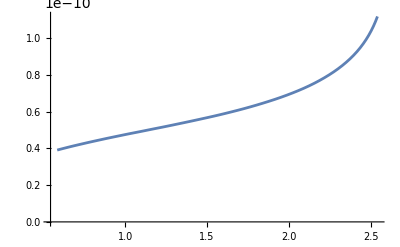

```mathematica
ListPlot[maxepslist, Joined->True]
```

```mathematica
myfnc = Interpolation[densityfunctionsets[[61]]];
mysol=NSolve[-σN*myfnc[MRvals[[61]][[1]]]*hbarGeo^3 / (mN*mpi^2*fpi^2*GeV2m^4) + eps==0.0, eps]
```

{{eps→5.82217×10^-11}}

### Getaxionfieldfrompython and getaxionenergypressureandmassfrompython

```mathematica
ϵ=0.005;
fasub=10^16;
mafasubs = {Sqrt[fpi^2*mpi^2*ϵ/(2*fasub^2)],fasub}*GeV2m;
```

```mathematica
myscales[[1]]
```

100000

```mathematica
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;-1;;4,8;;9]];
centraldensities = EOSData[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited];
```

```mathematica
myscales={10^5,10^-10,1};
mrmρ vals = Quiet[GetGenericMassRadius[4.5,pressureEOS m2,dpressureEOS m2,RHOFRAC,myscales]];
```

```mathematica
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
nufnc[r_]:=Evaluate[mrmρ vals[[2]][[3]][r]];
densityin[r_]:=Evaluate[mrmρ vals[[2]][[4]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
```

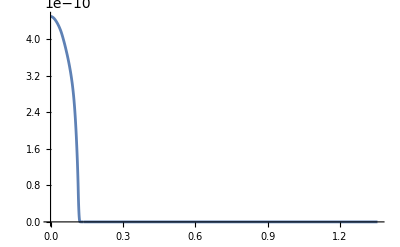

```mathematica
Plot[densityfnc[r]*myscales[[2]],{r,RSTART, 10*mrmρ vals[[1]][[1]]}]
```

```mathematica
densityvals = Quiet[Table[{r*myscales[[1]], densityfnc[r]*myscales[[2]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
pressurevals = Quiet[Table[{r*myscales[[1]], pressurefnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
massvals = Quiet[Table[{r*myscales[[1]], massfnc[r]*myscales[[3]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
nuvals = Quiet[Table[{r*myscales[[1]], nufnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
```

```mathematica
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
nufnc[r_]:=Evaluate[mrmρ vals[[2]][[3]][r]];
densityin[r_]:=Evaluate[mrmρ vals[[2]][[4]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/density-vals.csv",densityvals,"CSV"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/pressure-vals.csv",pressurevals,"CSV"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/mass-vals.csv",massvals,"CSV"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/nu-vals.csv",nuvals,"CSV"];
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/radius-mass.csv",{mrmρ vals[[1]][[1]]*myscales[[1]], mrmρ vals[[1]][[2]]*myscales[[3]]},"CSV"];
```

```mathematica
densitynormvals=Table[{r*myscales[[1]]/10^3,densityfnc[r] / densityfnc[0.01*mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
densityvals=Table[{r*myscales[[1]]/10^3,densityfnc[r]*myscales[[2]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
densityderivativevals=Table[{r*myscales[[1]]/10^3,Derivative[1][densityfnc][r]*myscales[[2]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/10000}]//Quiet;
pressurenormvals=Table[{r*myscales[[1]]/10^3,pressurefnc[r] / pressurefnc[0.01*mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
pressurevals=Table[{r*myscales[[1]]/10^3,pressurefnc[r]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
massnormvals=Table[{r*myscales[[1]]/10^3,massfnc[r]/massfnc[mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
expansionparametervals = Table[{r*myscales[[1]]/10^3,densityfnc[r]*myscales[[2]]*hbarGeo^3*σN/(mpi^2*fpi^2*mN*GeV2m^4)},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
```

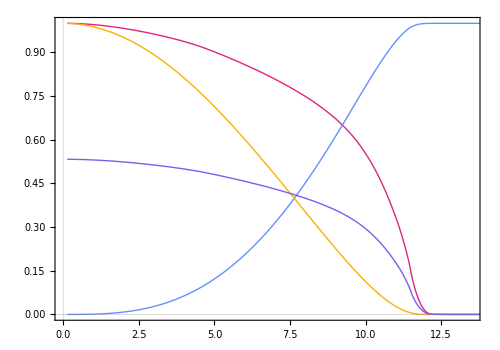

```mathematica
massdensityplot= ListPlot[{densitynormvals,massnormvals,pressurenormvals,expansionparametervals},Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r/r_{\\rm NS} \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho(r)",Magnification->1.5],MaTeX["\\color{darkgray}m(r)",Magnification->1.5],MaTeX["\\color{darkgray}p(r)",Magnification->1.5],MaTeX["\\color{darkgray}\\frac{\\sigma_N \\rho_N}{m_{\\pi} f_{\\pi} m_N}",Magnification->1.5]},PlotRange->{{0.0,mrmρ vals[[1]][[1]]*myscales[[1]]/10^3},All}]
```

```mathematica
axionandderivatives = GetAxionFieldFromPython["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/time-evolved-axion-field-small-epsilon-200-rpoints.csv"]
```

imported file

parsed file

InterpolatingFunction[…]

{axionf$134192,daxiondtfnc$134192,daxiondrfnc$134192}

```mathematica
axionfieldfnc[tbar_, rbar_]:=Evaluate[axionandderivatives[[1]][tbar*myscales[[1]], rbar*myscales[[1]]]]
daxionfielddtfnc[tbar_, rbar_]:=Evaluate[axionandderivatives[[2]][tbar*myscales[[1]], rbar*myscales[[1]]]*myscales[[1]]]
daxionfielddrfnc[tbar_, rbar_]:=Evaluate[axionandderivatives[[3]][tbar*myscales[[1]], rbar*myscales[[1]]]*myscales[[1]]]
```

```mathematica
tval = 661000/myscales[[1]]//N
```

6.61

```mathematica
1.115*5.99
```

6.67885

```mathematica
axionfieldfnc[11.98,0.06]
```

-52592.2

```mathematica
mrmρ vals[[1]][[2]] *
```

2734.56

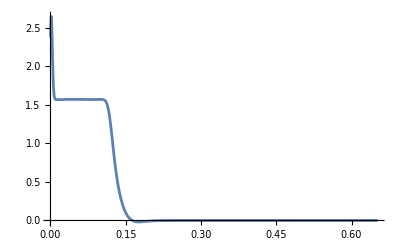

```mathematica
Plot[axionfieldfnc[tval,r],{r,0.0001,5*mrmρ vals[[1]][[1]]},PlotRange->All]
```

```mathematica
axionpressuredensitysols = GetAxionEnergyPressureAndMassFromPython[axionfieldfnc,daxionfielddtfnc,daxionfielddrfnc,mrmρ vals[[1]],massfnc,densityfnc,nufnc,mafasubs[[1]],mafasubs[[2]],myscales,tval]
```

InterpolatingFunction::dmval: Input value {-16.2419} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-16.2419} and/or the interpolation grid is insufficient to compute the value.

FindRoot::nlnum: The function value … is not a list of numbers with dimensions {1} at {rt$140290} = {-16.2419}.

InterpolatingFunction::dprec: The precision of input value {-0.217608} and/or the interpolation grid is insufficient to compute the value.

FindRoot::nlnum: The function value … is not a list of numbers with dimensions {1} at {rt$140290} = {-0.217608}.

{{ρasol$140290,pasol$140290,paangularsol$140290,Masol$140290,ρakinetic$140290,ρapotential$140290,vascaled$140290},{0.693546,0.277878}}

```mathematica
rhoafnc[r_]:=Evaluate[axionpressuredensitysols[[1]][[1]][r]];
pafnc[r_]:=Evaluate[axionpressuredensitysols[[1]][[2]][r]];
paθϕfnc[r_]:=Evaluate[axionpressuredensitysols[[1]][[3]][r]];
Mafnc[r_]:=Evaluate[axionpressuredensitysols[[1]][[4]][r]];
rhoakineticfnc[r_]:=Evaluate[axionpressuredensitysols[[1]][[5]][r]];
rhoarderivfnc[r_]:=Evaluate[axionpressuredensitysols[[1]][[6]][r]];
rhoapotentialfnc[r_]:=Evaluate[axionpressuredensitysols[[1]][[7]][r]];
```

```mathematica
rhoafncvals=Table[{r*myscales[[1]]/10^3,rhoafnc[r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
rhoakineticfncvals=Table[{r*myscales[[1]]/10^3,rhoakineticfnc[r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
rhoarderivfncvals=Table[{r*myscales[[1]]/10^3,rhoarderivfnc[r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
rhoapotentialfncvals=Table[{r*myscales[[1]]/10^3,rhoapotentialfnc[r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
```

General::munfl: 6.27952×10^-12 2.50118×10^-297 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.27952×10^-12 1.47702×10^-305 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.×10^-12 1.09029×10^-302 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-714.242] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-733.189] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-752.136] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 6.27952×10^-12 2.50118×10^-297 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.27952×10^-12 1.47702×10^-305 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.×10^-12 1.09029×10^-302 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

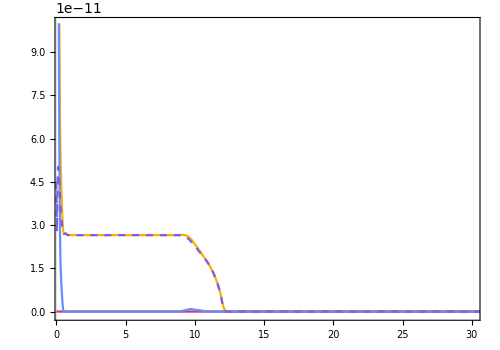

```mathematica
axionfieldvalsplot = ListPlot[{rhoafncvals,rhoakineticfncvals,rhoarderivfncvals,rhoapotentialfncvals},PlotRange->{{0.5,30},{-10^-12, 10^-10}},Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\theta = \\frac{a}{2 f_a} \\ \\left[ \\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c1,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho_a",Magnification->2.0],MaTeX["\\color{darkgray} \\text{kinetic}",Magnification->2.0],MaTeX["\\color{darkgray} \\text{potential r deriv.}",Magnification->2.0],MaTeX["\\color{darkgray} \\text{potential}",Magnification->2.0]},PlotLabel->MaTeX["\\color{darkgray} \\epsilon = 0.5",Magnification->2.0]]
```

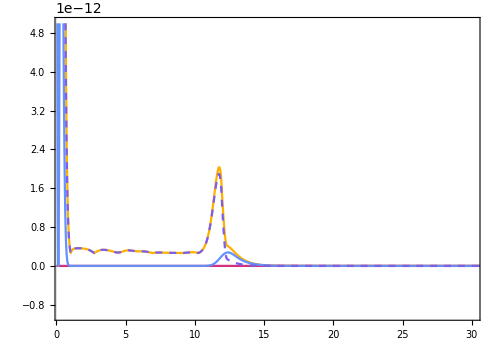

```mathematica
axionfieldvalsplot = ListPlot[{rhoafncvals,rhoakineticfncvals,rhoarderivfncvals,rhoapotentialfncvals},PlotRange->{{0.5,30},{-10^-12, 5*10^-12}},Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\theta = \\frac{a}{2 f_a} \\ \\left[ \\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c1,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho_a",Magnification->2.0],MaTeX["\\color{darkgray} \\text{kinetic}",Magnification->2.0],MaTeX["\\color{darkgray} \\text{potential r deriv.}",Magnification->2.0],MaTeX["\\color{darkgray} \\text{potential}",Magnification->2.0]},PlotLabel->MaTeX["\\color{darkgray} \\epsilon = 0.005",Magnification->2.0]]
```

```mathematica
(* for ϵ = 0.5 *)
Mafnc[mrmρ vals[[1]][[1]]]/massfnc[mrmρ vals[[1]][[1]]]
```

0.0571218

```mathematica
(* for ϵ = 0.005 *)
Mafnc[mrmρ vals[[1]][[1]]]/massfnc[mrmρ vals[[1]][[1]]]
```

0.00188606

```mathematica
thetafncvals=Table[{r*myscales[[1]]/10^3,axionfieldfnc[tval,r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
thetaprimefncvals=Table[{r*myscales[[1]]/10^3,daxionfielddrfnc[tval,r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
thetatimeprimefncvals=Table[{r*myscales[[1]]/10^3,daxionfielddtfnc[tval,r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
```

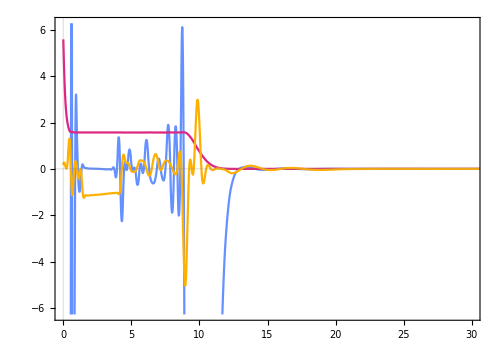

```mathematica
axionfieldvalsplot = ListPlot[{thetaprimefncvals,thetafncvals,thetatimeprimefncvals},PlotRange->{{0,30},{-2*Pi,2*Pi}},Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\theta = \\frac{a}{2 f_a} \\ \\left[ \\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c1,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}d\\theta/dr",Magnification->2.0],MaTeX["\\color{darkgray} \\theta",Magnification->2.0],MaTeX["\\color{darkgray} d\\theta / dt",Magnification->2.0]},PlotLabel->MaTeX["\\color{darkgray} \\epsilon = 0.5",Magnification->2.0]]
```

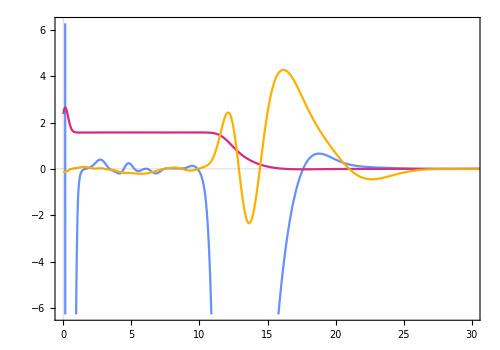

```mathematica
axionfieldvalsplot = ListPlot[{thetaprimefncvals,thetafncvals,thetatimeprimefncvals},PlotRange->{{0,30},{-2*Pi,2*Pi}},Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\theta = \\frac{a}{2 f_a} \\ \\left[ \\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c1,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}d\\theta/dr",Magnification->2.0],MaTeX["\\color{darkgray} \\theta",Magnification->2.0],MaTeX["\\color{darkgray} d\\theta / dt",Magnification->2.0]},PlotLabel->MaTeX["\\color{darkgray} \\epsilon = 0.005",Magnification->2.0]]
```

```mathematica
(* there's still an issue with the divergence at small r *)
(* I think that the bump in potential comes from the fact that the potential is not actually minimized in the transition region *)
```

### GetAxionField

```mathematica
ϵ=(*0.4*)0.0005;
fasub=10^16;
mafasubs = {Sqrt[fpi^2*mpi^2*ϵ/(2*fasub^2)],fasub}*GeV2m;
```

```mathematica
mafasubs[[1]] / GeV2m
```

2.77443×10^-20

```mathematica
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;-1;;4,8;;9]];
centraldensities = EOSData[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited];
```

```mathematica
myscales={10^5,10^-10,1};
mrmρ vals = Quiet[GetGenericMassRadius[3.0,pressureEOS m2,dpressureEOS m2,RHOFRAC,myscales]];
```

```mathematica
densityvals = Table[{r*myscales[[1]], densityfnc[r]*myscales[[2]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}];
pressurevals = Table[{r*myscales[[1]], pressurefnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}];
massvals = Table[{r*myscales[[1]], massfnc[r]*myscales[[3]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}];
nuvals = Table[{r*myscales[[1]], nufnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}];
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/density-vals.csv",densityvals,"CSV"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/pressure-vals.csv",pressurevals,"CSV"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/mass-vals.csv",massvals,"CSV"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/nu-vals.csv",nuvals,"CSV"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/radius-mass.csv",{mrmρ vals[[1]][[1]]*myscales[[1]], mrmρ vals[[1]][[2]]*myscales[[3]]},"CSV"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/density-vals.csv

/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/pressure-vals.csv

/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/mass-vals.csv

/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/nu-vals.csv

/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/radius-mass.csv

```mathematica
densitynormvals=Table[{r*myscales[[1]]/10^3,densityfnc[r] / densityfnc[0.01*mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
densityvals=Table[{r*myscales[[1]]/10^3,densityfnc[r]*myscales[[2]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
densityderivativevals=Table[{r*myscales[[1]]/10^3,Derivative[1][densityfnc][r]*myscales[[2]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/10000}]//Quiet;
pressurenormvals=Table[{r*myscales[[1]]/10^3,pressurefnc[r] / pressurefnc[0.01*mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
pressurevals=Table[{r*myscales[[1]]/10^3,pressurefnc[r]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
massnormvals=Table[{r*myscales[[1]]/10^3,massfnc[r]/massfnc[mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
expansionparametervals = Table[{r*myscales[[1]]/10^3,densityfnc[r]*myscales[[2]]*hbarGeo^3*σN/(2*mpi^2*fpi^2*mN*GeV2m^4)},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
```

```mathematica
mrmρ vals[[1]][[1]]
```

0.16536

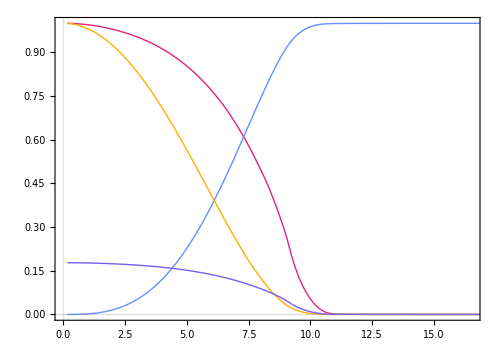

```mathematica
massdensityplot= ListPlot[{densitynormvals,massnormvals,pressurenormvals,expansionparametervals},Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r/r_{\\rm NS} \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho(r)",Magnification->1.5],MaTeX["\\color{darkgray}m(r)",Magnification->1.5],MaTeX["\\color{darkgray}p(r)",Magnification->1.5],MaTeX["\\color{darkgray}\\frac{\\sigma_N \\rho_N}{m_{\\pi} f_{\\pi} m_N}",Magnification->1.5]},PlotRange->{{0.0,mrmρ vals[[1]][[1]]*myscales[[1]]/10^3},All}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/normalized-mass-and-density.pdf",massdensityplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/normalized-mass-and-density.pdf

```mathematica
thetathetaprime vals = GetAxionField[mrmρ vals[[1]],massfnc,densityfnc,pressurefnc,mafasubs[[1]],mafasubs[[2]],myscales];
```

0.543301

10.

$Aborted

```mathematica
thetafnc[r_]:=Evaluate[thetathetaprime vals[[1]][[1]][r]];
thetafncprime[r_]:=Evaluate[thetathetaprime vals[[1]][[2]][r]];
```

```mathematica
thetafncvals=Table[{r*myscales[[1]]/10^3,thetafnc[r]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
(*thetaprimefncvalscheck=Table[{r*myscales[[1]]/10^3,thetafnc'[r]},{r,0.0001,10*mrmρ vals[[1]][[1]],0.0001}];*)
thetaprimefncvals=Table[{r*myscales[[1]]/10^3,thetafncprime[r]/myscales[[1]]},{r,0.0001,5*mrmρ vals[[1]][[1]],0.0001}];
```

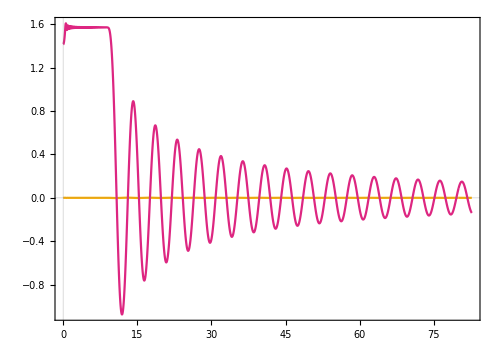

```mathematica
axionfieldvalsplot = ListPlot[{thetaprimefncvals,thetafncvals},PlotRange->(*{{0,16},{-0.1,2*Pi}}*)All,Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\theta = \\frac{a}{2 f_a} \\ \\left[ \\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c1,Thick,Dashed},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\theta'",Magnification->2.0],MaTeX["\\color{darkgray}100 \\times \\theta",Magnification->2.0]}]
```

```mathematica
thetafncvalsnearpiover2init=Table[{r*myscales[[1]]/10^3,thetafnc[r]},{r,0.001,5*mrmρ vals[[1]][[1]],0.00001}];
```

```mathematica
thetafncvalspiover4init=Table[{r*myscales[[1]]/10^3,thetafnc[r]},{r,0.001,5*mrmρ vals[[1]][[1]],0.00001}];
```

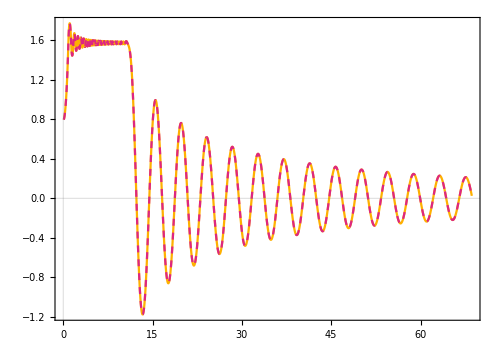

```mathematica
ListPlot[{thetafncvalsnearpiover2init,thetafncvalspiover4init},PlotRange->(*{{0,20},All}*)All,Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\theta = \\frac{a}{2 f_a} \\ \\left[ \\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick,Dashed},{c1,Thick,Dashed},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\theta'",Magnification->2.0],MaTeX["\\color{darkgray}100 \\times \\theta",Magnification->2.0]}]
```

```mathematica
(* why is it enveloping at pi/2 and not 0? *)
(* why is the derivative so weird. Based on θ, θ' should look very different. *)
(* the derivative is fine. potentially a wrong sign in the potential is leading to weird envelope behavior *)
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-field-nearpiover2-initial-condition.pdf",%,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-field-nearpiover2-initial-condition.pdf

### GetAxionEnergyPressureAndMass

```mathematica
axiondensitypressuremass fncs = GetAxionEnergyPressureAndMass[thetafnc,thetafncprime,mrmρ vals[[1]],massfnc,densityfnc,nufnc,mafasubs[[1]],mafasubs[[2]],myscales];
```

```mathematica
axiondensitypressuremass fncs[[2]][[1]]
mrmρ vals[[1]]
```

1.37236

{0.137236,1437.2}

```mathematica
axionmassfnc[mrmρ vals[[1]][[1]]]
```

51.3437

```mathematica
axiondensityfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[1]][r]];
axionpressurefnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[2]][r]];
axionmassfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[3]][r]];
axionkineticfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[4]][r]];
axionpotentialfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[5]][r]];
```

```mathematica
RHOFRAC=10^-3;
r/.FindRoot[(axiondensityfnc[r]+densityfnc[r]*myscales[[2]])==(axiondensityfnc[RSTART]+densityfnc[RSTART]*myscales[[2]])*RHOFRAC,{r,RSTART,mrmρ vals[[1]][[1]]}][[1]]
```

0.362968

```mathematica
axiondensityvals=Table[{r*myscales[[1]]/10^3,axiondensityfnc[r]},{r,0.001,10*mrmρ vals[[1]][[1]],0.00001}]//Quiet;
axionpressurevals=Table[{r*myscales[[1]]/10^3,axionpressurefnc[r]},{r,0.001,10*mrmρ vals[[1]][[1]],0.00001}]//Quiet;
axiondensitypressurevals=Table[{r*myscales[[1]]/10^3,axiondensityfnc[r],axionpressurefnc[r]},{r,0.001,10*mrmρ vals[[1]][[1]],0.001}]//Quiet;
```

```mathematica
axionkineticvals=Table[{r*myscales[[1]]/10^3,axionkineticfnc[r]},{r,0.001,10*mrmρ vals[[1]][[1]],0.00001}]//Quiet;
axionpotentialvals=Table[{r*myscales[[1]]/10^3,axionpotentialfnc[r]},{r,0.001,10*mrmρ vals[[1]][[1]],0.00001}]//Quiet;
```

```mathematica
axionmassvals=Table[{r*myscales[[1]]/10^3,axionmassfnc[r]},{r,0.001,10*mrmρ vals[[1]][[1]],0.0001}];
```

```mathematica
densityvals=Table[{r*myscales[[1]]/10^3,densityfnc[r]*myscales[[2]]},{r,0.001,10*mrmρ vals[[1]][[1]],0.001}]//Quiet;
```

```mathematica
densitydifferencevals=Table[{r*myscales[[1]]/10^3,axiondensityfnc[r] - (densityfnc[r]*myscales[[2]])},{r,0.001,10*mrmρ vals[[1]][[1]],0.00001}]//Quiet;
```

```mathematica
axiondensityandpressureplot = ListPlot[{axiondensityvals},Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\rho_a \\ \\left[ m^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho_a",Magnification->2.0],MaTeX["\\color{darkgray}p_a",Magnification->2.0]},PlotRange->All]
```

-Graphics-

```mathematica
axiondensityandpressureplot = ListPlot[{axiondensityvals,axionpressurevals},Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],PlotRange->All,MaTeX["\\color{darkgray}\\rho_a \\ \\left[ m^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho_a",Magnification->2.0],MaTeX["\\color{darkgray}p_a",Magnification->2.0]}]
```

-Graphics-

```mathematica
axiondensitycomponentsplot = ListPlot[{axiondensityvals,axionkineticvals,axionpotentialvals},Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\rho_a \\ \\left[ m^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c1,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho_a",Magnification->2.0],MaTeX["\\color{darkgray}\\rho_{\\text{kin.}}",Magnification->2.0],MaTeX["\\color{darkgray}\\rho_{\\text{pot.}}",Magnification->2.0]},PlotRange->{{0,14},All}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/density-in-axion-field.pdf",axiondensityandpressureplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/density-in-axion-field.pdf

```mathematica
ListPlot[axionmassvals,Joined->True,PlotTheme->"Scientific",PlotRange->{{0,15},All},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}m_a \\ \\left[ m \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}m_a",Magnification->2.0],MaTeX["\\color{darkgray}p_a",Magnification->2.0]}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-pressure-vs-density.pdf",axionpressurevsdensityplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-pressure-vs-density.pdf

```mathematica
axionandbaryondensityplot = ListPlot[{axiondensityvals,densityvals},Joined->True,PlotTheme->"Scientific",PlotRange->{{0,15},All},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\text{Density}\\ \\left[ m^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick,Dashed},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho_a",Magnification->2.0],MaTeX["\\color{darkgray}\\rho",Magnification->2.0]}]
```

-Graphics-

```mathematica
densitydifferenceplot = ListPlot[{densitydifferencevals},Joined->True,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\text{Density}\\ \\left[ m^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho_a",Magnification->2.0],MaTeX["\\color{darkgray}\\rho",Magnification->2.0]}]
```

-Graphics-

```mathematica
Max[densitydifferencevals[[1;;-1,2]]]
```

1.00515×10^-11

```mathematica
densitydifferencevals[[2]]
```

{0.101,-3.75101×10^-10}

```mathematica
(* what is causing the energy density to dip negative for the axion? *)
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-and-baryon-density.pdf",axionandbaryondensityplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-and-baryon-density.pdf

### GetDeltaAndZetaMetricPerturbations

```mathematica
deltaandzeta fncs=GetDeltaAndZetaMetricPerturbations[mrmρ vals[[1]],massfnc,densityfnc,pressurefnc,axiondensityfnc,axionpressurefnc,axionmassfnc[mrmρ vals[[1]][[1]]],myscales];
```

```mathematica
zetafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[1]][r]];
deltafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[2]][r]];
```

```mathematica
zetavals=Table[{r*myscales[[1]]/10^3,zetafnc[r]},{r,0.001,5*mrmρ vals[[1]][[1]],0.001}];
deltavals=Table[{r*myscales[[1]]/10^3,deltafnc[r]},{r,0.001,5*mrmρ vals[[1]][[1]],0.001}];
```

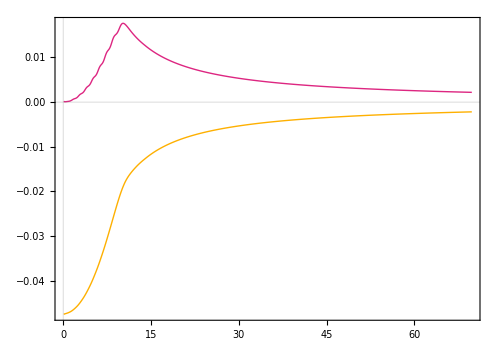

```mathematica
axionmetricperturbationsplot = ListPlot[{zetavals,deltavals},Joined->True,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\text{Metric Perturbations}\\ \\left[ \\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c1,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\zeta(r)",Magnification->2.0],MaTeX["\\color{darkgray}\\Delta(r)",Magnification->2.0]}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-metric-perturbations.pdf",axionmetricperturbationsplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/axion-metric-perturbations.pdf

### GetTidalDeformabilityWithAxions

```mathematica
tidalinfo = GetTidalDeformabilityWithAxions[mrmρ vals[[1]],massfnc,pressurefnc,densityfnc,axionmassfnc,axionpressurefnc,axiondensityfnc,deltafnc,zetafnc,myscales]
```

(6989.83 | 9555.6
y0fncsol$769670 | y1fncsol$769670)

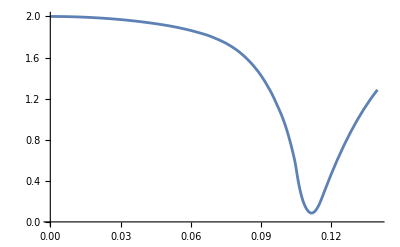

```mathematica
Plot[{tidalinfo[[2]][[1]][r](*,tidalinfo[[2]][[2]][r]*)},{r,10/10^5,mrmρ vals[[1]][[1]]}]
```

```mathematica
(* so it's an issue with y1 for sure. Need to go back and check what's going on there. *)
```

### Compare tidal deformabilities with and without axions

```mathematica
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;-1;;6,8;;9]];
centraldensities = EOSData[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited];
```

```mathematica
myscales={10^5,10^-10,1};
mafasubs = {10^-20,10^16};
MΛ table = {};
MΛa table = {};
Module[{mrmρ vals,ρc,massfnc,densityfnc,pressurefnc,thetathetaprime vals,thetafnc,thetafncprime,axiondensitypressuremass fncs,axiondensityfnc,axionpressurefnc,axionmassfnc,deltaandzeta fncs,zetafnc,deltafnc,tidal deformabilities},For[i=0,i<=64,i++,ρc=3.3+i*0.1;
mrmρ vals = Quiet[GetGenericMassRadius[ρc,pressureEOS m2,dpressureEOS m2,10^-12,myscales]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
thetathetaprime vals = Quiet[GetAxionField[mrmρ vals[[1]],mrmρ vals[[2]][[1]],mrmρ vals[[2]][[2]],mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
thetafnc[r_]:=Evaluate[thetathetaprime vals[[1]][[1]][r]];
thetafncprime[r_]:=Evaluate[thetathetaprime vals[[1]][[2]][r]];
axiondensitypressuremass fncs = Quiet[GetAxionEnergyPressureAndMass[thetafnc,thetafncprime,mrmρ vals[[1]],massfnc,densityfnc,mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
axiondensityfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[1]][r]];
axionpressurefnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[2]][r]];
axionmassfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[3]][r]];
deltaandzeta fncs=Quiet[GetDeltaAndZetaMetricPerturbations[mrmρ vals[[1]],massfnc,densityfnc,pressurefnc,axiondensityfnc,axionpressurefnc,axionmassfnc[mrmρ vals[[1]][[1]]],myscales]];
zetafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[1]][r]];
deltafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[2]][r]];
tidal deformabilities = Quiet[GetTidalDeformabilityWithAxions[mrmρ vals[[1]],massfnc,pressurefnc,densityfnc,axionmassfnc,axionpressurefnc,axiondensityfnc,deltafnc,zetafnc,myscales]];
AppendTo[MΛ table,{mrmρ vals[[1]][[2]]*myscales[[3]]*clight^2/GN/Msun,tidal deformabilities[[1]][[2]]}];
(*Print[axionmassfnc[mrmρ vals[[1]][[1]]]];*)
AppendTo[MΛa table,{(mrmρ vals[[1]][[2]] + axionmassfnc[mrmρ vals[[1]][[1]]])*myscales[[3]]*clight^2/GN/Msun,tidal deformabilities[[1]][[1]]}];If[Mod[i,16]==0,Print[i]]]]
```

0

16

32

48

64

```mathematica
MΛplot = ListLogPlot[{MΛa table,MΛ table(*,MΛDataLimited*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Lambda",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick,Dashed},{c5,Dashed},{c2,Dashed,Thick}},Joined->{True,True},ImageSize->{500,400},PlotRange->{{0.55,2.0},All},PlotLegends->Placed[{MaTeX["\\color{darkgray}\\text{axions}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{no axions}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Carlos}",Magnification->1.0]}, {0.8,0.8}],PlotLabel->MaTeX["\\color{darkgray}m_a = 10^{-11} \ \\text{eV} \\quad f_a = 10^{16} \ \\text{GeV}",Magnification->2.0]];
```

I need to figure out what the heck is going on with this difference from Carlos . Seems like the problem is back to being only with y0. Indeed, if I switch to the version of the y0 equation in Nico’s notebook, I get agreement with Carlos’s tidal deformability curves.

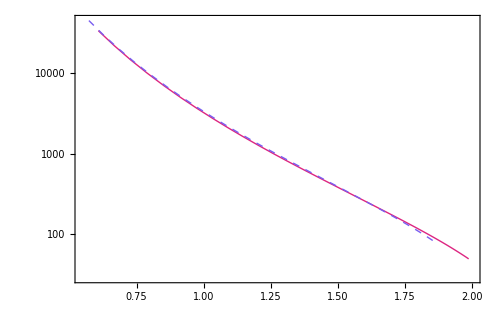

```mathematica
MΛplot
```

The tidal deformability at a fixed baryonic mass is always increased by the axion field, but when you include the mass sourced by the axion field, the curves intersect.

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaM.eos_nb0.05_G0.02_nb_0.27_G_0.06.pdf",MΛplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaM.eos_nb0.05_G0.02_nb_0.27_G_0.06.pdf

```mathematica
lambdaafnc = Interpolation[MΛa table];
lambdnoafnc = Interpolation[MΛ table];
```

```mathematica
lambdadiffvals = Table[{M,1 -lambdaafnc[M]/lambdnoafnc[M]},{M,0.61,1.86,0.01}];
```

```mathematica
Λdiffplot = ListPlot[{lambdadiffvals},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}1 - \\Lambda_a/\\Lambda_{a = 0}",Magnification->2.3]},PlotStyle->{{c2,Thick},{c2,Thick,Dashed},{c5,Dashed},{c2,Dashed,Thick}},Joined->{True,True},ImageSize->{500,200},PlotRange->{{0.55,2.0},All},AspectRatio->Full(*,PlotLegends->Placed[{MaTeX["\\color{darkgray}\\text{axions}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{no axions}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Carlos}",Magnification->1.0]}, {0.8,0.8}]*)(*,PlotLabel->MaTeX["\\color{darkgray}m_a = 10^{-11} \ \\text{eV} \\quad f_a = 10^{16} \ \\text{GeV}",Magnification->2.0]*)];
```

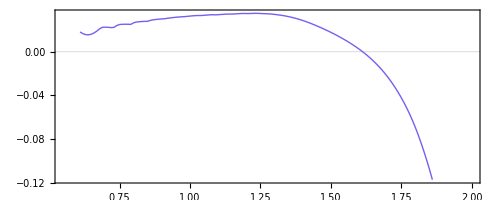

```mathematica
Λdiffplot
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaDiff.eos_nb0.05_G0.02_nb_0.27_G_0.06.pdf",Λdiffplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaDiff.eos_nb0.05_G0.02_nb_0.27_G_0.06.pdf

### Do same for multiple EOS

```mathematica
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
files=FileNames["*.csv",MRPATH];
```

```mathematica
Dimensions[files]
```

{3390}

```mathematica
myscales={10^5,10^-10,1};
mafasubs = {10^-20,10^16};
Npoints = 40;
MΛ table lots = {};
MΛa table lots = {};
shift = 3.1;
Module[{i,j,ρc},
For[i=1,i<=3,i++,
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[files[[i*139]],"CSV"];
EOSDataLimited=EOSData[[1;;-1;;8,8;;9]];
centraldensities = EOSData[[1;;-1,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)/myscales[[2]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; 
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
MΛ table small = {};
MΛa table small = {};
For[j=0,j<=Npoints,j++,ρc=10^(Log10[3.3-shift]+j*(Log10[10-shift]-Log10[3.3-shift])/Npoints)+shift;
mrmρ vals = Quiet[GetGenericMassRadius[ρc,pressureEOS m2,dpressureEOS m2,10^-12,myscales]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
thetathetaprime vals = Quiet[GetAxionField[mrmρ vals[[1]],mrmρ vals[[2]][[1]],mrmρ vals[[2]][[2]],mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
thetafnc[r_]:=Evaluate[thetathetaprime vals[[1]][[1]][r]];
thetafncprime[r_]:=Evaluate[thetathetaprime vals[[1]][[2]][r]];
axiondensitypressuremass fncs = Quiet[GetAxionEnergyPressureAndMass[thetafnc,thetafncprime,mrmρ vals[[1]],massfnc,densityfnc,mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
axiondensityfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[1]][r]];
axionpressurefnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[2]][r]];
axionmassfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[3]][r]];
deltaandzeta fncs=Quiet[GetDeltaAndZetaMetricPerturbations[mrmρ vals[[1]],massfnc,densityfnc,pressurefnc,axiondensityfnc,axionpressurefnc,axionmassfnc[mrmρ vals[[1]][[1]]],myscales]];
zetafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[1]][r]];
deltafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[2]][r]];
tidal deformabilities = Quiet[GetTidalDeformabilityWithAxions[mrmρ vals[[1]],massfnc,pressurefnc,densityfnc,axionmassfnc,axionpressurefnc,axiondensityfnc,deltafnc,zetafnc,myscales]];
AppendTo[MΛ table small,{mrmρ vals[[1]][[2]]*myscales[[3]]*clight^2/GN/Msun,tidal deformabilities[[1]][[2]]}];
(*Print[axionmassfnc[mrmρ vals[[1]][[1]]]];*)
AppendTo[MΛa table small,{(mrmρ vals[[1]][[2]] + axionmassfnc[mrmρ vals[[1]][[1]]])*myscales[[3]]*clight^2/GN/Msun,tidal deformabilities[[1]][[1]]}];
If[Mod[j,16]==0,Print[j]]];
AppendTo[MΛ table lots,MΛ table small];
AppendTo[MΛa table lots,MΛa table small];
Print[StringJoin["Done with EOS ",ToString[i]]]]]
```

0

16

32

Done with EOS 1

0

16

32

Done with EOS 2

0

16

32

Done with EOS 3

```mathematica
lambdafncs = {};
lambdaafncs = {};
Module[{fnc,fnca},For[k=1,k<=3,k++,
fnc=Interpolation[MΛ table lots[[k]]];
fnca=Interpolation[MΛa table lots[[k]]];
AppendTo[lambdafncs,fnc];
AppendTo[lambdaafncs,fnca]]]
```

```mathematica
lambdadiffvals lots = {};
For[k=1,k<=3,k++,
AppendTo[lambdadiffvals lots,Table[{M,1 -lambdaafncs[[k]][M]/lambdafncs[[k]][M]},{M,Max[{Min[MΛ table lots[[k]][[All,1]]],Min[MΛa table lots[[k]][[All,1]]]}],Min[{Max[MΛ table lots[[k]][[All,1]]],Max[MΛa table lots[[k]][[All,1]]]}],0.001}]]];
```

```mathematica
MΛplot = ListLogPlot[{MΛa table lots[[1]],MΛ table lots[[1]],MΛa table lots[[2]],MΛ table lots[[2]],MΛa table lots[[3]],MΛ table lots[[3]](*,MΛa table lots[[4]],MΛ table lots[[4]],MΛa table lots[[5]],MΛ table lots[[5]]*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Lambda \\left[\\text{a.u.}\\right]",Magnification->2.3]},PlotStyle->{{c1,Thick},{c1,Thick,Dashed},{c5,Thick},{c5,Thick,Dashed},{c3,Thick},{c3,Thick,Dashed},{c4,Thick},{c4,Thick,Dashed},{c5,Thick},{c5,Thick,Dashed}},Joined->{True,True,True,True,True,True},ImageSize->{700,500},PlotRange->{{0.45,2.05},{30,9*10^4}},PlotLegends->Placed[{MaTeX["\\color{darkgray}a \\neq 0",Magnification->1.0],MaTeX["\\color{darkgray}a = 0",Magnification->1.0]}, {0.8,0.8}],PlotLabel->MaTeX["\\color{darkgray}m_a = 10^{-11} \ \\text{eV} \\quad f_a = 10^{16} \ \\text{GeV}",Magnification->2.0]];
```

```mathematica
Λdiffplot = ListPlot[{lambdadiffvals lots[[1]],MovingAverage[lambdadiffvals lots[[2]],300],MovingAverage[lambdadiffvals lots[[3]],1](*,lambdadiffvals lots[[4]],lambdadiffvals lots[[5]]*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Delta \\Lambda/\\Lambda_{a = 0}",Magnification->2.3]},PlotStyle->{{c1,Thick},{c5,Thick},{c3,Thick},{c4,Thick},{c5,Thick}},Joined->{True,True},ImageSize->{700,200},PlotRange->{{0.45,2.05},All},AspectRatio->Full];
```

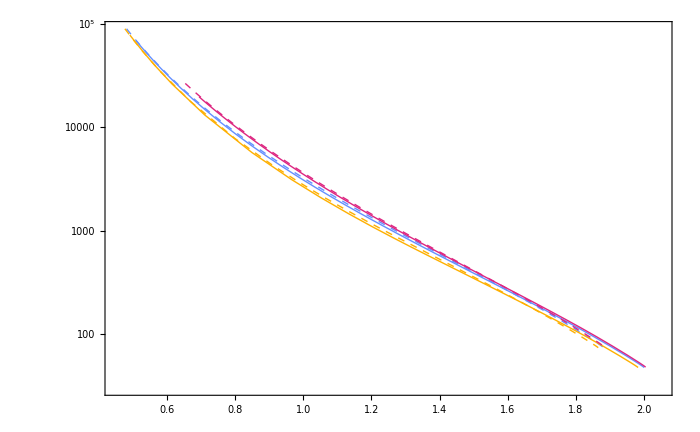

```mathematica
MΛplot
```

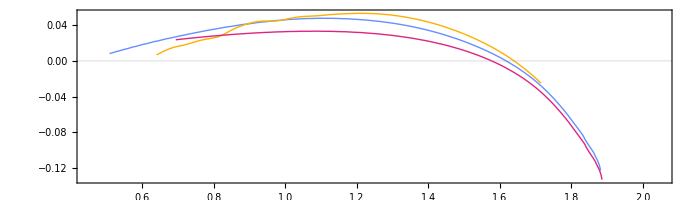

```mathematica
Λdiffplot
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaM-5-EOS.pdf",MΛplot,"PDF"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaDiff-5-EOS.pdf",Λdiffplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaM-5-EOS.pdf

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaDiff-5-EOS.pdf

### Compare MR curve for multiple EOS

```mathematica
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
files=FileNames["*.csv",MRPATH];
```

```mathematica
myscales={10^5,10^-10,1};
mafasubs = {10^-20,10^16};
Npoints = 40;
MR table lots = {};
MRa table lots = {};
shift = 3.1;
rhostart=3.3;
rhoend=10.0;
Module[{i,j,ρc},
For[i=1,i<=3,i++,
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[files[[i*139]],"CSV"];
EOSDataLimited=EOSData[[1;;-1;;8,8;;9]];
centraldensities = EOSData[[1;;-1,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)/myscales[[2]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; 
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
MR table small = {};
MRa table small = {};
For[j=0,j<=Npoints,j++,ρc=10^(Log10[rhostart-shift]+j*(Log10[rhoend-shift]-Log10[rhostart-shift])/Npoints)+shift;
mrmρ vals = Quiet[GetGenericMassRadius[ρc,pressureEOS m2,dpressureEOS m2,10^-12,myscales]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
thetathetaprime vals = Quiet[GetAxionField[mrmρ vals[[1]],mrmρ vals[[2]][[1]],mrmρ vals[[2]][[2]],mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
thetafnc[r_]:=Evaluate[thetathetaprime vals[[1]][[1]][r]];
thetafncprime[r_]:=Evaluate[thetathetaprime vals[[1]][[2]][r]];
axiondensitypressuremass fncs = Quiet[GetAxionEnergyPressureAndMass[thetafnc,thetafncprime,mrmρ vals[[1]],massfnc,densityfnc,mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
axiondensityfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[1]][r]];
axionpressurefnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[2]][r]];
axionmassfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[3]][r]];
AppendTo[MR table small,{mrmρ vals[[1]][[1]]*myscales[[1]],mrmρ vals[[1]][[2]]*myscales[[3]]*clight^2/GN/Msun}];
(*Print[axionmassfnc[mrmρ vals[[1]][[1]]]];*)
AppendTo[MRa table small,{mrmρ vals[[1]][[1]]*myscales[[1]],(mrmρ vals[[1]][[2]]+axionmassfnc[mrmρ vals[[1]][[1]]])*myscales[[3]]*clight^2/GN/Msun}];
If[Mod[j,20]==0,Print[j]]];
AppendTo[MR table lots,MR table small];
AppendTo[MRa table lots,MRa table small];
Print[StringJoin["Done with EOS ",ToString[i]]]]]
```

0

20

40

Done with EOS 1

0

20

40

Done with EOS 2

0

20

40

Done with EOS 3

```mathematica
MRfncs = {};
MRafncs = {};
Module[{fnc,fnca},For[k=1,k<=3,k++,
fnc=Interpolation[MR table lots[[k]]];
fnca=Interpolation[MRa table lots[[k]]];
AppendTo[MRfncs,fnc];
AppendTo[MRafncs,fnca]]]
```

```mathematica
1 - MR table lots[[2]][[50]][[2]]/MRa table lots[[2]][[50]][[2]]
```

0.0589617

```mathematica
MRdiffvals lots = {};
For[k=1,k<=3,k++,
AppendTo[MRdiffvals lots,Table[{MR table lots[[k]][[m]][[1]],1 - MRa table lots[[k]][[m]][[2]]/MR table lots[[k]][[m]][[2]]},{m,1,Dimensions[MR table lots[[k]]][[1]]}]]];
```

```mathematica
MRplot = ListLogPlot[{MRa table lots[[1]],MR table lots[[1]],MRa table lots[[2]],MR table lots[[2]],MRa table lots[[3]],MR table lots[[3]](*,MΛa table lots[[4]],MΛ table lots[[4]],MΛa table lots[[5]],MΛ table lots[[5]]*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R_s \\ \\left[ \\text{m} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c1,Thick},{c1,Thick,Dashed},{c5,Thick},{c5,Thick,Dashed},{c3,Thick},{c3,Thick,Dashed},{c4,Thick},{c4,Thick,Dashed},{c5,Thick},{c5,Thick,Dashed}},Joined->{True,True,True,True,True,True},ImageSize->{700,500},PlotRange->{{1.26*10^4,1.56*10^4},{0.4,2.1}},PlotLegends->Placed[{MaTeX["\\color{darkgray}a \\neq 0",Magnification->1.0],MaTeX["\\color{darkgray}a = 0",Magnification->1.0]}, {0.8,0.8}],PlotLabel->MaTeX["\\color{darkgray}m_a = 10^{-11} \ \\text{eV} \\quad f_a = 10^{16} \ \\text{GeV}",Magnification->2.0]];
```

```mathematica
Mdiffplot = ListPlot[{MRdiffvals lots[[1]],MovingAverage[MRdiffvals lots[[2]],1],MovingAverage[MRdiffvals lots[[3]],1](*,lambdadiffvals lots[[4]],lambdadiffvals lots[[5]]*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R_s \\ \\left[ \\text{m} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Delta M/M_{a = 0}",Magnification->2.3]},PlotStyle->{{c1,Thick},{c5,Thick},{c3,Thick},{c4,Thick},{c5,Thick}},Joined->{True,True,True},ImageSize->{700,200},PlotRange->{{1.26*10^4,1.56*10^4},{-0.0629,-0.0611}},AspectRatio->Full];
```

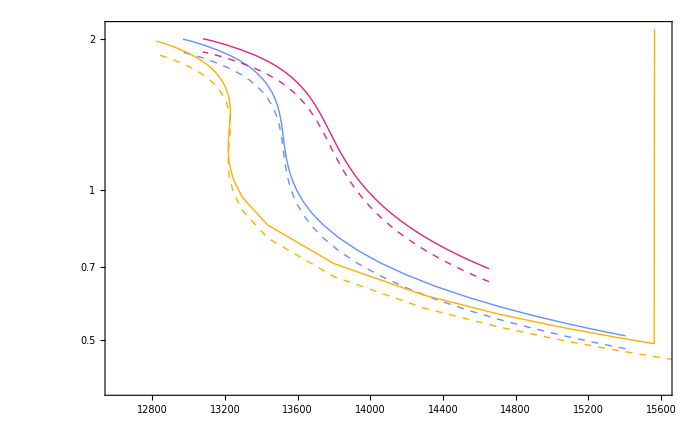

```mathematica
MRplot
```

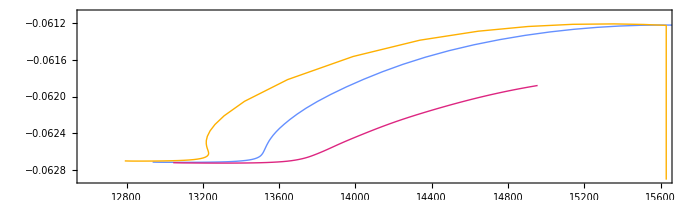

```mathematica
Mdiffplot
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/MR-3-EOS-ma10.-11.fa-10.16.pdf",MRplot,"PDF"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/MRDiff-3-EOS-ma10.-11.fa-10.16.pdf",Mdiffplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/MR-3-EOS-ma10.-11.fa-10.16.pdf

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/MRDiff-3-EOS-ma10.-11.fa-10.16.pdf

```mathematica
(* Independent of EOS, the axion adds a pretty constant mass to the NS. *)
```

### Compare Λc curves for multiple EOS

```mathematica
ΛC table lots = {};
ΛCa table lots = {};
Module[{k,m},For[k=1,k<=3,k++,
AppendTo[ΛC table lots,Table[{(MR table lots[[k]][[m]][[2]])*((clight^2/GN)/Msun)^(-1)/MR table lots[[k]][[m]][[1]],MΛ table lots[[k]][[m]][[2]]},{m,1,Dimensions[MΛ table lots[[k]]][[1]],1}]]]];
Module[{k,m},For[k=1,k<=3,k++,
AppendTo[ΛCa table lots,Table[{MRa table lots[[k]][[m]][[2]]*((clight^2/GN)/Msun)^(-1)/MRa table lots[[k]][[m]][[1]],MΛa table lots[[k]][[m]][[2]]},{m,1,Dimensions[MΛa table lots[[k]]][[1]],1}]]]];
```

```mathematica
lambdaCfncs = {};
lambdaCafncs = {};
Module[{fnc,fnca},For[k=1,k<=3,k++,
fnc=Interpolation[ΛC table lots[[k]]];
fnca=Interpolation[ΛCa table lots[[k]]];
AppendTo[lambdaCfncs,fnc];
AppendTo[lambdaCafncs,fnca]]]
```

```mathematica
lambdaCdiffvals lots = {};
For[k=1,k<=3,k++,
AppendTo[lambdaCdiffvals lots,Table[{M,1 -lambdaCafncs[[k]][M]/lambdaCfncs[[k]][M]},{M,Max[{Min[ΛC table lots[[k]][[All,1]]],Min[ΛCa table lots[[k]][[All,1]]]}],Min[{Max[ΛCa table lots[[k]][[All,1]]],Max[ΛC table lots[[k]][[All,1]]]}],0.001}]]];

lambdaCnoadiffvals lots = {};
For[k=2,k<=3,k++,
AppendTo[lambdaCnoadiffvals lots,Table[{M,1 -lambdaCfncs[[k]][M]/lambdaCfncs[[1]][M]},{M,Max[{Min[ΛC table lots[[1]][[All,1]]],Min[ΛC table lots[[k]][[All,1]]]}],Min[{Max[ΛC table lots[[1]][[All,1]]],Max[ΛC table lots[[k]][[All,1]]]}],0.001}]]];
```

```mathematica
CΛplot = ListLogPlot[{ΛCa table lots[[1]],ΛC table lots[[1]],ΛCa table lots[[2]],ΛC table lots[[2]],ΛCa table lots[[3]],ΛC table lots[[3]](*,MΛa table lots[[4]],MΛ table lots[[4]],MΛa table lots[[5]],MΛ table lots[[5]]*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}C \\ \\left[\\text{a.u.} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Lambda \\left[\\text{a.u.}\\right]",Magnification->2.3]},PlotStyle->{{c1,Thick},{c1,Thick,Dashed},{c5,Thick},{c5,Thick,Dashed},{c3,Thick},{c3,Thick,Dashed},{c4,Thick},{c4,Thick,Dashed},{c5,Thick},{c5,Thick,Dashed}},Joined->{True,True,True,True,True,True},ImageSize->{700,500},PlotRange->{{0.04,0.24},{30,9*10^4}},PlotLegends->Placed[{MaTeX["\\color{darkgray}a \\neq 0",Magnification->1.0],MaTeX["\\color{darkgray}a = 0",Magnification->1.0]}, {0.8,0.8}],PlotLabel->MaTeX["\\color{darkgray}m_a = 10^{-11} \ \\text{eV} \\quad f_a = 10^{16} \ \\text{GeV}",Magnification->2.0]];
```

```mathematica
ΛCdiffplot = ListPlot[{lambdaCdiffvals lots[[1]],MovingAverage[lambdaCdiffvals lots[[2]],1],MovingAverage[lambdaCdiffvals lots[[3]],1],lambdaCnoadiffvals lots[[1]],lambdaCnoadiffvals lots[[2]](*,lambdadiffvals lots[[4]],lambdadiffvals lots[[5]]*)},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}C \\ \\left[\\text{a.u.} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Delta \\Lambda/\\Lambda_{a = 0}",Magnification->2.3]},PlotStyle->{{c1,Thick},{c5,Thick},{c3,Thick},{c5,Thick,Dashed},{c3,Thick,Dashed}},Joined->{True,True},ImageSize->{700,200},PlotRange->{{0.04,0.24},All},AspectRatio->Full,PlotLegends->Placed[{MaTeX["\\color{darkgray}a \\neq 0",Magnification->1.0],None,None,MaTeX["\\color{darkgray}a = 0",Magnification->1.0]}, {0.8,0.8}]];
```

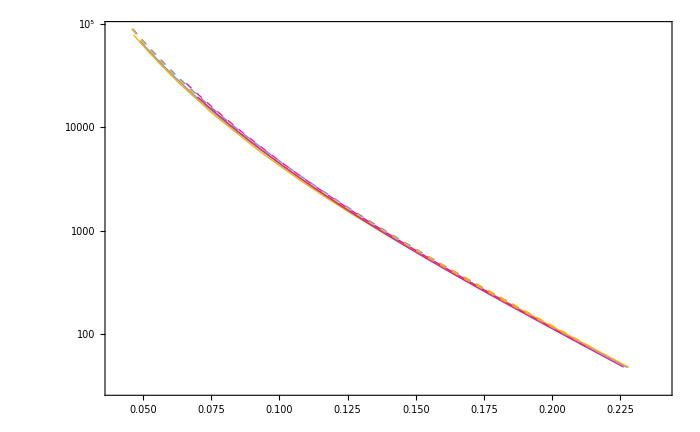

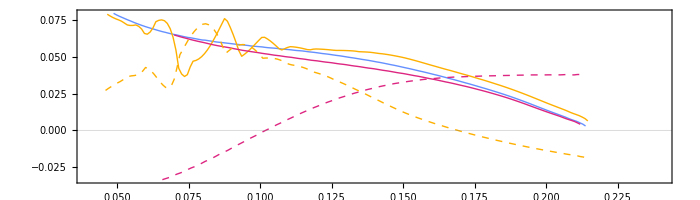

```mathematica
CΛplot
ΛCdiffplot
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LC-3-EOS-ma10.-11.fa-10.16.pdf",CΛplot,"PDF"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LCDiff-3-EOS-ma10.-11.fa-10.16.pdf",ΛCdiffplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LC-3-EOS-ma10.-11.fa-10.16.pdf

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LCDiff-3-EOS-ma10.-11.fa-10.16.pdf

### Do same for multiple axion Parameters

```mathematica
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
files=FileNames["*.csv",MRPATH];
```

```mathematica
Dimensions[files]
```

{3390}

```mathematica
myscales={10^5,10^-10,1};
mafasubs = {10^-20,10^16};
MΛ table lots = {};
MΛa table lots = {};

Module[{i,j},
For[i=1,i<=5,i++,
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[files[[i*139]],"CSV"];
EOSDataLimited=EOSData[[1;;-1;;8,8;;9]];
centraldensities = EOSData[[1;;-1,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; 
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
MΛ table small = {};
MΛa table small = {};
For[j=0,j<=64,j++,ρc=3.3+j*0.1;
mrmρ vals = Quiet[GetGenericMassRadius[ρc,pressureEOS m2,dpressureEOS m2,10^-12,myscales]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
thetathetaprime vals = Quiet[GetAxionField[mrmρ vals[[1]],mrmρ vals[[2]][[1]],mrmρ vals[[2]][[2]],mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
thetafnc[r_]:=Evaluate[thetathetaprime vals[[1]][[1]][r]];
thetafncprime[r_]:=Evaluate[thetathetaprime vals[[1]][[2]][r]];
axiondensitypressuremass fncs = Quiet[GetAxionEnergyPressureAndMass[thetafnc,thetafncprime,mrmρ vals[[1]],massfnc,densityfnc,mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
axiondensityfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[1]][r]];
axionpressurefnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[2]][r]];
axionmassfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[3]][r]];
deltaandzeta fncs=Quiet[GetDeltaAndZetaMetricPerturbations[mrmρ vals[[1]],massfnc,densityfnc,pressurefnc,axiondensityfnc,axionpressurefnc,axionmassfnc[mrmρ vals[[1]][[1]]],myscales]];
zetafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[1]][r]];
deltafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[2]][r]];
tidal deformabilities = Quiet[GetTidalDeformabilityWithAxions[mrmρ vals[[1]],massfnc,pressurefnc,densityfnc,axionmassfnc,axionpressurefnc,axiondensityfnc,deltafnc,zetafnc,myscales]];
AppendTo[MΛ table small,{mrmρ vals[[1]][[2]]*myscales[[3]]*clight^2/GN/Msun,tidal deformabilities[[1]][[2]]}];
(*Print[axionmassfnc[mrmρ vals[[1]][[1]]]];*)
AppendTo[MΛa table small,{(mrmρ vals[[1]][[2]] + axionmassfnc[mrmρ vals[[1]][[1]]])*myscales[[3]]*clight^2/GN/Msun,tidal deformabilities[[1]][[1]]}];
If[Mod[j,16]==0,Print[j]]];
AppendTo[MΛ table lots,MΛ table small];
AppendTo[MΛa table lots,MΛa table small];
Print[StringJoin["Done with EOS ",ToString[i]]]]]
```

0

16

32

48

64

Done with EOS 1

0

16

32

48

64

Done with EOS 2

0

16

32

48

64

Done with EOS 3

0

16

32

48

64

Done with EOS 4

0

16

32

48

64

Done with EOS 5

```mathematica
MΛ table lots[[5]]
```

{{0.733889,14150.9},{0.842297,7755.64},{0.884854,6239.52},{0.934183,4894.17},{0.980923,3918.54},{1.0259,3183.03},{1.06901,2620.51},{1.11037,2182.88},{1.15009,1837.},{1.18799,1561.95},{1.22424,1340.03},{1.25893,1158.95},{1.29212,1009.83},{1.32384,886.004},{1.35415,782.382},{1.38309,695.047},{1.41072,620.95},{1.43708,557.698},{1.46222,503.393},{1.48624,456.391},{1.50939,415.186},{1.53168,378.944},{1.5531,346.978},{1.57368,318.714},{1.59341,293.657},{1.61232,271.388},{1.63041,251.552},{1.6477,233.84},{1.6642,217.99},{1.67994,203.776},{1.69493,191.003},{1.70919,179.502},{1.72274,169.127},{1.73559,159.752},{1.74825,150.94},{1.76132,142.267},{1.77453,133.918},{1.78766,126.024},{1.8005,118.678},{1.81289,111.934},{1.82466,105.818},{1.83568,100.338},{1.84584,95.4892},{1.85505,91.2567},{1.86321,87.6213},{1.87026,84.5624},{1.87615,82.0604},{1.88084,80.0987},{1.8843,78.664},{1.88652,77.749},{1.8879,77.1767},{1.88906,76.6953},{1.89004,76.2896},{1.89085,75.948},{1.89154,75.6599},{1.89211,75.4158},{1.8926,75.2072},{1.89302,75.0261},{1.89338,74.8658},{1.89371,74.7198},{1.89402,74.5823},{1.89432,74.4485},{1.89461,74.3137},{1.89491,74.1736},{1.89522,74.0248}}

```mathematica
lambdafncs = {};
lambdaafncs = {};
Module[{fnc,fnca},For[k=1,k<=5,k++,
fnc=Interpolation[MΛ table lots[[k]]];
fnca=Interpolation[MΛa table lots[[k]]];
AppendTo[lambdafncs,fnc];
AppendTo[lambdaafncs,fnca]]]
```

```mathematica
lambdadiffvals lots = {};
For[k=1,k<=5,k++,
AppendTo[lambdadiffvals lots,Table[{M,1 -lambdaafncs[[k]][M]/lambdafncs[[k]][M]},{M,Max[{Min[MΛ table lots[[k]][[All,1]]],Min[MΛa table lots[[k]][[All,1]]]}],Min[{Max[MΛ table lots[[k]][[All,1]]],Max[MΛa table lots[[k]][[All,1]]]}],0.01}]]];
```

```mathematica
MΛplot = ListLogPlot[{MΛa table lots[[1]],MΛ table lots[[1]],MΛa table lots[[2]],MΛ table lots[[2]],MΛa table lots[[3]],MΛ table lots[[3]],MΛa table lots[[4]],MΛ table lots[[4]],MΛa table lots[[5]],MΛ table lots[[5]]},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Lambda \\left[\\text{a.u.}\\right]",Magnification->2.3]},PlotStyle->{{c1,Thick},{c1,Thick,Dashed},{c2,Thick},{c2,Thick,Dashed},{c3,Thick},{c3,Thick,Dashed},{c4,Thick},{c4,Thick,Dashed},{c5,Thick},{c5,Thick,Dashed}},Joined->{True,True},ImageSize->{700,500},PlotRange->{{0.55,2.0},All},PlotLegends->Placed[{MaTeX["\\color{darkgray}a \\neq 0",Magnification->1.0],MaTeX["\\color{darkgray}a = 0",Magnification->1.0]}, {0.8,0.8}],PlotLabel->MaTeX["\\color{darkgray}m_a = 10^{-11} \ \\text{eV} \\quad f_a = 10^{16} \ \\text{GeV}",Magnification->2.0]];
```

```mathematica
Λdiffplot = ListPlot[{lambdadiffvals lots[[1]],lambdadiffvals lots[[2]],lambdadiffvals lots[[3]],lambdadiffvals lots[[4]],lambdadiffvals lots[[5]]},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}1 - \\Lambda_a/\\Lambda_{a = 0}",Magnification->2.3]},PlotStyle->{{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick}},Joined->{True,True},ImageSize->{700,200},PlotRange->{{0.55,2.0},All},AspectRatio->Full];
```

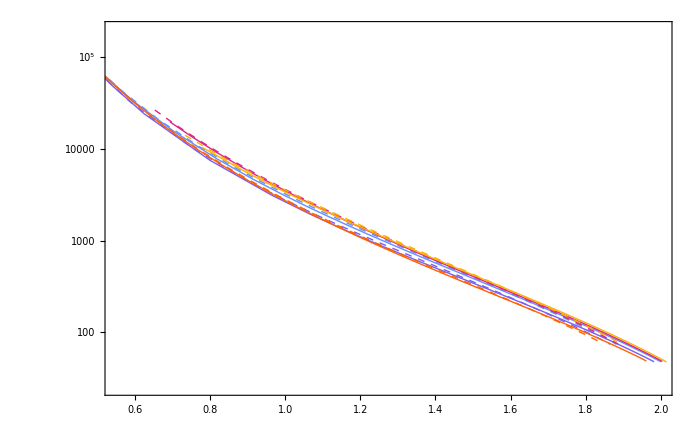

```mathematica
MΛplot
```

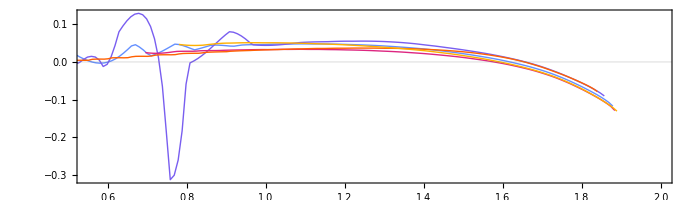

```mathematica
Λdiffplot
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaM-5-EOS.pdf",MΛplot,"PDF"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaDiff-5-EOS.pdf",Λdiffplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaM-5-EOS.pdf

/Users/wentmich/Documents/uiuc/research/axions-in-NS/notes/figures/LambdaDiff-5-EOS.pdf

### Check with NIco’s Group’s notebook

#### Check Lambda formula

```mathematica
myΛ=(8*Rs^2*rscale^2*(2*Mns*mscale - Rs*rscale)*(4*Mns*mscale*(-3*Mns*mscale*Rs^6*rscale^6*(-2 + y0atsfc)^2 + 16*Mns^7*mscale^7*(-1 + y0atsfc^2) + 8*Mns^6*mscale^6*Rs*rscale*(5 - 4*y0atsfc + y0atsfc^2) + 3*Mns^2*mscale^2*Rs^5*rscale^5*(28 - 32*y0atsfc + 9*y0atsfc^2) - 4*Mns^5*mscale^5*Rs^2*rscale^2*(34 - 60*y0atsfc + 27*y0atsfc^2) + 2*Mns^4*mscale^4*Rs^3*rscale^3*(130 - 204*y0atsfc + 77*y0atsfc^2) - Mns^3*mscale^3*Rs^4*rscale^4*(220 - 292*y0atsfc + 94*y0atsfc^2)) + 6*Mns*mscale*Rs^2*rscale^2*(2*Mns*mscale - Rs*rscale)^3*(Rs*rscale*(-2 + y0atsfc) - 2*Mns*mscale*(-1 + y0atsfc))^2*Log[1 - (2*Mns*mscale)/(Rs*rscale)]))/(15*Mns*mscale*(2*Mns*mscale*(2*Mns^2*mscale^2*Rs^2*rscale^2*(13 - 11*y0atsfc) - 3*Rs^4*rscale^4*(-2 + y0atsfc) + 4*Mns^4*mscale^4*(1 + y0atsfc) + 2*Mns^3*mscale^3*Rs*rscale*(-2 + 3*y0atsfc) + 3*Mns*mscale*Rs^3*rscale^3*(-8 + 5*y0atsfc)) + 3*Rs^2*rscale^2*(-2*Mns*mscale + Rs*rscale)^2*(-(Rs*rscale*(-2 + y0atsfc)) + 2*Mns*mscale*(-1 + y0atsfc))*Log[1 - (2*Mns*mscale)/(Rs*rscale)])^2);
myΛ = myΛ /.{mscale->1,rscale->1,ρscale->1,Mns->Rs*C,y0atsfc->Y}//FullSimplify
```

(16 (1-2 C)^2 (2 C (Y-1)-Y+2))/(30 C (C (2 C (C (2 C (Y+1)+3 Y-2)-11 Y+13)+3 (5 Y-8))-3 Y+6)+45 (1-2 C)^2 (2 C (Y-1)-Y+2) log(1-2 C))

```mathematica
nicoΛ=8/5(1-2C)^2 C^5 *(2C *(Y-1)-Y+2)*(2C*(  4(Y+1)C^4 + (6 Y-4)C^3+(26-22Y)C^2+3(5Y-8)C-3Y+6 ) -3(1-2C)^2(2C*(Y-1)-Y+2) Log[1/(1-2C)])^-1;
nicoΛ=nicoΛ*(2/3)/C^5//FullSimplify
```

(16 (1-2 C)^2 (2 C (Y-1)-Y+2))/(30 C (C (2 C (C (2 C (Y+1)+3 Y-2)-11 Y+13)+3 (5 Y-8))-3 Y+6)-45 (1-2 C)^2 (2 C (Y-1)-Y+2) log(1/(1-2 C)))

These are the same.

#### Check formula for y0

```mathematica
myyeq=y0'[r]/rscale==(-4*mscale^3*M[r]^3*(-1 + y0[r]^2) + 4*Pi*r^5*rscale^5*(p[r]*(6 + 64*Pi^2*r^4*rscale^4*p[r]^2 - y0[r] - y0[r]^2 - 4*Pi*r^2*rscale^2*p[r]*(9 + y0[r]) + 4*Pi*r^2*rscale^2*ρscale*(-5 + y0[r])*ρ[r]) + r*ρscale*Derivative[1][ρ][r]) + mscale*r^2*rscale^2*M[r]*(6 + 32*Pi^2*r^4*rscale^4*p[r]^2*(15 + y0[r]) - 20*Pi*r^2*rscale^2*ρscale*ρ[r] - y0[r]*(1 + y0[r] - 4*Pi*r^2*rscale^2*ρscale*ρ[r]) + 4*Pi*r^2*rscale^2*p[r]*(-21 + y0[r] + 4*y0[r]^2 - 8*Pi*r^2*rscale^2*ρscale*(-5 + y0[r])*ρ[r]) - 16*Pi*r^3*rscale^2*ρscale*Derivative[1][ρ][r]) + 2*mscale^2*r*rscale*M[r]^2*(-6 + 4*Pi*r^2*rscale^2*p[r]*(15 + y0[r] - 2*y0[r]^2) + 20*Pi*r^2*rscale^2*ρscale*ρ[r] + y0[r]*(1 + 2*y0[r] - 4*Pi*r^2*rscale^2*ρscale*ρ[r]) + 8*Pi*r^3*rscale^2*ρscale*Derivative[1][ρ][r]))/(r*rscale*(r*rscale - 2*mscale*M[r])^2*(mscale*M[r] + 4*Pi*r^3*rscale^3*p[r]));
myyeq=myyeq/.{mscale->1,rscale->1,ρscale->1,Mns->Rs*C,y0[r]->y[r],y0'[r]->y'[r]}//FullSimplify
```

(r^2 M(r) (-32 π^2 r^4 (p(r))^2 (y(r)+15)+4 π r^2 p(r) (8 π r^2 ρ(r) (y(r)-5)-4 (y(r))^2-y(r)+21)+4 π r^2 (4 r ρ'(r)+5 ρ(r))-4 π r^2 ρ(r) y(r)+(y(r))^2+y(r)-6)-2 r (M(r))^2 (4 π r^2 p(r) (-2 (y(r))^2+y(r)+15)+8 π r^3 ρ'(r)+20 π r^2 ρ(r)+y(r) (-4 π r^2 ρ(r)+2 y(r)+1)-6)+4 (M(r))^3 ((y(r))^2-1)+4 π r^5 (p(r) (-64 π^2 r^4 (p(r))^2+4 π r^2 p(r) (y(r)+9)-4 π r^2 ρ(r) (y(r)-5)+(y(r))^2+y(r)-6)-r ρ'(r)))/(r (r-2 M(r))^2 (M(r)+4 π r^3 p(r)))+y'(r)==0

```mathematica
f= 1-2*M[r]/r;
A=(2/f)*(1 - (1/r)*3*M[r]-2*Pi*r^2*(ρ[r]+3*p[r]));
B=(1/f)*(2*3-4*Pi*r^2*(ρ[r]+p[r])*(3+ρ'[r]/p'[r]));
nicoyeq = r*y'[r]+y[r]*(y[r]-1)+A*y[r]-B==0;
nicoyeq=nicoyeq//.TOV replacements//FullSimplify;
```

```mathematica
nicoyeq
```

r y'(r)+(y(r)-1) y(r)==(6 M(r) y(r)+12 π r^3 p(r) (y(r)-1)+4 π r^3 ρ(r) (y(r)-3)-2 r y(r)+6 r)/(r-2 M(r))+(4 π r^4 ρ'(r))/(M(r)+4 π r^3 p(r))

```mathematica
Solve[nicoyeq,y'[r]]//FullSimplify
Solve[myyeq,y'[r]]//FullSimplify
```

{{y'(r)→((6 M(r) y(r)+12 π r^3 p(r) (y(r)-1)+4 π r^3 ρ(r) (y(r)-3)-2 r y(r)+6 r)/(r-2 M(r))+(4 π r^4 ρ'(r))/(M(r)+4 π r^3 p(r))-(y(r)-1) y(r))/r}}

{{y'(r)→(2 r (M(r))^2 (4 π r^2 p(r) (-2 (y(r))^2+y(r)+15)+8 π r^3 ρ'(r)+20 π r^2 ρ(r)+y(r) (-4 π r^2 ρ(r)+2 y(r)+1)-6)+r^2 M(r) (32 π^2 r^4 (p(r))^2 (y(r)+15)+4 π r^2 p(r) (-8 π r^2 ρ(r) (y(r)-5)+4 (y(r))^2+y(r)-21)-16 π r^3 ρ'(r)-20 π r^2 ρ(r)-y(r) (-4 π r^2 ρ(r)+y(r)+1)+6)-4 (M(r))^3 ((y(r))^2-1)+4 π r^5 (p(r) (64 π^2 r^4 (p(r))^2-4 π r^2 p(r) (y(r)+9)+4 π r^2 ρ(r) (y(r)-5)-(y(r))^2-y(r)+6)+r ρ'(r)))/(r (r-2 M(r))^2 (M(r)+4 π r^3 p(r)))}}

```mathematica
nicoyeq/.%[[1]]
```

(2 r (M(r))^2 (4 π r^2 p(r) (-2 (y(r))^2+y(r)+15)+8 π r^3 ρ'(r)+20 π r^2 ρ(r)+y(r) (-4 π r^2 ρ(r)+2 y(r)+1)-6)+r^2 M(r) (32 π^2 r^4 (p(r))^2 (y(r)+15)+4 π r^2 p(r) (-8 π r^2 ρ(r) (y(r)-5)+4 (y(r))^2+y(r)-21)-16 π r^3 ρ'(r)-20 π r^2 ρ(r)-y(r) (-4 π r^2 ρ(r)+y(r)+1)+6)-4 (M(r))^3 ((y(r))^2-1)+4 π r^5 (p(r) (64 π^2 r^4 (p(r))^2-4 π r^2 p(r) (y(r)+9)+4 π r^2 ρ(r) (y(r)-5)-(y(r))^2-y(r)+6)+r ρ'(r)))/((r-2 M(r))^2 (M(r)+4 π r^3 p(r)))+(y(r)-1) y(r)==(6 M(r) y(r)+12 π r^3 p(r) (y(r)-1)+4 π r^3 ρ(r) (y(r)-3)-2 r y(r)+6 r)/(r-2 M(r))+(4 π r^4 ρ'(r))/(M(r)+4 π r^3 p(r))

```mathematica
FullSimplify[%]
```

(M(r) (4 π r^3 p(r) (2 y(r)+5)+4 π r^3 ρ(r)-r y(r))+(M(r))^2 (2 y(r)+1)+2 π r^4 (p(r) (8 π r^2 p(r)-2 y(r)-3)-ρ(r)))/(r-2 M(r))==0

#### rederive y0 equation

```mathematica
hequation = D[h[r],r,r]+(2/r + (2*M[r]/r^2+4*Pi*r*(p[r]-ρ[r]))*Exp[λ[r]])*D[h[r],r] - (6*Exp[λ[r]]/r^2-4*Pi*(5*ρ[r]+9*p[r]+(ρ[r]+p[r])*ρ'[r]/p'[r])*Exp[λ[r]] + ν'[r]^2)*h[r]==0;
hequation=hequation//.ν replacements//.TOV replacements//.{h'[r]->h[r]*y[r]/r,h''[r]->(h[r]*(-y[r] + y[r]^2 + r*Derivative[1][y][r]))/r^2};
```

ReplaceRepeated::reps: {ν replacements} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

```mathematica
hequation=hequation//Simplify
```

h(r) ((4 π r (-(r (r-2 M(r)) ρ'(r))/(M(r)+4 π r^3 p(r))+9 p(r)+5 ρ(r)))/(r-2 M(r))+(2 y(r) (-M(r)+2 π r^3 p(r)-2 π r^3 ρ(r)+r))/(r^2 (r-2 M(r)))-(4 (M(r)+4 π r^3 p(r))^2)/(r^2 (r-2 M(r))^2)-6/(r^2-2 r M(r))+(r y'(r)+(y(r))^2-y(r))/r^2)==0

```mathematica
yprime = y'[r]/.Solve[hequation,y'[r]][[1]]//FullSimplify;
rederivedyeq = y'[r]==yprime;
```

```mathematica
nicoyeq/.{y'[r]->yprime}//Simplify
```

(M(r) (4 π r^3 p(r) (2 y(r)+5)+4 π r^3 ρ(r)-r y(r))+(M(r))^2 (2 y(r)+1)+2 π r^4 (8 π r^2 (p(r))^2-p(r) (2 y(r)+3)-ρ(r)))/(r-2 M(r))==0

```mathematica
nicoyeq
```

r y'(r)+(y(r)-1) y(r)==(6 M(r) y(r)+12 π r^3 p(r) (y(r)-1)+4 π r^3 ρ(r) (y(r)-3)-2 r y(r)+6 r)/(r-2 M(r))+(4 π r^4 ρ'(r))/(M(r)+4 π r^3 p(r))

```mathematica
Solve[nicoyeq,y'[r]]
```

{{y'(r)→((6 M(r) y(r)+12 π r^3 p(r) (y(r)-1)+4 π r^3 ρ(r) (y(r)-3)-2 r y(r)+6 r)/(r-2 M(r))+(4 π r^4 ρ'(r))/(M(r)+4 π r^3 p(r))-(y(r)-1) y(r))/r}}

```mathematica
y'[r]/.Solve[nicoyeq,y'[r]][[1]]//Simplify
```

((6 M(r) y(r)+12 π r^3 p(r) (y(r)-1)+4 π r^3 ρ(r) (y(r)-3)-2 r y(r)+6 r)/(r-2 M(r))+(4 π r^4 ρ'(r))/(M(r)+4 π r^3 p(r))-(y(r)-1) y(r))/r

```mathematica
%/.{a_[r]->a[rt]}/.{r->r*rscale,Rs->Rs*rscale}/.{rt->r}/.{M[r]->M[r]*mscale,ρ[r]->ρ[r]*ρscale,ρ'[r]->ρ'[r]*ρscale/rscale}/.{y[r]->y0[r]}//InputForm
```

(-((-1 + y0[r])*y0[r]) + (6*r*rscale + 12*Pi*r^3*rscale^3*p[r]*(-1 + y0[r]) - 2*r*rscale*y0[r] + 6*mscale*M[r]*y0[r] + 4*Pi*r^3*rscale^3*ρscale*(-3 + y0[r])*ρ[r])/(r*rscale - 2*mscale*M[r]) + (4*Pi*r^4*rscale^3*ρscale*Derivative[1][ρ][r])/(mscale*M[r] + 4*Pi*r^3*rscale^3*p[r]))/(r*rscale)

```mathematica
TOV replacements
```

{λ'(r)→-((2 M(r))/r^2-(2 M'(r))/r)/(1-(2 M(r))/r),λ''(r)→-ⅇ^(λ(r)) ((2 M'(r))/r^2-(4 M(r))/r^3-8 π r ρ'(r)-8 π ρ(r))-ⅇ^(λ(r)) ((2 M(r))/r^2-8 π r ρ(r)) λ'(r),ⅇ^(λ(r))→1/(1-(2 M(r))/r),ⅇ^(-λ(r))→1-(2 M(r))/r,λ(r)→log(1/(1-(2 M(r))/r)),p'(r)→-((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r))),p''(r)→1/(r^2 (r-2 M(r))^2)(-r (r-2 M(r)) (p(r)+ρ(r)) (M'(r)+4 π r^3 p'(r)+12 π r^2 p(r))+r (M(r)+4 π r^3 p(r)) (1-2 M'(r)) (p(r)+ρ(r))-r (r-2 M(r)) (M(r)+4 π r^3 p(r)) (p'(r)+ρ'(r))+(r-2 M(r)) (M(r)+4 π r^3 p(r)) (p(r)+ρ(r))),ν'(r)→-(2 p'(r))/(p(r)+ρ(r)),M'(r)→4 π r^2 ρ(r)}

### What goes into command line

```mathematica
myscales={10^5,10^-10,1};
mafasubs = {ToExpression[$CommandLine[[-2]]],ToExpression[$CommandLine[[-1]]]};
Npoints = ToExpression[$CommandLine[[-3]]];
downsamplefactor = ToExpression[$CommandLine[[-4]]];
output table lots = {};
shift = 3.1;
Module[{i,j,ρc},
EOSData=Import[files[[i*139]],"CSV"];
EOSDataLimited=EOSData[[1;;-1;;downsamplefactor,8;;9]];
centraldensities = EOSData[[1;;-1,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)/myscales[[2]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; 
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
For[j=0,j<=Npoints,j++,ρc=10^(Log10[3.3-shift]+j*(Log10[10-shift]-Log10[3.3-shift])/Npoints)+shift;
mrmρ vals = Quiet[GetGenericMassRadius[ρc,pressureEOS m2,dpressureEOS m2,10^-12,myscales]];
MNS = mrmρ vals[[1]][[2]]*myscales[[3]];
RNS = mrmρ vals[[1]][[1]]*myscales[[1]];
rhocNS = ρc*myscales[[2]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
thetathetaprime vals = Quiet[GetAxionField[mrmρ vals[[1]],mrmρ vals[[2]][[1]],mrmρ vals[[2]][[2]],mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
thetafnc[r_]:=Evaluate[thetathetaprime vals[[1]][[1]][r]];
thetafncprime[r_]:=Evaluate[thetathetaprime vals[[1]][[2]][r]];
axiondensitypressuremass fncs = Quiet[GetAxionEnergyPressureAndMass[thetafnc,thetafncprime,mrmρ vals[[1]],massfnc,densityfnc,mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
axiondensityfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[1]][r]];
axionpressurefnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[2]][r]];
axionmassfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[3]][r]];
Maxion = axionmassfnc[mrmρ vals[[1]][[1]]]*myscales[[3]];
deltaandzeta fncs=Quiet[GetDeltaAndZetaMetricPerturbations[mrmρ vals[[1]],massfnc,densityfnc,pressurefnc,axiondensityfnc,axionpressurefnc,axionmassfnc[mrmρ vals[[1]][[1]]],myscales]];
zetafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[1]][r]];
deltafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[2]][r]];
tidal deformabilities = Quiet[GetTidalDeformabilityWithAxions[mrmρ vals[[1]],massfnc,pressurefnc,densityfnc,axionmassfnc,axionpressurefnc,axiondensityfnc,deltafnc,zetafnc,myscales]];
LambdaNS = tidal deformabilities[[1]][[2]];
LambdaAxion = tidal deformabilities[[1]][[1]];
AppendTo[output table lots,{ρc, RNS, MNS, Maxion,LambdaNS, LambdaAxion}]]]
```

```mathematica
var = 10^-20//N
```

1.×10^-20

```mathematica
StringDelete[ToString[var],WhitespaceCharacter]//InputForm
```

"-201.10"

```mathematica
ToExpression[%]
```

-201.1

### What is in the command line

```mathematica
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
files=FileNames["*.csv",MRPATH];

myscales={10^5,10^-10,1};
mafasubs={ToExpression[$CommandLine[[-2]]],ToExpression[$CommandLine[[-1]]]};
Npoints=ToExpression[$CommandLine[[-3]]];
downsamplefactor=ToExpression[$CommandLine[[-4]]];
Clear[output table lots];
output table lots={};
shift=3.1;
Module[{j,EOSData,EOSDataLimited,centraldensities,pressureEOS,dpressureEOS,pressureEOS m2,dpressureEOS m2},EOSData=Import[files[[139]],"CSV"];
EOSDataLimited=EOSData[[1;;-1;;downsamplefactor,8;;9]];
centraldensities=EOSData[[1;;-1,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)/myscales[[2]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited];
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
Print["did everything pre do loop"];
output table lots=ParallelTable[Module[{ρc,mrmρ vals,MNS,RNS,rhocNS,massfnc,densityfnc,pressurefnc,thetathetaprime vals,thetafnc,thetafncprime,axiondensitypressuremass fncs,axiondensityfnc,axionpressurefnc,axionmassfnc,Maxion,deltaandzeta fncs,zetafnc,deltafnc,tidal deformabilities,LambdaNS,LambdaAxion},ρc=10^(Log10[3.3-shift]+j*(Log10[10-shift]-Log10[3.3-shift])/Npoints)+shift;
mrmρ vals=Quiet[GetGenericMassRadius[ρc,pressureEOS m2,dpressureEOS m2,10^-12,myscales]];
Print[mrmρ vals[[1]]];
MNS=mrmρ vals[[1]][[2]]*myscales[[3]];
RNS=mrmρ vals[[1]][[1]]*myscales[[1]];
rhocNS=ρc*myscales[[2]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
thetathetaprime vals=Quiet[GetAxionField[mrmρ vals[[1]],mrmρ vals[[2]][[1]],mrmρ vals[[2]][[2]],mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
thetafnc[r_]:=Evaluate[thetathetaprime vals[[1]][[1]][r]];
thetafncprime[r_]:=Evaluate[thetathetaprime vals[[1]][[2]][r]];
axiondensitypressuremass fncs=Quiet[GetAxionEnergyPressureAndMass[thetafnc,thetafncprime,mrmρ vals[[1]],massfnc,densityfnc,mafasubs[[1]]*GeV2m,mafasubs[[2]]*GeV2m,myscales]];
axiondensityfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[1]][r]];
axionpressurefnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[2]][r]];
axionmassfnc[r_]:=Evaluate[axiondensitypressuremass fncs[[1]][[3]][r]];Maxion=axionmassfnc[mrmρ vals[[1]][[1]]]*myscales[[3]];
Print[Maxion];deltaandzeta fncs=Quiet[GetDeltaAndZetaMetricPerturbations[mrmρ vals[[1]],massfnc,densityfnc,pressurefnc,axiondensityfnc,axionpressurefnc,axionmassfnc[mrmρ vals[[1]][[1]]],myscales]];zetafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[1]][r]];deltafnc[r_]:=Evaluate[deltaandzeta fncs[[1]][[2]][r]];tidal deformabilities=Quiet[GetTidalDeformabilityWithAxions[mrmρ vals[[1]],massfnc,pressurefnc,densityfnc,axionmassfnc,axionpressurefnc,axiondensityfnc,deltafnc,zetafnc,myscales]];
Print[tidal deformabilities[[1]]];
LambdaNS=tidal deformabilities[[1]][[2]];
LambdaAxion=tidal deformabilities[[1]][[1]];
Print[{ρc,RNS,MNS,Maxion,LambdaNS,LambdaAxion}];
Print[StringJoin["Working on step ",ToString[j]," of ",ToString[Npoints]]];{rhocNS,RNS,MNS,Maxion,LambdaNS,LambdaAxion}],{j,0,Npoints}]]
```

did everything pre do loop

{0.153705,710.802}

{0.135215,1731.16}

{0.133791,2399.96}

{0.129908,2782.68}

43.5249

108.321

150.486

174.51

{160.366,239.938}

{5.94704,13379.1,2399.96,150.486,239.938,160.366}

Working on step 3 of 4

{47.7384,74.1807}

{10.,12990.8,2782.68,174.51,74.1807,47.7384}

Working on step 4 of 4

{1059.46,1507.97}

{4.27473,13521.5,1731.16,108.321,1507.97,1059.46}

Working on step 2 of 4

{67737.4,89755.4}

{3.3,15370.5,710.802,43.5249,89755.4,67737.4}

Working on step 0 of 4

{0.138215,1112.62}

69.0102

{8675.72,11800.1}

{3.58471,13821.5,1112.62,69.0102,11800.1,8675.72}

Working on step 1 of 4

{{3.3×10^-10,15370.5,710.802,43.5249,89755.4,67737.4},{3.58471×10^-10,13821.5,1112.62,69.0102,11800.1,8675.72},{4.27473×10^-10,13521.5,1731.16,108.321,1507.97,1059.46},{5.94704×10^-10,13379.1,2399.96,150.486,239.938,160.366},{1.×10^-9,12990.8,2782.68,174.51,74.1807,47.7384}}

```mathematica
output table lots
```

{}

```mathematica
ToString[ToString[10^-16,FortranForm]]
```

1.e-16

### Expansion in density

```mathematica
mueff[rt]=mu*(1 - (σN*rho*hbarGeo^3/(mN*mpi^2*fpi^2*GeV2m^4))*((mu+md)/mu));
mdeff[rt]=md*(1 - (σN*rho*hbarGeo^3/(mN*mpi^2*fpi^2*GeV2m^4))*((md+mu)/md));
vascaled[r_]:= Evaluate[-mpi^2*fpi^2*GeV2m^4*epsilon*Sqrt[1 - ((4*mueff[rt]*mdeff[rt])/(mueff[rt]+mdeff[rt])^2)*Sin[θT[rt]]^2]/hbarGeo^3];
```

```mathematica
vascaled[r]//Simplify
```

-5.30159×10^-11 epsilon √((1.78197×10^-19-8.44267×10^-10 rho+1. rho^2+(-1.47685×10^-19+8.44267×10^-10 rho-1. rho^2) Sin[θT[rt]]^2)/((4.22134×10^-10-1. rho)^2))

```mathematica
Series[%,{rho,0,1}]
```

-5.30159×10^-11 epsilon-0.12559 (epsilon Sin[θT[rt]]^2) rho+O[rho]^2

```mathematica
((mpi^2*fpi^2*GeV2m^4)/(σN*GeV2m*hbarGeo^3))
```

6.79203×10^44

```mathematica
densityfnc[0.01*mrmρ vals[[1]][[1]]]*myscales[[2]] / (mN*GeV2m)/((mpi^2*fpi^2*GeV2m^4)/(σN*GeV2m*hbarGeo^3))
```

0.438218

```mathematica
ϵ=(*0.4*)10^-1;
fasub=10^16;
mafasubs = {Sqrt[fpi^2*mpi^2*ϵ/(2*fasub^2)],fasub}*GeV2m;
myscales={10^5,10^-10,1};
```

```mathematica
dθpdr rscaled =-(1-(2*1437.2*myscales[[3]])/(rt*myscales[[1]]))*Derivative[1][θTp][rt] + (2*(1437.2*myscales[[3]]-rt*myscales[[1]])/(rt^2*myscales[[1]]))*θTp[rt]==(mafasubs[[1]]^2*myscales[[1]]^2/hbarGeo^2)* ((1/2))*Sin[θT[rt]]*(Cos[θT[rt]]/Abs[Cos[θT[rt]]]);
dθdr rscaled = D[θT[rt],rt]==θTp[rt];
mythetaTfncsols=NDSolve[{dθpdr rscaled,dθdr rscaled,θT[0.1372363396093167]==Pi/2,θTp[0.1372363396093167]==0},{θT, θTp},{rt,0.1372363396093167,1.372363396093167},PrecisionGoal->4,AccuracyGoal->4][[1]];
```

```mathematica
mythetaTfncsols
```

{θT→InterpolatingFunction[…],θTp→InterpolatingFunction[…]}

```mathematica
thetafnc=Evaluate[θT/.mythetaTfncsols]
```

InterpolatingFunction[…]

```mathematica
Plot[thetafnc[r],{r,0.1372363396093167,1.372363396093167},PlotRange->All]
```

-Graphics-

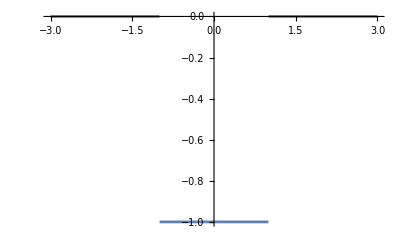

```mathematica
Plot[-1 + Abs[HeavisideTheta[r-1] - HeavisideTheta[-r -1]],{r, -3, 3}]
```

```mathematica
Length[{{1,2}, {1,2}, {1,2}}]
```

3

```mathematica
testerfunction = GetAxionFieldFromPython["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/time-evolved-axion-field.csv"][[1]]
```

imported file

parsed file

InterpolatingFunction[…]

```mathematica
testerfunction[599000, 1000]
```

1.56869

```mathematica
axionfield[t_, r_]:=Evaluate[testerfunction[t, r]]
```

```mathematica
axionfield[599000, 1000]
```

1.56869

```mathematica
mrmρ vals[[1]][[1]]*myscales[[1]]
```

16536.

```mathematica
daxiondt[t_, r_]:=Evaluate[D[axionfield[t, r], t]]
daxiondr[t_, r_]:=Evaluate[D[axionfield[t, r], r]]
```

```mathematica
Manipulate[Plot[daxiondr[t, r], {r, mrmρ vals[[1]][[1]]*myscales[[1]], 60000},PlotRange->{All, {-10^-4, 10^-4}}], {t, 591000, 599000}]
```

Part::partd: Part specification mrmρ vals⟦1⟧ is longer than depth of object.

Plot::plln: Limiting value 100000 mrmρ vals in {r,100000 mrmρ vals,60000} is not a machine-sized real number.

```mathematica
f = 10^4;
m = 10^-7;
Ncycles  = 2 * 10^6  * (f / 10^9)^(-5/3) * (m / 10^-9)^(-5/3);
period = 1 / f;
secondsatf = period * Ncycles//N
Clear[f, m, period, Ncycles, secondsatf]
```

2.×10^7

### Plot Friction Profile

### Export all mass radius functions for

```mathematica
FILEBASE="debora-EOS-1";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".dat"]];
EOSDataLimited=EOSData[[1;;-1;;1,{3,2}]];
EOSDataLimited = Delete[EOSDataLimited,50];
EOSDataLimited=EOSDataLimited[[1;;-1;;1]];
pressureEOS=ResourceFunction["CubicSplineInterpolation"][EOSDataLimited];
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited];
```

```mathematica
base = 2;
shift = 3.1;
myscales={10^5,10^-10,1};
Npoints=100;
```

```mathematica
massradiusvals = {};
frictionvalsset = {};
```

```mathematica
myeps = 0.0005;
```

```mathematica
Module[{mrmρ vals,ρc,i,massfnc,densityfnc,nufnc,densityin,pressurefnc,densityvals,pressurevals,massvals,nuvals,frictionvals,rc},
For[i=0, i<Npoints,i++,
ρc = Log[base,3.3-shift] + i*(Log[base,11-shift]-Log[base,3.3-shift])/100;
mrmρ vals = Quiet[GetGenericMassRadius[base^ρc+shift,pressureEOS m2,dpressureEOS m2,RHOFRAC,myscales]];
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
nufnc[r_]:=Evaluate[mrmρ vals[[2]][[3]][r]];
densityin[r_]:=Evaluate[mrmρ vals[[2]][[4]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
rc=rt/.NSolve[-σN*densityin[rt]*myscales[[2]]*hbarGeo^3/(mN*mpi^2*fpi^2*GeV2m^4)+myeps==0,rt][[1]];
(*densityvals = Quiet[Table[{r*myscales[[1]]/10^3, densityfnc[r]*myscales[[2]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
pressurevals = Quiet[Table[{r*myscales[[1]]/10^3, pressurefnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
massvals = Quiet[Table[{r*myscales[[1]]/10^3, massfnc[r]*myscales[[3]]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
nuvals = Quiet[Table[{r*myscales[[1]]/10^3, nufnc[r]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];*)
frictionvals = Quiet[Table[{r*myscales[[1]]/10^3, GetFrictionProfile[r, nufnc,densityfnc,pressurefnc, myscales, myeps,rc]},{r,RSTART, 10*mrmρ vals[[1]][[1]], mrmρ vals[[1]][[1]]/1000}]];
(*Print[rc];*)
(*Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/density-vals-rhoc-",ToString[ρc],".csv"],densityvals,"CSV"];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/pressure-vals-rhoc-",ToString[ρc],".csv"],pressurevals,"CSV"];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/mass-vals-rhoc-",ToString[ρc],".csv"],massvals,"CSV"];
Export[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/debora-EOS-1-functions/nu-vals-rhoc-",ToString[ρc],".csv"],nuvals,"CSV"];*)
AppendTo[massradiusvals,{mrmρ vals[[1]]}];AppendTo[frictionvalsset,frictionvals]]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

```mathematica
frictionvalsset[[1]][[1]]
```

{1.×10^-6,0.0301612}

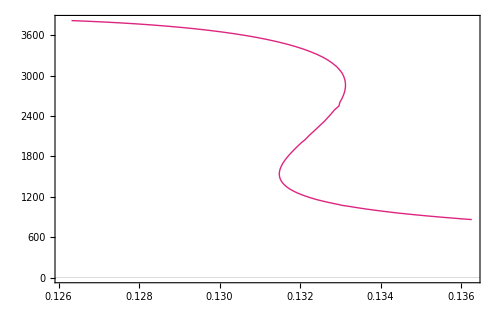

```mathematica
MRplot = ListPlot[Flatten[massradiusvals,1],PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick,Dashed},{c5,Thick,Dashed},{c2,Dashed,Thick}},Joined->{True},ImageSize->{500,400},PlotRange->(*{{12.0,17.0},{0.0,2.0}}*)All,PlotLegends->Placed[{MaTeX["\\color{darkgray}\\text{Full EOS}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Downsample Factor 4}",Magnification->1.0],MaTeX["\\color{darkgray}\\text{Downsample Factor 8}",Magnification->1.0]},{Right,Top}],PlotLabel->MaTeX["\\color{darkgray}\\rho_{\\text{frac}} = 10^{-10}",Magnification->2.3]];
GraphicsRow[{MRplot},ImageSize->{500,400}]
```

```mathematica
maxr = massradiusvals[[1]][[1]][[1]]*10^2;
minr = massradiusvals[[95]][[1]][[1]]*10^2;
```

```mathematica
minr
```

12.8313

```mathematica
ToString[PaddedForm[1.0,{3,1}]]
```

1.0

```mathematica
myticks =Table[{i, MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->1.5]},{i,12.8,13.6,0.1}];
```

```mathematica
mybarlegend = BarLegend[{Blend[{{minr,c1},{minr + (maxr-minr)/4,c2},{minr+ (maxr-minr)*2/4,c3},{minr+ (maxr-minr)*3/4,c4},{maxr,c5}},#]&,{minr,maxr}},Ticks->myticks,LegendMarkerSize->700]
```

```mathematica
Mag=1.4;
```

```mathematica
mycolors = (*Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]][[1]] - minr) / (maxr-minr)][[3]]],{i, 1, Npoints}];*)IBMcolorsNew[Npoints];
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,Npoints}];
```

```mathematica
Dimensions[plotstylelist]
```

{100,2}

```mathematica
xticks=Table[{j,If[Mod[j,2]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{3,1}]]],Magnification->Mag],None],If[Mod[j,2]==0,0.013,0.005]},{j,0.0,maxr,0.5}];
xticksNV=Table[{j,None,If[Mod[j,2]==0,0.013,0.005]},{j,0.0,maxr,0.5}];
```

```mathematica
yticks=Table[{i*10^-2,If[Mod[i,1]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->Mag],None],If[Mod[i,1]==0,0.013,0.005]},{i,0.0,9.5,0.5}];
yticksNV=Table[{i*10^-2,None,If[Mod[i,1]==0,0.013,0.005]},{i,0.0,9.5,0.5}];
```

```mathematica
allfrictionfncsimg = ListPlot[frictionvalsset[[1;;95]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\text{Friction Term}\\times 10^2 \\ [\\text{m}^{-1}]",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,13.3},All}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/all-friction-profiles-debora-EOS-1.pdf",allfrictionfncsimg,"PDF"];
```

### Estimate photosphere Inner radius (not possible with sun density resolution??)

```mathematica
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;-1;;4,8;;9]];
centraldensities = EOSData[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited];
```

```mathematica
myscales={10^5,10^-10,1};
mrmρ vals = Quiet[GetGenericMassRadius[4.5,pressureEOS m2,dpressureEOS m2,RHOFRAC,myscales]];
```

```mathematica
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
nufnc[r_]:=Evaluate[mrmρ vals[[2]][[3]][r]];
densityin[r_]:=Evaluate[mrmρ vals[[2]][[4]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
```

```mathematica
densitydata = Import["/Users/wentmich/Documents/uiuc/research/axions-in-NS/mathematica/sun-density-data.csv","CSV"];
```

```mathematica
RSm = 696.34*10^6;
```

```mathematica
densitydata[[All,1]] = densitydata[[All,1]]*RSm;
densitydata[[All,2]] = densitydata[[All,2]]*(10^-3 / (10^-6))* GN / clight^2;
```

```mathematica
densitydata//InputForm
```

{{1.0965984251966667*^6, 1.1130532039856415*^-22}, {1.1788433070866298*^7, 1.1559135985390812*^-22}, {2.6592511811023608*^7, 9.988316653644438*^-23}, {3.975169291338576*^7, 8.629710745531986*^-23}, {5.1265976377952814*^7, 8.024854815693826*^-23}, {6.4425157480314806*^7, 6.44081938851937*^-23}, {8.4986377952756*^7, 5.366962027315534*^-23}, {9.979045669291326*^7, 4.308195985305504*^-23}, {1.1541698425196832*^8, 3.458548552666721*^-23}, {1.3104351181102373*^8, 2.880661989231471*^-23}, {1.491373858267714*^8, 2.2293857224128938*^-23}, {1.7134350393700773*^8, 1.603376851183977*^-23}, {1.902598267716536*^8, 1.240966387910726*^-23}, {2.0917614960629913*^8, 8.288661961499302*^-24}, {2.256251259842521*^8, 6.654483450481969*^-24}, {2.4289655118110245*^8, 5.149626922545675*^-24}, {2.6099042519685036*^8, 3.84121556524792*^-24}, {2.823740944881889*^8, 2.6624875010190044*^-24}, {3.045802125984252*^8, 1.9148641631561987*^-24}, {3.3418837007874024*^8, 1.2338768885373006*^-24}, {3.629740787401575*^8, 7.950129296525291*^-25}, {3.9833937795275605*^8, 4.761332628912448*^-25}, {4.3617202362204736*^8, 3.070275460309901*^-25}, {4.674250787401576*^8, 1.9786737480948225*^-25}, {5.011454803149607*^8, 1.3233219932780658*^-25}, {5.29931188976378*^8, 9.522870810464684*^-26}, {5.595393464566928*^8, 6.605439982667049*^-26}, {5.801005669291338*^8, 4.928209396771322*^-26}, {5.957270944881891*^8, 3.813182380926491*^-26}, {6.146434173228346*^8, 2.741649844131947*^-26}, {6.310923937007873*^8, 1.8308042350553004*^-26}, {6.417842283464566*^8, 1.364744513968602*^-26}, {6.532985118110237*^8, 9.109453055042916*^-27}, {6.648127952755904*^8, 5.648501480969276*^-27}, {6.771495275590549*^8, 2.423291661447612*^-27}, {6.837291181102363*^8, 1.1185558059912956*^-27}, {6.88663811023622*^8, 6.68107939556478*^-28}, {6.91131157480315*^8, 3.318494643542703*^-28}, {6.927760551181103*^8, 1.588561793418633*^-28}, {6.944209527559054*^8, 7.889820181461885*^-29}, {6.935985039370079*^8, 4.53978838269232*^-29}, {6.944209527559054*^8, 2.710610430842065*^-29}, {6.952434015748031*^8, 1.3966854255294634*^-29}, {6.952434015748031*^8, 7.466182497772623*^-30}, {6.952434015748031*^8, 3.991155064062702*^-30}, {6.960658503937008*^8, 1.7747210371000307*^-30}, {6.960658503937008*^8, 6.326013251897166*^-31}, {6.968882992125983*^8, 2.427513162445442*^-31}, {6.97710748031496*^8, 1.3969893313794533*^-31}}

```mathematica
densitydata = {{1.0965984251966667*^6, 1.1130532039856415*^-22}, {1.1788433070866298*^7, 1.1559135985390812*^-22}, {2.6592511811023608*^7, 9.988316653644438*^-23}, {3.975169291338576*^7, 8.629710745531986*^-23}, {5.1265976377952814*^7, 8.024854815693826*^-23}, {6.4425157480314806*^7, 6.44081938851937*^-23}, {8.4986377952756*^7, 5.366962027315534*^-23}, {9.979045669291326*^7, 4.308195985305504*^-23}, {1.1541698425196832*^8, 3.458548552666721*^-23}, {1.3104351181102373*^8, 2.880661989231471*^-23}, {1.491373858267714*^8, 2.2293857224128938*^-23}, {1.7134350393700773*^8, 1.603376851183977*^-23}, {1.902598267716536*^8, 1.240966387910726*^-23}, {2.0917614960629913*^8, 8.288661961499302*^-24}, {2.256251259842521*^8, 6.654483450481969*^-24}, {2.4289655118110245*^8, 5.149626922545675*^-24}, {2.6099042519685036*^8, 3.84121556524792*^-24}, {2.823740944881889*^8, 2.6624875010190044*^-24}, {3.045802125984252*^8, 1.9148641631561987*^-24}, {3.3418837007874024*^8, 1.2338768885373006*^-24}, {3.629740787401575*^8, 7.950129296525291*^-25}, {3.9833937795275605*^8, 4.761332628912448*^-25}, {4.3617202362204736*^8, 3.070275460309901*^-25}, {4.674250787401576*^8, 1.9786737480948225*^-25}, {5.011454803149607*^8, 1.3233219932780658*^-25}, {5.29931188976378*^8, 9.522870810464684*^-26}, {5.595393464566928*^8, 6.605439982667049*^-26}, {5.801005669291338*^8, 4.928209396771322*^-26}, {5.957270944881891*^8, 3.813182380926491*^-26}, {6.146434173228346*^8, 2.741649844131947*^-26}, {6.310923937007873*^8, 1.8308042350553004*^-26}, {6.417842283464566*^8, 1.364744513968602*^-26}, {6.532985118110237*^8, 9.109453055042916*^-27}, {6.648127952755904*^8, 5.648501480969276*^-27}, {6.771495275590549*^8, 2.423291661447612*^-27}, {6.837291181102363*^8, 1.1185558059912956*^-27}, {6.88663811023622*^8, 6.68107939556478*^-28}, {6.91131157480315*^8, 3.318494643542703*^-28}, {6.927760551181103*^8, 1.588561793418633*^-28}, {6.944209527559054*^8, 7.889820181461885*^-29}, {6.935985039370079*^8, 4.53978838269232*^-29}, {6.952434015748031*^8, 7.466182497772623*^-30}, {6.960658503937008*^8, 1.7747210371000307*^-30},  {6.968882992125983*^8, 2.427513162445442*^-31}, {6.97710748031496*^8, 1.3969893313794533*^-31}};
```

```mathematica
densityfnc = Interpolation[densitydata]
```

InterpolatingFunction[…]

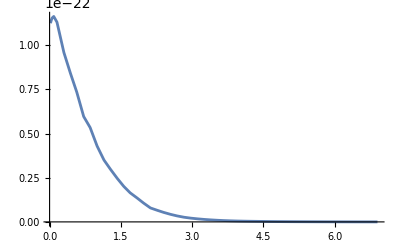

```mathematica
Plot[densityfnc[r], {r, 2*10^6, 6.9*10^8},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0000277047} lies outside the range of data in the interpolating function. Extrapolation will be used.

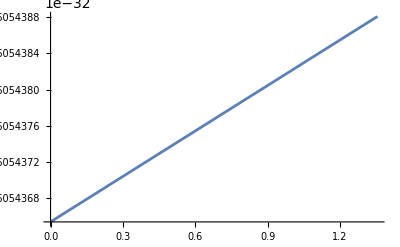

```mathematica
Plot[densityfnc[r]*myscales[[2]],{r,RSTART, 10*mrmρ vals[[1]][[1]]}]
```

```mathematica
mrmρ vals[[1]][[1]]
```

0.135569

```mathematica
photosphere integral[r0_, density_, scales_, RNS_]:=Exp[NIntegrate[Log[1 - (8*Pi*(1/137)^2 * (density[r])^(2/3) * hbarGeo^2) / (3 * me^2 * GeV2m^2 * (mN * GeV2m)^(2/3))], {r, r0, 2*RNS}, Method->"GlobalAdaptive",PrecisionGoal->4,AccuracyGoal->4]]
```

```mathematica
6.97710748031496*^8
```

```mathematica
photosphere integral[6.9771074802*10^8, densityfnc, myscales, 6.97710748031496*10^8]
```

1.74097×10^12+1.81956×10^12 ⅈ

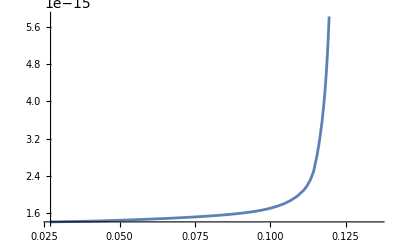

```mathematica
Plot[((densityfnc[r]*myscales[[2]])/(mN * GeV2m))^(-1/3),{r, mrmρ vals[[1]][[1]]/5, mrmρ vals[[1]][[1]]}]
```

```mathematica
Plot[(3.89*10^(-32)*8*(1/137)^2*Pi/(3*me^2)) * ((densityfnc[r]*myscales[[2]])/(mN * GeV2m))^(2/3), {r, mrmρ vals[[1]][[1]]/5, mrmρ vals[[1]][[1]]*2}]
```

-Graphics-

```mathematica
GeV2m
```

1.32298×10^-54

```mathematica
(8*(1/137)^2 * hbarGeo^2) / (3 * me^2 * GeV2m^2 * (mN * GeV2m)^(2/3))
```

1.8326×10^7

### Plot all axion fields

```mathematica
massradiusvals = Import["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/MR-vals.csv","CSV"];
```

```mathematica
maxr = massradiusvals[[1]][[1]]/10^3;
minr = massradiusvals[[95]][[1]]/10^3;
```

```mathematica
maxr
```

13.4091

```mathematica
myticks =Table[{i, MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->1.5]},{i,12.8,13.6,0.1}];
```

```mathematica
mybarlegend = BarLegend[{Blend[{{minr,c1},{minr + (maxr-minr)/4,c2},{minr+ (maxr-minr)*2/4,c3},{minr+ (maxr-minr)*3/4,c4},{maxr,c5}},#]&,{12.79,maxr}},Ticks->myticks,LegendMarkerSize->700];
```

```mathematica
axiondatasets = {};
```

```mathematica
For[i=0, i<95,i++,
AppendTo[axiondatasets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/cluster-outputs/axion-and-derivative-rhoindex-",ToString[i],"-last-time-epsilon-10-faexponent-10.csv"],"CSV"]]
]
```

```mathematica
axionfieldsets = {};
For[i=1, i<=95,i++,
AppendTo[axionfieldsets,axiondatasets[[i]][[1;;-1,2;;3]]]
]
```

```mathematica
axionderivsets = {};
For[i=1, i<=95,i++,
AppendTo[axionderivsets,axiondatasets[[i]][[1;;-1,{2,4}]]]
]
```

```mathematica
For[i=1, i<=95, i++,
axionfieldsets[[i]][[1;;-1,1]] = axionfieldsets[[i]][[1;;-1,1]]/10^3]
```

```mathematica
For[i=1, i<=95, i++,
axionderivsets[[i]][[1;;-1,1]] = axionderivsets[[i]][[1;;-1,1]]/10^3]
```

```mathematica
Mag=1.4;
```

```mathematica
xticks=Table[{j,If[Mod[j,4]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{3,1}]]],Magnification->Mag],None],If[Mod[j,4]==0,0.013,0.005]},{j,0.0,2*maxr,0.5}];
xticksNV=Table[{j,None,If[Mod[j,4]==0,0.013,0.005]},{j,0.0,2*maxr,0.5}];
```

```mathematica
yticks={{-Pi/4, MaTeX["\\color{darkgray} -\\pi/4",Magnification->Mag], 0.013}, {0, MaTeX["\\color{darkgray} 0",Magnification->Mag], 0.013}, {Pi/4, MaTeX["\\color{darkgray} \\pi/4",Magnification->Mag], 0.013}, {Pi/2, MaTeX["\\color{darkgray} \\pi/2",Magnification->Mag], 0.013}, {3*Pi/4, MaTeX["\\color{darkgray} 3 \\pi/4",Magnification->Mag], 0.013}};
yticksNV={{-Pi/4,None, 0.013}, {0, MaTeX["\\color{darkgray} 0",Magnification->Mag], 0.013}, {Pi/4,None, 0.013}, {Pi/2,None, 0.013}, {3*Pi/4,None, 0.013}};
```

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[3]]],{i, 1, 95}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,95}];
```

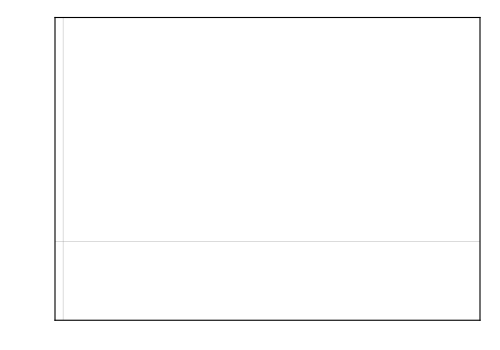

```mathematica
allaxionfieldsimg = ListPlot[axionfieldsets[[1;;95]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\lambda(r)",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,2*maxr},{-Pi/4*1.1,3*Pi/4*1.1}}]
```

```mathematica
(* why is it churning out results that are like half as big as the expectation? *)
```

```mathematica
(* 35 38 40 41 42 *)
```

```mathematica
allaxionderivsimg = ListPlot[axionderivsets[[{2, 22, 42, 62, 82}]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\lambda(r)",Magnification->2.0]},PlotStyle->{c1, c2, c3, c4, c5},ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,2*maxr},{-Pi/4*1.1,3*Pi/4*1.1}}]
```

-Graphics-

## get axion energy, pressure, and mass from python data

Need to load in all of the TOV functions for each axion field along with the actual axion field data.

#### Get MR relations

```mathematica
massradiusvals = Import["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/MR-vals.csv","CSV"];
```

```mathematica
maxr = massradiusvals[[1]][[1]]/10^3;
minr = massradiusvals[[95]][[1]]/10^3;
```

```mathematica
maxr
```

13.4091

```mathematica
myticks =Table[{i, MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[i,{3,1}]]],Magnification->1.5]},{i,12.8,13.6,0.1}];
```

```mathematica
mybarlegend = BarLegend[{Blend[{{minr,c1},{minr + (maxr-minr)/4,c2},{minr+ (maxr-minr)*2/4,c3},{minr+ (maxr-minr)*3/4,c4},{maxr,c5}},#]&,{12.79,maxr}},Ticks->myticks,LegendMarkerSize->700];
```

#### Get TOV Function Data

```mathematica
massfunctionsets = {};
nufunctionsets={};
densityfunctionsets={};
pressurefunctionsets={};
```

```mathematica
Npoints=100;
```

```mathematica
For[i=0, i<Npoints,i++,
AppendTo[massfunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/mass-vals-rhoc-",ToString[i],".csv"],"CSV"]];
AppendTo[nufunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/nu-vals-rhoc-",ToString[i],".csv"],"CSV"]]
AppendTo[densityfunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/density-vals-rhoc-",ToString[i],".csv"],"CSV"]]
AppendTo[pressurefunctionsets,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/python/EOS-1-functions/pressure-vals-rhoc-",ToString[i],".csv"],"CSV"]]
]
```

#### convert TOV function data to actual functions

```mathematica
massfsets = {};
nufsets={};
densityfsets={};
pressurefsets={};
```

```mathematica
Npoints=94;
```

```mathematica
For[i=1, i<Npoints,i++,
AppendTo[massfsets,Interpolation[massfunctionsets[[i]], Method->"Spline"]];
AppendTo[nufsets,Interpolation[nufunctionsets[[i]], Method->"Spline"]];
AppendTo[densityfsets,Interpolation[densityfunctionsets[[i]], Method->"Spline"]];
AppendTo[pressurefsets,Interpolation[pressurefunctionsets[[i]], Method->"Spline"]]
]
```

### linear friction

#### Get axion functions from python data

```mathematica
axionfunctionsets = {};
daxiondtsets = {};
daxiondrsets = {};

Module[{i,axionfunctionsfrompythondata},
For[i=1,i<=94,i++,
axionfunctionsfrompythondata=GetAxionFieldFromPython[StringJoin["/Users/wentmich/Documents/uiuc/research/axions-in-NS/cluster-outputs/linear-friction-hires/axion-and-derivative-rhoindex-",ToString[i],"-last-time-epsilon-100-faexponent-16.csv"],0];
AppendTo[axionfunctionsets, axionfunctionsfrompythondata[[1]]];
AppendTo[daxiondtsets, axionfunctionsfrompythondata[[2]]];
AppendTo[daxiondrsets, axionfunctionsfrompythondata[[3]]]
]
]

axionfieldsets = {};
axionderivsets = {};
For[i=1, i<=94,i++,
AppendTo[axionfieldsets,Table[{r/10^3,axionfunctionsets[[i]][r]},{r,10,40000,20}]]
]
For[i=1, i<=94,i++,
AppendTo[axionderivsets,Table[{r/10^3,daxiondtsets[[i]][r]},{r,10,40000,20}]]
]
```

#### Calculate mass, energy, and pressure

```mathematica
ϵ=(*0.4*)0.01;
fasub=10^16;
mafasubs = {Sqrt[fpi^2*mpi^2*ϵ/(2*fasub^2)],fasub}*GeV2m;
mynewscales={10^0,10^0,
1,10^4};
```

```mathematica
axionenergyfunctions = {};
axionpressurefunctions={};
axionpotentialenergyfunctions = {};
axionmassfunctions = {};
Module[{fileindex,testsolution,axiondensityfnc,axionpotentialfnc,axionmassfnc,axionpressurefnc},For[fileindex=1,fileindex<=94,fileindex++,testsolution = Quiet[GetAxionEnergyPressureAndMassFromPython[axionfunctionsets[[fileindex]],daxiondtsets[[fileindex]],daxiondrsets[[fileindex]],massradiusvals[[fileindex]],massfsets[[fileindex]],densityfsets[[fileindex]],nufsets[[fileindex]],mafasubs[[1]],mafasubs[[2]],mynewscales,irrelevant]];
axiondensityfnc = testsolution[[1]][[1]];
axionpressurefnc = testsolution[[1]][[2]];
axionmassfnc = testsolution[[1]][[4]];
axionpotentialfnc = testsolution[[1]][[6]];
AppendTo[axionenergyfunctions,axiondensityfnc];
AppendTo[axionpressurefunctions,axionpressurefnc];
AppendTo[axionpotentialenergyfunctions,axionpotentialfnc];
AppendTo[axionmassfunctions,axionmassfnc]
]]
```

#### Plot all axion fields

```mathematica
Mag=1.8;
```

```mathematica
xticks=Table[{j,If[Mod[j,4]==0,MaTeX[StringJoin["\\color{darkgray}",ToString[PaddedForm[j,{3,1}]]],Magnification->Mag],None],If[Mod[j,4]==0,0.013,0.005]},{j,0.0,2*maxr,0.5}];
xticksNV=Table[{j,None,If[Mod[j,4]==0,0.013,0.005]},{j,0.0,2*maxr,0.5}];
```

```mathematica
yticks={{-Pi/4, MaTeX["\\color{darkgray} -\\pi/4",Magnification->Mag], 0.013}, {0, MaTeX["\\color{darkgray} 0",Magnification->Mag], 0.013}, {Pi/4, MaTeX["\\color{darkgray} \\pi/4",Magnification->Mag], 0.013}, {Pi/2, MaTeX["\\color{darkgray} \\pi/2",Magnification->Mag], 0.013}, {3*Pi/4, MaTeX["\\color{darkgray} 3 \\pi/4",Magnification->Mag], 0.013}};
yticksNV={{-Pi/4,None, 0.013}, {0, None, 0.013}, {Pi/4,None, 0.013}, {Pi/2,None, 0.013}, {3*Pi/4,None, 0.013}};
```

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[3]]],{i, 1, 95}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,95}];
```

```mathematica
allaxionfieldsimg = ListPlot[axionfieldsets[[1;;80]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\lambda(r)",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,2*maxr},{-Pi/4*1.1,3*Pi/4*1.1}}]
```

-Graphics-

```mathematica
linespacing = 10;
allaxionfieldsimg = ListPlot[axionfieldsets[[Table[k,{k,1,90,linespacing}]]],Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} a(r)",Magnification->2.0]},PlotStyle->Table[plotstylelist[[k]],{k,1,90,linespacing}],ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,2*maxr},{-Pi/4*1.1,3*Pi/4*1.1}}];
(*GraphicsRow[{allaxionfieldsimg,mybarlegend},ImageSize->{1000,750},AspectRatio->0.6]*)
allaxionfieldsimg
```

-Graphics-

#### Plot all axion energies and masses

```mathematica
axionenergysets = {};
axionpontentialenergysets = {};
axionmasssets = {};
axionfractionalpotentialenergysets = {};
For[i=1, i<=8,i++,
AppendTo[axionenergysets,Table[{r/10^3,axionenergyfunctions[[i*10]][r]},{r,10,40000,100}]]
]
For[i=1, i<=8,i++,
AppendTo[axionmasssets,Table[{r/10^3,axionmassfunctions[[i*10]][r] * m2Msun},{r,10,40000,100}]]
]
```

General::munfl: 0.0627952 4.11921×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0627952 4.51648×10^-308 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
mycolors = Table[RGBColor[linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[1]],linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[2]],linetocolortotal[(massradiusvals[[i]][[1]]/10^3 - minr) / (maxr-minr)][[3]]],{i, 1, 95}];(*IBMcolors[Npoints];*)
plotstylelist = Table[{mycolors[[i]],Thickness[0.005]},{i,1,95}];
```

```mathematica
allaxionfieldsimg = ListPlot[axionenergysets[[1;;2]],Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\lambda(r)",Magnification->2.0]},PlotStyle->plotstylelist,ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,2*maxr},{-0.1*10^-12, 10^-11}}]
```

-Graphics-

```mathematica
linespacing=10;
allaxionfieldsimg = ListPlot[axionenergysets,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\lambda(r)",Magnification->2.0]},PlotStyle->Table[plotstylelist[[k]],{k,1,90,linespacing}],ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,2*maxr},{-0.1*10^-12, 1.2*10^-11}}]
```

-Graphics-

```mathematica
linespacing=10;
allaxionfieldsimg = ListPlot[axionmasssets,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray} M \\ \\left[M_{\\odot} \\right]",Magnification->2.0]},PlotStyle->Table[plotstylelist[[k]],{k,1,90,linespacing}],ImageSize->{500,350},AspectRatio->Full,PlotRange->{{0.0,2*maxr},{0.0, 0.05}}]
```

-Graphics-

#### try to calculate metric perturbation zeta

```mathematica
fileindex = 42;
pertsols = GetDeltaAndZetaMetricPerturbations[massradiusvals[[fileindex]],massfsets[[fileindex]],densityfsets[[fileindex]],pressurefsets[[fileindex]],axionenergyfunctions[[fileindex]],axionpressurefunctions[[fileindex]],axionmassfunctions[[fileindex]][massradiusvals[[fileindex]][[1]]],{1, 1, 1}];
zetafnc[r_]:=Evaluate[pertsols[[1]][[1]][r]]
deltafnc[r_]:=Evaluate[pertsols[[1]][[2]][r]]
```

```mathematica
pertsols[[1]][[1]][r]
```

If[r<13063.7,ζsolin$328254(r),70.0838/(2934.66-r)]

```mathematica
Plot[deltafnc[r],{r,10,20000}]
```

-Graphics-

```mathematica
GetTidalDeformabilityWithAxions[massradiusvals[[fileindex]],massfsets[[fileindex]],pressurefsets[[fileindex]],densityfsets[[fileindex]],axionmassfunctions[[fileindex]],axionpressurefunctions[[fileindex]],axionenergyfunctions[[fileindex]],deltafnc,zetafnc,{1,1,1}]
```

0.805315

(3141.9 | 3486.45
y0fncsol$331341 | y1fncsol$331341)

```mathematica
%[[1]]
```

{3141.9,3486.45}

#### Try to calculate tidal deformabilities

```mathematica
lambdasmassesa = {};
lambdasmassesnoa = {};
For[i=1,i<=80,i++,
fileindex = i;
pertsols = GetDeltaAndZetaMetricPerturbations[massradiusvals[[fileindex]],massfsets[[fileindex]],densityfsets[[fileindex]],pressurefsets[[fileindex]],axionenergyfunctions[[fileindex]],axionpressurefunctions[[fileindex]],axionmassfunctions[[fileindex]][massradiusvals[[fileindex]][[1]]],{1, 1, 1}];
zetafnc[r_]:=Evaluate[pertsols[[1]][[1]][r]];
deltafnc[r_]:=Evaluate[pertsols[[1]][[2]][r]];
lambdas = GetTidalDeformabilityWithAxions[massradiusvals[[fileindex]],massfsets[[fileindex]],pressurefsets[[fileindex]],densityfsets[[fileindex]],axionmassfunctions[[fileindex]],axionpressurefunctions[[fileindex]],axionenergyfunctions[[fileindex]],deltafnc,zetafnc,{1,1,1}];
Λa = lambdas[[1]][[1]];
Λnoa = lambdas[[1]][[2]];
AppendTo[lambdasmassesa,{massradiusvals[[fileindex]][[2]]+axionmassfunctions[[fileindex]][massradiusvals[[fileindex]][[1]]],Λa}];
AppendTo[lambdasmassesnoa,{massradiusvals[[fileindex]][[2]],Λnoa}];
If[Mod[fileindex,10]==0,Print[StringJoin["Done with: ",ToString[fileindex]]]]]
```

Done with: 10

Done with: 20

Done with: 30

Done with: 40

Done with: 50

Done with: 60

Done with: 70

Done with: 80

```mathematica
lambdaafnc = Interpolation[lambdasmassesa]
lambdanoafnc = Interpolation[lambdasmassesnoa]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot[(lambdaafnc[m] - lambdanoafnc[m])/lambdanoafnc[m],{m, 868, 3.31*10^3}]
```

-Graphics-

```mathematica
ListLogPlot[{lambdasmassesa,lambdasmassesnoa},Joined->True]
```

-Graphics-

```mathematica
allaxionfieldsimg = ListLogPlot[{lambdasmassesa,lambdasmassesnoa},Joined->True,PlotTheme->"Scientific",FrameTicks->Automatic,FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[\\text{m}\\right]",Magnification->2.0],MaTeX["\\color{darkgray} \\Lambda",Magnification->2.0]},PlotStyle->{{Thick,c1},{Dashed,c2}},ImageSize->{500,350},AspectRatio->Full,PlotRange->All]
```

-Graphics-